## Initialization

### Packages, Paths, common options

```mathematica
SetOptions[$FrontEnd,CommonDefaultFormatTypes->{"Output"->StandardForm}];
If[FileExistsQ["~/home-uni/algebra/packages"],BaseDir="~/home-uni",BaseDir="~/uni"];
SetDirectory[BaseDir<>"/papers/sterile-nu/sim"];
$Path=Append[$Path,BaseDir<>"/algebra/packages"];
<<KPTools.m;
<<GlbPlots.m;

(* Taken from http://forums.wolfram.com/mathgroup/archive/1999/Apr/msg00028.html (slightly modified) *)
JHEPPlot[grObj_Graphics]:=Module[{fulopts,tcklst,th=0.004},
fulopts=FullOptions[grObj];
tcklst=FrameTicks/.fulopts/.{loc_,lab_,len:{_,_},{sty:___}}:>{loc,lab,2*len,{Directive[sty,Thickness[th]]}};
grObj/.Graphics[prims_,(opts__)?OptionQ]:>Graphics[prims,FrameTicks->tcklst,FrameTicksStyle->Thickness[th],FrameStyle->Thickness[th],opts]
];

KPImport[file_String,opts___]:=Module[{},
(*If[AbsoluteTime[FileDate[file]]<AbsoluteTime[{2013,3,7}],
Print[Style["Warning: File "<>file<>" is older than March 7, 2012!",FontColor->Red]];
];*)
Return[Import[file,opts]];
];
```

### Reading GLoBES event rate files

```mathematica
glbSignalTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,Plus@@Data⟦1,All,All,2⟧}];
glbBGTot[Data_List]:=Transpose[{Data⟦2,1,All,1⟧,Plus@@Data⟦2,All,All,2⟧}];
glbSignalBGTot[Data_List]:=Transpose[{Data⟦1,1,All,1⟧,(Plus@@Data⟦1,All,All,2⟧)+(Plus@@Data⟦2,All,All,2⟧)}];
```

## MiniBooNE

### Beam fluxes

```mathematica
DataFiles={
"0-code/glb/mb-2010/MBanti-flux.dat"
};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Import[DataFiles⟦i⟧,"Table"];
];
```

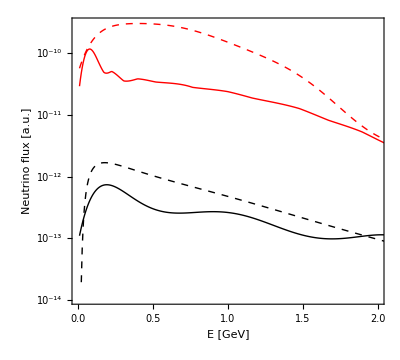

```mathematica
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ListLogPlot[Table[{#⟦1⟧,#⟦j⟧}&/@Data[i],{j,2,7}],Joined->True,PlotRange->{{0,2},All},
PlotStyle->{Directive[Black,Thick],Directive[Red,Thick],Directive[Blue,Thick],
Directive[Black,Dashed],Directive[Red,Dashed],Directive[Blue,Dashed]},FrameLabel->{"E [GeV]", "Neutrino flux [a.u.]"}];
];
Grid[{{MyPlot[1]}}]
```

### Preparation of AEDL file using data from MiniBooNE homepage

```mathematica
MCEventsAll=Import["0-code/glb/miniboone/data/miniboone_nunubarfullosc_ntuple.txt","Table"];
MCEventsNuBar=Import["0-code/glb/miniboone/data/miniboone_numubarnuebarfullosc_ntuple.txt","Table"];

BinBoundaries=Flatten[Import["0-code/glb/miniboone/data/miniboone_binboundaries_nubar_lowe.txt","Table"]];
BinWidths=Table[BinBoundaries⟦i+1⟧-BinBoundaries⟦i⟧,{i,1,Length[BinBoundaries]-1}];
GlbFile=Import["0-code/glb/miniboone/MBanti200-nu2010.glb"];
SamplingMin=1000.ToExpression[StringCases[GlbFile,RegularExpression["\$sampling_min\s*=\s*([-.e+\d]*)"]:>"$1"]⟦1⟧];
SamplingMax=1000.ToExpression[StringCases[GlbFile,RegularExpression["\$sampling_max\s*=\s*([-.e+\d]*)"]:>"$1"]⟦1⟧];
SamplingPoints=ToExpression[StringCases[GlbFile,RegularExpression["\$sampling_points\s*=\s*([-.e+\d]*)"]:>"$1"]⟦1⟧];
SamplingBinWidth=(SamplingMax-SamplingMin)/SamplingPoints;
SamplingBinBoundaries=Table[SamplingMin+k*SamplingBinWidth,{k,0,SamplingPoints}];
```

#### Flux from MC events

```mathematica
TrueSpectrum=(Total[#⟦All,4⟧]&)/@Flatten[BinLists[MCEventsNuBar,{{-∞,∞}},{SamplingBinBoundaries},{{-∞,∞}},{{-∞,∞}}],3];
TrueSpectrum=Transpose[{SamplingBinBoundaries⟦1;;-2⟧+SamplingBinWidth/2,TrueSpectrum}];
```

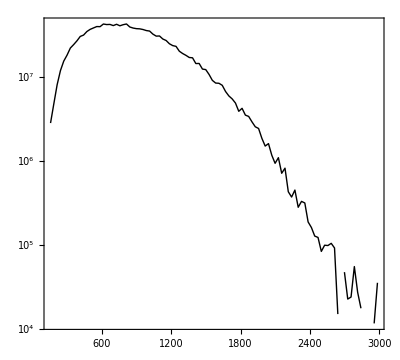

```mathematica
ListLogPlot[TrueSpectrum,Joined->True,PlotStyle->Directive[Thick,Black]]
```

#### Number of predicted full transmutation events (for normalization factor in AEDL file)

```mathematica
Total[MCEventsAll⟦All,4⟧]/Length[MCEventsAll]
Total[MCEventsNuBar⟦All,4⟧]/Length[MCEventsNuBar]
```

22382.9

17072.

#### Smearing matrix

```mathematica
SmearingMatrix=BinLists[MCEventsNuBar⟦All,{1,2,4}⟧,{BinBoundaries},{SamplingBinBoundaries},{{-∞,∞}}];
```

```mathematica
(*SmearingMatrixNormalized=Transpose[If[Total[#]==0,#,N[#/Total[#]]]&/@Transpose[SmearingMatrix]];*)
SmearingMatrixNormalized=Map[Total[#⟦All,3⟧]/Length[MCEventsNuBar]&,Flatten[SmearingMatrix,{{1},{2,3},{4}}],{2}];
OutputString="// Mapping of true neutrino energy to reconstructed energy\n"<>
"// in MiniBooNE\n"<>
"// from www-boone.fnal.gov/for_physicists/data_release/nuebar2010/\n"<>
"//\n"<>
"energy(#ERES)<\n"<>
"  @energy =\n";
For[i=1,i≤Length[SmearingMatrix],i++,
OutputString=OutputString<>"{0, "<>ToString[SamplingPoints-1]<>StringJoin[Flatten[Table[{", ",ToString[SmearingMatrixNormalized⟦i,j⟧]},{j,1,Length[SmearingMatrix⟦i⟧]}]]]<>"}";
If[i<Length[SmearingMatrix],OutputString=OutputString<>":\n"];
];
OutputString=OutputString<>";\n>\n";
Export["0-code/glb/miniboone/smearing_matrix.dat",OutputString,"Text"];
```

### Results

```mathematica
(* Read GLoBES chi^2 table *)
DataFiles={"2-sterile-fit/mb-nuebar.dat"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}]⟦All,1;;3⟧;
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->2];
logthMin[i]=Min[Data[i]⟦All,1⟧];
logthMax[i]=Max[Data[i]⟦All,1⟧];
logs22thMin[i]=N[Log10[RadToS2[10.^logthMin[i]]]];
logs22thMax[i]=N[Log10[RadToS2[10.^logthMax[i]]]];
logdmMin[i]=Min[Data[i]⟦All,2⟧];
logdmMax[i]=Max[Data[i]⟦All,2⟧];
Chi2Min[i]=Min[Data[i]⟦All,3⟧];
];

(* Read MiniBooNE data *)
DataMB={Log10[#⟦2⟧],Log10[#⟦1⟧],#⟦3⟧}&/@Import["0-code/glb/miniboone/data/likelihoodsurface_nubar_lowe.txt","Table"];
(*DataMB={Log10[#⟦2⟧],Log10[#⟦1⟧],#⟦3⟧}&/@Import["0-code/glb/miniboone/data/effective_chi2_surface_200.txt","Table"];*)
DataMBInterpol=Interpolation[DataMB,InterpolationOrder->1];
Chi2MinMB=Min[DataMB⟦All,3⟧];
```

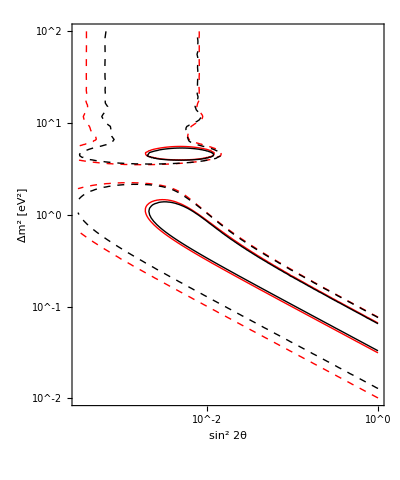

```mathematica
i=1;
MyStyles={Directive[Thick,Red,Dashing[{}]],Directive[Thick,Red,Dashed],Directive[Thick,Red,Dotted]};
MyContours={χ2[2,0.32],χ2[2,0.1],χ2[2,0.01]};
MyContours={χ2[2,0.1],χ2[2,0.01]};
Show[
ContourPlot[DataInterpol[i][Log10[S2ToRad[10.^logs22th]],logdm]-Chi2Min[i],{logs22th,-3.5,logs22thMax[i]},{logdm,logdmMin[i],logdmMax[i]},Contours->MyContours,PlotRange->Full,ContourShading->None,ContourStyle->MyStyles],
ContourPlot[DataMBInterpol[logs22th,logdm]-Chi2MinMB,{logs22th,-3.5,logs22thMax[i]},{logdm,logdmMin[i],logdmMax[i]},Contours->MyContours,ContourShading->None,ContourStyle->(Directive[#,Thickness[Medium],Black]&/@MyStyles)],
FrameLabel->{"sin^2 2θ","Δm^2 [eV^2]"},FrameTicks->{LogTicks[-4,1],LogTicks[-4,4],LogTicksNoLabel[-4,1],LogTicksNoLabel[-4,4]},AspectRatio->1.2
]
```

### MiniBooNE / SciBooNE combined analysis 2012

```mathematica
M=Import["0-code/glb/mb-2012/mb-sb-combined/total_error_matrix.bin.gz","Table"];
Eigenvalues[M]
```

{9.66216×10^6,564483.,45785.6,35474.,17609.6,13874.3,8779.72,8406.62,7961.14,5869.58,5811.2,5397.48,4569.43,4392.48,3982.26,3397.75,3181.21,2758.64,2270.93,1926.32,1767.61,1627.84,1554.81,1507.32,1307.26,1100.09,1067.06,1008.02,958.839,906.69,777.601,680.536,654.598,579.632,505.884,386.668,246.547,150.976,94.3962,60.9466,40.1562,37.1509}

```mathematica
Dir="0-code/glb/mb-2012/mb-sb-combined/";
Data[1]=Import[Dir<>"MB_mc_events.bin.gz","Table"];
Data[2]=Import[Dir<>"SB_mc_events.bin.gz","Table"];
BinBoundaries[1]=Import[Dir<>"bins.bin.gz","Table"]⟦All,1⟧;
BinBoundaries[2]=Import[Dir<>"bins.bin.gz","Table"]⟦All,2⟧;
```

```mathematica
i=1;
Data2[i]=Select[Data[i],#⟦1⟧>0&]⟦All,{3,5}⟧;
Data2[i]=BinLists[Data2[i],{BinBoundaries[i]},{{0,1*^10}}];
Data2[i]=Flatten[Data2[i]⟦All,All,All,2⟧,{{1},{2,3}}];
Data2[i]=Total/@Data2[i]
```

{{{{0.360709,0.0404912},{0.397898,0.0244523},{0.38293,0.0282324},{0.397569,0.0288966},{0.362111,0.0328622},{0.399156,0.0283877},{0.39795,0.0260157},{0.355854,0.0226681},{0.366126,0.0408656},{0.362481,0.0268509},«1119»,{0.397798,0.0283708},{0.393047,0.0314155},{0.398368,0.028803},{0.359411,0.0285048},{0.399011,0.0363726},{0.39426,0.0251887},{0.36391,0.0336241},{0.392985,0.0287577},{0.377357,0.0287309}}},«18»,{{«1»}}}

{{0.0404912,0.0244523,0.0282324,0.0288966,0.0328622,0.0283877,0.0260157,0.0226681,0.0408656,0.0268509,0.0344464,0.0366527,0.0284924,0.0282324,0.0314129,0.028687,0.0220832,0.0289031,0.036694,0.0483481,0.0285244,«1097»,0.0284503,0.0282324,0.0325605,0.062642,0.0260127,0.0287129,0.0315703,0.0304364,0.0282324,0.0254478,0.0565169,0.0283708,0.0314155,0.028803,0.0285048,0.0363726,0.0251887,0.0336241,0.0287577,0.0287309},«19»}

{37.7137,256.914,580.644,863.319,1030.25,1090.09,1089.11,1053.11,996.69,923.601,830.08,741.642,651.937,564.395,489.961,425.209,353.591,291.538,231.936,248.592}

### Spectra and Exclusion Regions from Joachim’s 2018 code

```mathematica
(* Read MiniBooNE data *)
DataFilesMB={"0-code/glb/mb-jk-2018/miniboone_nuedata_lowe.txt"};
DataFilesMBBG={"0-code/glb/mb-jk-2018/miniboone_nuebgr_lowe.txt"};
DataFilesMBBGStacked={"0-code/glb/mb-jk-2018/mb-all-bg-1805.12028.dat"};
BinBoundaries0=Flatten[Import["0-code/glb/mb-jk-2018/miniboone_binboundaries_nue_lowe.txt","Table"]]MeV//.NN;
BinWidths0=Differences[BinBoundaries0];
BinCenters0=ListConvolve[{0.5,0.5},BinBoundaries0];
BGStyles={Null,
{Directive[Thin,Black],GrayLevel[.6]},
{Directive[Thin,Black],RGBColor[0.529,0.4,0.341]},
{Directive[Thin,Black],RGBColor[0.867,0.729,0.529]},
{Directive[Thin,Black],RGBColor[0.812,0.373,0.38]},
{Directive[Thin,Black],RGBColor[0.518,0.761,0.639]},
{Directive[Thin,Black],RGBColor[0.690,0.812,0.78]}
};
For[i=1,i≤Length[DataFilesMB],i++,
BinBoundaries[i]=BinBoundaries0;
BinWidths[i]=BinWidths0;
BinCenters[i]=BinCenters0;
DataMB[i]=Transpose[{BinCenters0,Flatten[Cases[Import[DataFilesMB⟦i⟧,"Table"],{Repeated[_?NumericQ]}]]}];
DataMBBG[i]=Transpose[{BinCenters0,Flatten[Cases[Import[DataFilesMBBG⟦i⟧,"Table"],{Repeated[_?NumericQ]}]]}];
DataMBBGStacked[i]=Cases[Import[DataFilesMBBGStacked⟦i⟧,"Table"],{Repeated[_?NumericQ]}]*MeV^-1//.NN;
MBSystUpperInterpol=Interpolation[Transpose[{BinBoundaries[i],
Prepend[DataMBBGStacked[i]⟦All,-2⟧,DataMBBGStacked[i]⟦1,-2⟧]}//.NN],InterpolationOrder->0];
MBSystLowerInterpol=Interpolation[Transpose[{BinBoundaries[i],
Prepend[DataMBBGStacked[i]⟦All,-1⟧,DataMBBGStacked[i]⟦1,-1⟧]}//.NN],InterpolationOrder->0];

PlotListObs[i]=MapThread[{{#1⟦1⟧/GeV,#1⟦2⟧/#2/MeV^-1},ErrorBar[#2/2/GeV,N[Sqrt[#⟦2⟧]]/#2/MeV^-1]}//.NN&,{DataMB[i],BinWidths[i]}];
MyPlotObs[i]=ErrorListPlot[PlotListObs[i],PlotRange->All,PlotStyle->Directive[Thick,Black]];
MyPlotBGStacked[i]=Show[Sequence@@Table[
ListPlot[Transpose[{BinBoundaries[i]/GeV,Append[DataMBBGStacked[i]⟦All,j⟧,DataMBBGStacked[i]⟦-1,j⟧]/MeV^-1}//.NN],Joined->True,InterpolationOrder->0,PlotStyle->BGStyles⟦j,1⟧,Filling->{1->{Bottom,BGStyles⟦j,2⟧}}],{j,Length[DataMBBGStacked[i]⟦1⟧]-2,2,-1}],
RegionPlot[MBSystLowerInterpol[x GeV]<y/MeV<MBSystUpperInterpol[x GeV]//.NN,Evaluate[{x,BinBoundaries[i]⟦1⟧/GeV,BinBoundaries[i]⟦-1⟧/GeV}//.NN],{y,0,4.5},PlotPoints->50,Mesh->150,MeshFunctions->{#1-#2&},BoundaryStyle->None,MeshStyle->Directive[GrayLevel[.6],Thickness[.002]],PlotStyle->Transparent],
ListPlot[{Transpose[{BinBoundaries[i]/GeV,Append[DataMBBGStacked[i]⟦All,-2⟧,DataMBBGStacked[i]⟦-1,-2⟧]/MeV^-1}//.NN],
Transpose[{BinBoundaries[i]/GeV,Append[DataMBBGStacked[i]⟦All,-1⟧,DataMBBGStacked[i]⟦-1,-1⟧]/MeV^-1}//.NN]},
Joined->True,InterpolationOrder->0,PlotStyle->None,Filling->{1->{{2},GrayLevel[0,.2]}}]];
];

(* Read spectrum from Joachim's code *)
DataFiles={"mbjk-3p1","mbjk-m4G1-MAM40.5","mbjk-m4G1-MAM40.7"}/.s_String:>"1-spectra/"<>s<>".dat";
MyStyles={Directive[Thick,Dashed,Black],Directive[Thick,Blue]};
For[i=1,i≤Length[DataFiles],i++,
DataRaw[i]=Import[DataFiles⟦i⟧,"Text"];
DM41[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *DM41 = ([-+0-9eE\\.]*).*"]:>"$1"]];
Ue4[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *Ue4 = ([-+0-9eE\\.]*).*"]:>"$1"]];
Uμ4[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *Um4 = ([-+0-9eE\\.]*).*"]:>"$1"]];
mAm4[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *MA_OVER_M4 = ([-+0-9eE\\.]*).*"]:>"$1"]];
m4Gamma[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *M4_GAMMA = ([-+0-9eE\\.]*).*"]:>"$1"]];

DataJK[i]=Cases[Import[DataFiles⟦i⟧],{"#","MBJKSPECT",x__}:>{x}];
EventsSignal[i]=Transpose[{BinCenters[1],DataJK[i]⟦All,1⟧}];
EventsBG[i]=Transpose[{BinCenters[1],Total/@DataJK[i]⟦All,{2,3,4}⟧}];
EventsTotal[i]=Transpose[{BinCenters[1],Total/@DataJK[i]}];
];

(* Plot spectra *)
For[i=1,i≤Length[DataFiles],i++,
MyStyle=If[i==1,Directive[Thick,Blue,Dotted],Directive[Thick,Red]];

(* make signal plot *)
PlotListSignal[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundaries[1],Append[EventsSignal[i],EventsSignal[i]⟦-1⟧],Append[BinWidths[1],BinWidths[1]⟦-1⟧]}];
MyPlotSignal[i]=ListPlot[PlotListSignal[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[MyStyle,Dashed]];

(* make background plot *)
PlotListBG[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundaries[1],Append[EventsBG[i],EventsBG[i]⟦-1⟧],Append[BinWidths[1],BinWidths[1]⟦-1⟧]}];
MyPlotBG[i]=ListPlot[PlotListBG[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[MyStyle,Dotted](*Filling->{{1->{Bottom,RGBColor[.8,.6,.8]}}}*)];

(* make plot of total rate (sig+bg) *)
PlotListTotal[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundaries[1],Append[EventsTotal[i],EventsTotal[i]⟦-1⟧],Append[BinWidths[1],BinWidths[1]⟦-1⟧]}];
MyPlotTotal[i]=ListPlot[PlotListTotal[i],InterpolationOrder->0,Joined->True,
PlotStyle->MyStyle];
];
```

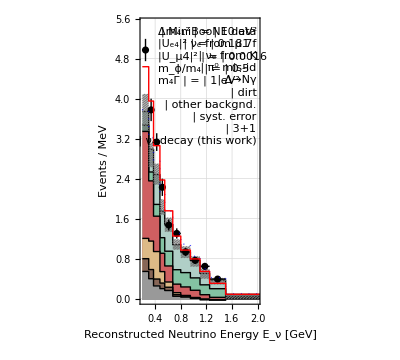

```mathematica
Clear[MyLegend];
For[i=2,i≤2+0Length[DataFiles],i++,
MyLegend1[i]=Framed[Grid[{
{LegendDataPoint[PlotStyle->Directive[Thick,Black]],"MiniBooNE data"},
{LegendBox[BGStyles⟦7,2⟧,BGStyles⟦7,1⟧],"ν_e from μ.7f"},
{LegendBox[BGStyles⟦6,2⟧,BGStyles⟦6,1⟧],"ν_e from K"},
{LegendBox[BGStyles⟦5,2⟧,BGStyles⟦5,1⟧],"π^0 mis-id"},
{LegendBox[BGStyles⟦4,2⟧,BGStyles⟦4,1⟧],"Δ→Nγ"},
{LegendBox[BGStyles⟦3,2⟧,BGStyles⟦3,1⟧],"dirt"},
{LegendBox[BGStyles⟦2,2⟧,BGStyles⟦2,1⟧],"other backgnd."},
{Show[LegendBox[GrayLevel[0,.2]],RegionPlot[True,{x,0,1},{y,0,1},Mesh->6,MeshFunctions->{#1-2#2&},BoundaryStyle->None,MeshStyle->Directive[Black,Thickness[.007]],PlotStyle->Transparent]],"syst. error"},
{LegendLine[Directive[Thick,Blue,Dotted]],"3+1"},
(*{LegendLine[Directive[Thick,Blue,Dotted]],"3+1 BG"},*)
{LegendLine[Directive[Thick,Red]],"ν_4 decay (this work)"}
(*{LegendLine[Directive[Thick,Red,Dotted]],"ν_4 decay BG"}*)
},ItemSize->{Automatic,1.3},Spacings->{Automatic,0}, Alignment->{Left,Baseline},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyLegend2[i]=Framed[Grid[{
{"Δm_41^2","=",ToString[DM41[i]]<> " eV^2"},
{"|U_e4|^2","=",ToString[Round[Ue4[i]^2,0.001]]},
{"|U_μ4|^2","=",ToString[Uμ4[i]^2]},
{"m_ϕ/m_4","=",ToString[mAm4[i]]},
{"m_4Γ","=",ToString[m4Gamma[i]]<>" eV^2"}
},ItemSize->{Automatic,1.3}, Spacings->{0.3,0},Alignment->{{Right,Center,Left},Baseline},BaseStyle->{FontSize->15}],Background->RGBColor[1,1,1,.8]];
MyPlot[i]=Show[
MyPlotBGStacked[1],MyPlotObs[1],(*MyPlotBG[1],*)MyPlotTotal[1],(*MyPlotBG[i],*)MyPlotTotal[i],
PlotRange->{{0.2,2.},{0,5.5}},GridLines->Automatic,PlotRangePadding->0,
FrameLabel->{"Reconstructed Neutrino Energy E_ν [GeV]","Events / MeV"},
Epilog->{Inset[MyLegend1[i],Scaled[{0.97,0.97}],{1,1}],Inset[MyLegend2[i],Scaled[{0.15,0.97}],{-1,1}]}]
];
Grid[{{MyPlot[2]}}]
```

```mathematica
DataFiles="8-oscdecay/dm41s22thmueUm4-mbjk"<>#<>"-globes.dat"&/@{"","-numunorm","-bgosc","-numuosc"};
For[i=1,i≤Length[DataFiles],i++,
DataRaw[i]=KPImport[DataFiles⟦i⟧,"Table"];
Data[i]=Cases[DataRaw[i],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
If[Cases[DataRaw[i],{___,"DM41","s22thmue","Um4",___}]=!={},
(* Data files in dm41, s22thmue, Um4 *)
Data[i]={#⟦1⟧,#⟦2⟧,#⟦3⟧,If[10^(#⟦2⟧)/(4*(10^(#⟦3⟧))^2)>0.2,1.*^12,#⟦4⟧]}&/@Data[i]; (* restrict Subscript[U, e4] range *)
Data[i]=Split[Sort[Data[i]],#1⟦{1,2}⟧==#2⟦{1,2}⟧&];
(*Data[i]=Select[#,#⟦3⟧==-1.0&]⟦1,{1,2,4}⟧&/@Data[i], (* select specific Subscript[U, μ4] *)*)
Data[i]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Data[i], (* select optimum Subscript[U, μ4] *)

(* Else - data files in dm41, th14, th24 *)
Print["Wrong file format!"];
];
logdmsqMin[i]=Min[Data[i]⟦All,1⟧];
logdmsqMax[i]=Max[Data[i]⟦All,1⟧];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
logs22thMin[i]=Min[Data[i]⟦All,2⟧];
logs22thMax[i]=Max[Data[i]⟦All,2⟧];

(* Extract best fit point: Either it has been computed accurately, or we take the best available grid point *)
BFP[i]=Cases[DataRaw[i],{"BF_IH"|"BF_NH",___}];
If[BFP[i]≠{}, (* Has a best fit point been computed? *)
BFP[i]=First[Sort[BFP[i],#1⟦3⟧≤#2⟦3⟧&]];
ExtractParam[s_,param_String]:=s/.{{__,param,x_,___}:>x};
Chi2Min[i]=ExtractParam[BFP[i],"chi^2"];
BFP[i]={Log10[ExtractParam[BFP[i],"DM41"]],Log10[ExtractParam[BFP[i],"s22thmue"]],Chi2Min[i]},

(* Else: Take grid point with lowest χ^2 *)
Chi2Min[i]=Cases[DataRaw[i],{"Chi2Min",___,x_?NumericQ}:>x];
If[Length[Chi2Min[i]]==0,
Chi2Min[i]=Min[Data[i]⟦All,-1⟧],
(* Else *)
Chi2Min[i]=Chi2Min[i]⟦1⟧;
];
BFP[i]=Select[Data[i],#⟦-1⟧==Chi2Min[i]&]⟦1⟧;
]; (* End[if] *)

Print["   Best fit: sin^22θ_μe=",10^BFP[i]⟦2⟧,", Δm^2=",10^BFP[i]⟦1⟧];
Chi2NoOsc[i]=DataInterpol[i][logdmsqMin[i],logs22thMin[i]];
Print["   χ_min^2=",Chi2Min[i],", χ_(no osc)^2=",Chi2NoOsc[i],", Δχ_(no osc.)^2=",Chi2NoOsc[i]-Chi2Min[i]," (CL ",CDF[ChiSquareDistribution[2]][Chi2NoOsc[i]-Chi2Min[i]],")"];
]; (* End[loop over data files] *)
```

Best fit: sin^22θ_μe=0.389045, Δm^2=0.0501187

χ_min^2=337.12, χ_(no osc)^2=358.392, Δχ_(no osc.)^2=21.2724 (CL 0.999976)

Best fit: sin^22θ_μe=0.00154882, Δm^2=0.501187

χ_min^2=327.534, χ_(no osc)^2=358.392, Δχ_(no osc.)^2=30.8579 (CL 1.)

Best fit: sin^22θ_μe=0.00245471, Δm^2=0.398107

χ_min^2=326.172, χ_(no osc)^2=359.571, Δχ_(no osc.)^2=33.3987 (CL 1.)

Best fit: sin^22θ_μe=0.0616595, Δm^2=0.125893

χ_min^2=331.801, χ_(no osc)^2=359.392, Δχ_(no osc.)^2=27.5909 (CL 0.999999)

```mathematica
MyContours={χ2[2,PValue[1]],χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]],χ2[2,PValue[4]]};
MyStyles={Directive[Black,Dashing[{}]],Directive[Red,Dashed],Directive[Blue,Dashing[{0.005,0.002}]],Directive[RGBColor[0,0.6,0],DotDashed],Directive[Purple,Dotted],Directive[RGBColor[1,0.7,0.5],Dashing[{}]]};
MyFillingStyles={GrayLevel[0,.3],RGBColor[1,0,0,.3],RGBColor[0,0,1,.3],RGBColor[0,0.6,0,.3],RGBColor[0.5,0,0.5,.3],RGBColor[1,0.7,0.5,.3],None};
DataMB=Import["0-code/glb/mb-jk-2018/likihood_surface_contNunubar.txt","Table"];
Chi2MinMB=Min[DataMB⟦All,3⟧];
MBPlot=ListContourPlot[{Log10[#⟦2⟧],Log10[#⟦1⟧],#⟦3⟧-Chi2MinMB}&/@DataMB,Contours->MyContours,ContourShading->None,ContourStyle->Evaluate[Directive[Thick,Black]&/@MyStyles]];
```

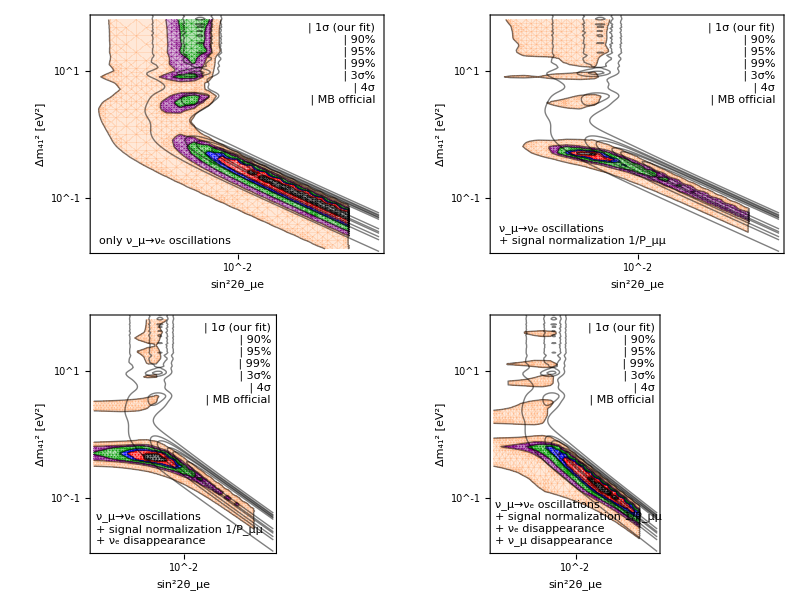

```mathematica
MyLegend=Framed[Grid[{
{LegendBox[MyFillingStyles⟦1⟧,Directive[Black,Thin]],"1σ (our fit)"},
{LegendBox[MyFillingStyles⟦2⟧,Directive[Black,Thin]],"90%"},
{LegendBox[MyFillingStyles⟦3⟧,Directive[Black,Thin]],"95%"},
{LegendBox[MyFillingStyles⟦4⟧,Directive[Black,Thin]],"99%"},
{LegendBox[MyFillingStyles⟦5⟧,Directive[Black,Thin]],"3σ%"},
{LegendBox[MyFillingStyles⟦6⟧,Directive[Black,Thin]],"4σ"},
{LegendLine[Black],"MB official"}
},Spacings->{0.3,0.2},Alignment->{{Center,Left},Automatic}],Background->GrayLevel[1,.8]];
MyLabels={
"only ν_μ→ν_e oscillations",
"ν_μ→ν_e oscillations\n+ signal normalization 1/P_μμ",
"ν_μ→ν_e oscillations\n+ signal normalization 1/P_μμ\n+ ν_e disappearance",
"ν_μ→ν_e oscillations\n+ signal normalization 1/P_μμ\n+ ν_e disappearance\n+ ν_μ disappearance"
};
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=Show[ContourPlot[DataInterpol[i][logdmsq,logth]-Chi2Min[i],{logth,Max[-5,logs22thMin[i]],logs22thMax[i]},{logdmsq,logdmsqMin[i],logdmsqMax[i]},PlotRange->Full,Contours->MyContours,ContourShading->MyFillingStyles,ContourStyle->Directive[Black,Thin],FrameLabel->{"sin^22θ_μe","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}}],
MBPlot,Epilog->{Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}],
Text[Style[MyLabels⟦i⟧,TextAlignment->Left],Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,.7]]}];
];
Grid[{{MyPlot[1],MyPlot[2]},{MyPlot[3],MyPlot[4]}}]
Export["s22thmue-dm41-osc.pdf",MyPlot[1]];
Export["s22thmue-dm41-signorm.pdf",MyPlot[2]];
Export["s22thmue-dm41-bgosc.pdf",MyPlot[3]];
Export["s22thmue-dm41-numuosc.pdf",MyPlot[4]];
```

```mathematica
(* initial spectrum from 2018 analysis *)
DataMC=Import["0-code/glb/mb-jk-2018/miniboone_nubarfullosc_ntuple.txt","Table"];
DataMC=DataMC⟦1;;25000⟧;
DataFlux=Import["0-code/glb/mb-jk-2018/MBanti-flux.dat","Table"];
		(* not sure what this file is based on - it seems to disagree e.g. with arXiv:1611.00820 *)
```

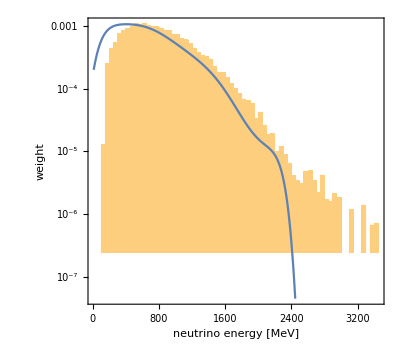

```mathematica
FluxPlot=ListLogPlot[{1000#⟦1⟧,3.5*^6#⟦6⟧}&/@DataFlux,Joined->True];
MCHistogram=Histogram[WeightedData[DataMC⟦All,1⟧,DataMC⟦All,4⟧],{0,3500,50},{"Log","PDF"}];
Show[MCHistogram,FluxPlot,PlotRange->All,
FrameLabel->{"neutrino energy [MeV]","weight"}
]
```

```mathematica
(* Backgrounds - convert from stacked to normal histograms (copy&paste result into C code *)
DataBG=Cases[Import["0-code/glb/mb-jk-2018/mb-spectrum-1805.12028.dat","Table"],{Repeated[_?NumberQ]}];
BinWidths={100,75,100,75,125,125,150,150,150,250,1500};
fracOther=Round[DataBG⟦All,2⟧/DataBG⟦All,-1⟧,0.001]
fracEfromK=Round[(DataBG⟦All,3⟧-DataBG⟦All,2⟧)/DataBG⟦All,-1⟧,0.001]
fracEfromMu=Round[(DataBG⟦All,4⟧-DataBG⟦All,3⟧)/DataBG⟦All,-1⟧,0.001]
```

{0.894,0.788,0.664,0.519,0.442,0.269,0.251,0.221,0.157,0.072,-0.06}

{0.034,0.06,0.095,0.178,0.199,0.267,0.306,0.325,0.391,0.462,0.663}

{0.073,0.152,0.241,0.303,0.358,0.463,0.443,0.454,0.452,0.466,0.397}

### Oscillation + Decay: Spectra from Pedro’s codes

```mathematica
(* Read MiniBooNE data *)
(*DataFilesMB={"http://www-boone.fnal.gov/for_physicists/data_release/nue_nuebar_2012/miniboone_nuedata_lowe.txt"};*)
DataFilesMB={"http://www-boone.fnal.gov/for_physicists/data_release/nue2018/miniboone_nuedata_lowe.txt"};
DataFilesMBBG={"https://www-boone.fnal.gov/for_physicists/data_release/nue2018/miniboone_nuebgr_lowe.txt"};
(*BinBoundaries0=Flatten[Import["http://www-boone.fnal.gov/for_physicists/data_release/"<>
"nue_nuebar_2012/miniboone_binboundaries_nue_lowe.txt","Table"]]MeV//.NN;*)
BinBoundaries0=Flatten[Import["http://www-boone.fnal.gov/for_physicists/data_release/"<>
"nue2018/miniboone_binboundaries_nue_lowe.txt","Table"]]MeV//.NN;
BinWidths0=Differences[BinBoundaries0];
BinCenters0=ListConvolve[{0.5,0.5},BinBoundaries0];
For[i=1,i≤Length[DataFilesMB],i++,
BinBoundaries[i]=BinBoundaries0;
BinWidths[i]=BinWidths0;
BinCenters[i]=BinCenters0;
DataMB[i]=Transpose[{BinCenters0,Flatten[Cases[Import[DataFilesMB⟦i⟧,"Table"],{Repeated[_?NumericQ]}]]}];
DataMBBG[i]=Transpose[{BinCenters0,Flatten[Cases[Import[DataFilesMBBG⟦i⟧,"Table"],{Repeated[_?NumericQ]}]]}];
PlotListObs[i]=MapThread[{{#1⟦1⟧/GeV,#1⟦2⟧/#2/MeV^-1},ErrorBar[#2/2/GeV,N[Sqrt[#⟦2⟧]]/#2/MeV^-1]}//.NN&,{DataMB[i],BinWidths[i]}];
MyPlotObs[i]=ErrorListPlot[PlotListObs[i],PlotRange->All,PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}];
];

(* Read GLoBES spectrum -- not used here because Pedro's code computes its own spectrum *)
DataFiles={{"mb2018-m4G0.001",{1,1}},{"mb2018-m4G10",{1,1}}}/.s_String:>"1-spectra/"<>s<>".dat";
MyStyles={Directive[Thick,Dashed,Black],Directive[Thick,Blue]};
For[i=1,i≤Length[DataFiles],i++,
DataRaw[i]=Import[DataFiles⟦i,1⟧,"Text"];
Data[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["#.*\n"]->""]]⟦Sequence@@DataFiles⟦i,2⟧⟧;
BinBoundaries[i]=BinBoundaries0;
BinWidths[i]=BinWidths0;
BinCenters[i]=BinCenters0;

(* extract event rates from GLobES output file *)
EventsSignal[i]={#⟦1⟧GeV,#⟦2⟧}//.NN&/@glbSignalTot[Data[i]]⟦1;;Length[BinBoundaries[i]]-1⟧;
EventsBG[i]={#⟦1⟧GeV,#⟦2⟧}//.NN&/@glbBGTot[Data[i]]⟦1;;Length[BinBoundaries[i]]-1⟧;
EventsTotal[i]={#⟦1⟧GeV,#⟦2⟧}//.NN&/@glbSignalBGTot[Data[i]]⟦1;;Length[BinBoundaries[i]]-1⟧;

(* extract metadata *)
DM41[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *DM41 = ([-+0-9eE\\.]*).*"]:>"$1"]];
M4Γ[i]=ToExpression[StringReplace[DataRaw[i],
RegularExpression["(?m)(?s).*# *M4_GAMMA = ([-+0-9eE\\.]*).*"]:>"$1"]];
Ue4[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *Ue4 = ([-+0-9eE\\.]*).*"]:>"$1"]];
Uμ4[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *Um4 = ([-+0-9eE\\.]*).*"]:>"$1"]];
];

(* Read spectrum from Pedro's code *)
For[i=1,i≤Length[DataFiles],i++,
DataPedro[i]=Cases[Import[DataFiles⟦i,1⟧],{"#","MBSPECT",x__}:>{x}];
EventsSignal[i]=Transpose[{EventsSignal[i]⟦All,1⟧,DataPedro[i]⟦All,1⟧}];
EventsBG[i]=Transpose[{EventsSignal[i]⟦All,1⟧,Total/@DataPedro[i]⟦All,{2,3,4}⟧+DataMBBG[1]⟦All,2⟧}];
EventsTotal[i]=Transpose[{EventsSignal[i]⟦All,1⟧,Total/@DataPedro[i]+DataMBBG[1]⟦All,2⟧}];
];

(* Plot spectra *)
For[i=1,i≤Length[DataFiles],i++,
(* make signal plot *)
PlotListSignal[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundaries[i],Append[EventsSignal[i],EventsSignal[i]⟦-1⟧],Append[BinWidths[i],BinWidths[i]⟦-1⟧]}];
MyPlotSignal[i]=ListPlot[PlotListSignal[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[Thick,Blue,Dashed]];

(* make background plot *)
PlotListBG[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundaries[i],Append[EventsBG[i],EventsBG[i]⟦-1⟧],Append[BinWidths[i],BinWidths[i]⟦-1⟧]}];
MyPlotBG[i]=ListPlot[PlotListBG[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[Thick,RGBColor[.6,0,0]],Filling->{{1->{Bottom,RGBColor[.8,.4,.4]}}}];

(* make plot of total rate (sig+bg) *)
PlotListTotal[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/MeV^-1}//.NN&,{BinBoundaries[i],Append[EventsTotal[i],EventsTotal[i]⟦-1⟧],Append[BinWidths[i],BinWidths[i]⟦-1⟧]}];
MyPlotTotal[i]=ListPlot[PlotListTotal[i],InterpolationOrder->0,Joined->True,
PlotStyle->MyStyles⟦i⟧];
];
```

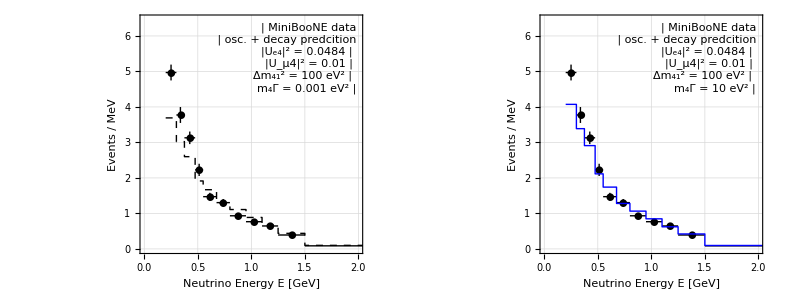

```mathematica
Clear[MyLegend];
For[i=1,i≤Length[DataFiles],i++,
MyLegend[i]=Framed[Grid[{
{LegendDataPoint[PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}],"MiniBooNE data"},
{LegendLine[Directive[Thick,Blue]],"osc. + decay predcition"},
{"|U_e4|^2 = "<>ToString[Ue4[i]^2],SpanFromLeft},
{"|U_μ4|^2 = "<>ToString[Uμ4[i]^2],SpanFromLeft},
{"Δm_41^2 = "<>ToString[DM41[i]]<>" eV^2",SpanFromLeft},
{"m_4Γ = "<>ToString[M4Γ[i]]<>" eV^2",SpanFromLeft}
},Spacings->{Automatic,Automatic}, Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];
MyPlot[i]=Show[
MyPlotObs[1],MyPlotTotal[i],
PlotRange->{{0,2},{0,1.3Max[Flatten[PlotListObs[1]⟦All,1,2⟧]]}},GridLines->Automatic,
FrameLabel->{"Neutrino Energy E [GeV]","Events / MeV"},
Epilog->{Inset[MyLegend[i],Scaled[{0.97,0.97}],{1,1}]}]
];
Grid[{{MyPlot[1],MyPlot[2]}}]
```

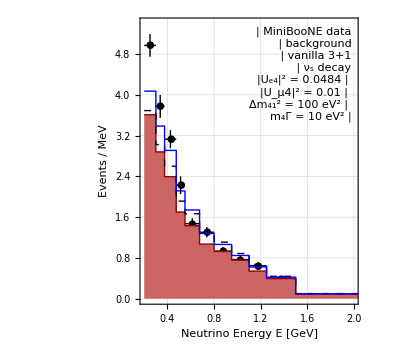

```mathematica
MyLegend[99]=Framed[Grid[{
{LegendDataPoint[PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}],"MiniBooNE data"},
{LegendBox[RGBColor[.8,.4,.4],Directive[Thick,RGBColor[.6,0,0]]],"background"},
{LegendLine[MyStyles⟦1⟧],"vanilla 3+1"},
{LegendLine[MyStyles⟦2⟧],"ν_s decay"},
{"|U_e4|^2 = "<>ToString[Ue4[2]^2],SpanFromLeft},
{"|U_μ4|^2 = "<>ToString[Uμ4[2]^2],SpanFromLeft},
{"Δm_41^2 = "<>ToString[DM41[2]]<>" eV^2",SpanFromLeft},
{"m_4Γ = "<>ToString[M4Γ[2]]<>" eV^2",SpanFromLeft}
},Spacings->{Automatic,Automatic}, Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];
MyPlot[99]=Show[
MyPlotObs[1],MyPlotBG[1],MyPlotTotal[1],MyPlotTotal[2],
PlotRange->{{0.2,2},{0,5.4}},(*PlotRangePadding->0,*)GridLines->Automatic,
FrameLabel->{"Neutrino Energy E [GeV]","Events / MeV"},
Epilog->{Inset[MyLegend[99],Scaled[{0.97,0.97}],{1,1}]}]
```

### Oscillation + Decay: Exclusion Regions

```mathematica
DataFiles={"8-oscdecay/th14th24-mb-2012-oscdecay.dat"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]={Sin[#⟦1⟧],Sin[#⟦2⟧],#⟦3⟧}&/@Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->2];
sth14Max[i]=Min[Data[i]⟦All,1⟧];
sth14Max[i]=Max[Data[i]⟦All,1⟧];
sth24Max[i]=Min[Data[i]⟦All,2⟧];
sth24Max[i]=Max[Data[i]⟦All,2⟧];
Chi2Min[i]=Min[Data[i]⟦All,3⟧];
];
```

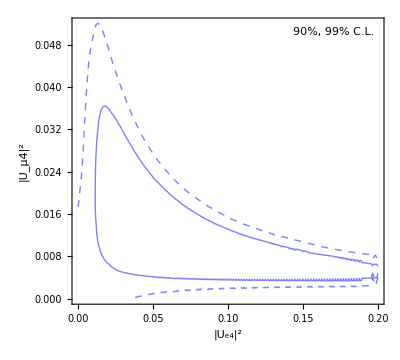

```mathematica
i=1;
ContourPlot[DataInterpol[i][Sqrt[Ue4sq],Sqrt[Uμ4sq/(1-Ue4sq)]]-Chi2Min[i],{Ue4sq,0,.2},{Uμ4sq,0,.3},
Contours->{χ2[2,0.1],χ2[2,0.01]},ContourShading->False,ContourStyle->{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},FrameLabel->{"|U_e4|^2","|U_μ4|^2"},
Epilog->{Text["90%, 99% C.L.",Scaled[{0.97,0.97}],{1,1}]}]
```

## LSND

## LSND

```mathematica
i=1;
DataFilesLSND={"0-code/glb/lsnd-globes/data/lsnd-data.dat"};
DataLSND[i]=Sort[{30/#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧}&/@Cases[Import[DataFilesLSND⟦i⟧,"Table"],{Repeated[_?NumericQ]}]];

BinBoundaries0=Range[0.4,1.5,0.1];
BinWidths0=Differences[BinBoundaries0];
BinCenters0=ListConvolve[{0.5,0.5},BinBoundaries0];

PlotListObs[i]=MapThread[{{#1,#2⟦2⟧},ErrorBar[0.05,#2⟦4⟧]}//.NN&,{BinCenters0,DataLSND[i]}];
MyPlotObs[1]=ErrorListPlot[PlotListObs[i],PlotRange->All,PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}];

(* Read spectrum from Ivan's code *)
DataFiles={{"lsnd-ivan-m4G0.001",{1,1}},{"lsnd-ivan-m4G10",{1,1}}}/.s_String:>"1-spectra/"<>s<>".dat";
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i,1⟧],{"#","LSNDSPECT",x__}:>{x}];
BinBoundaries[i]=BinBoundaries0;
BinWidths[i]=BinWidths0;
BinCenters[i]=BinCenters0;

(* Extract event spectra *)
EventsSignal[i]=Transpose[{BinCenters[i],Data[i]⟦All,2⟧}];
(*EventsBG[i]=Transpose[{BinCenters[i],Total/@Data[i]⟦All,{2,3,4}⟧}];*)
EventsTotal[i]=Transpose[{BinCenters[i],Data[i]⟦All,2⟧}];

(* extract metadata *)
DataRaw[i]=Import[DataFiles⟦i,1⟧,"Text"];
DM41[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *DM41 = ([-+0-9eE\\.]*).*"]:>"$1"]];
M4Γ[i]=ToExpression[StringReplace[DataRaw[i],
RegularExpression["(?m)(?s).*# *M4_GAMMA = ([-+0-9eE\\.]*).*"]:>"$1"]];
Ue4[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *Ue4 = ([-+0-9eE\\.]*).*"]:>"$1"]];
Uμ4[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *Um4 = ([-+0-9eE\\.]*).*"]:>"$1"]];
];

(* Plot spectra *)
For[i=1,i≤Length[DataFiles],i++,
(* make signal plot *)
PlotListSignal[i]=MapThread[{#1,#2⟦2⟧}//.NN&,{BinBoundaries[i],Append[EventsSignal[i],EventsSignal[i]⟦-1⟧]}];
MyPlotSignal[i]=ListPlot[PlotListSignal[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[Thick,Blue,Dashed]];

(* make background plot *)
PlotListBG[i]=MapThread[{#1,#2⟦3⟧}//.NN&,{BinBoundaries[i],Append[DataLSND[1],DataLSND[1]⟦-1⟧]}];
MyPlotBG[i]=ListPlot[PlotListBG[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[Thick,Red,Dashed]];

(* make plot of total rate (sig+bg) *)
PlotListTotal[i]=MapThread[{#1,#2⟦2⟧}//.NN&,{BinBoundaries[i],Append[EventsTotal[i],EventsTotal[i]⟦-1⟧]}];
MyPlotTotal[i]=ListPlot[PlotListTotal[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[Thick,Blue]];
];
```

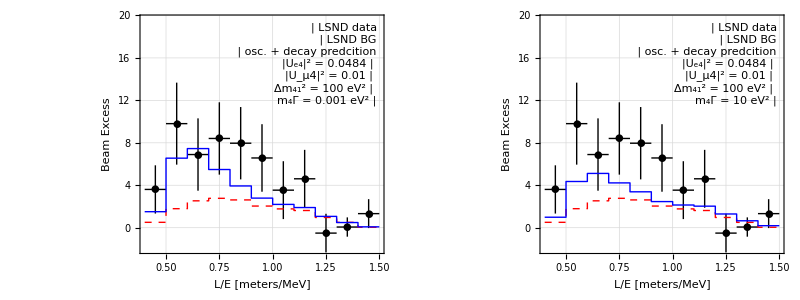

```mathematica
Clear[MyLegend];
For[i=1,i≤Length[DataFiles],i++,
MyLegend[i]=Framed[Grid[{
{LegendDataPoint[PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}],"LSND data"},
{LegendLine[Directive[Thick,Red,Dashed]],"LSND BG"},
{LegendLine[Directive[Thick,Blue]],"osc. + decay predcition"},
{"|U_e4|^2 = "<>ToString[Ue4[i]^2],SpanFromLeft},
{"|U_μ4|^2 = "<>ToString[Uμ4[i]^2],SpanFromLeft},
{"Δm_41^2 = "<>ToString[DM41[i]]<>" eV^2",SpanFromLeft},
{"m_4Γ = "<>ToString[M4Γ[i]]<>" eV^2",SpanFromLeft}
},Spacings->{Automatic,Automatic}, Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];
MyPlot[i]=Show[
MyPlotObs[1],MyPlotBG[1],MyPlotTotal[i],
PlotRange->{{0.4,1.5},{-2,2Max[Flatten[PlotListObs[1]⟦All,1,2⟧]]}},GridLines->Automatic,
FrameLabel->{"L/E [meters/MeV]","Beam Excess"},
Epilog->{Inset[MyLegend[i],Scaled[{0.97,0.97}],{1,1}]}]
];
Grid[{{MyPlot[1],MyPlot[2]}}]
```

## MINOS — 1003.0336

### Beam fluxes

```mathematica
DataFiles={
"0-code/glb/minos-nc/fluka05_le010z185i_735km_flux.txt",
"0-code/glb/minos-nc/flugg_le010z-185i_run4_735km_0kmoa_flux.txt"
};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Import[DataFiles⟦i⟧,"Table"];
];
```

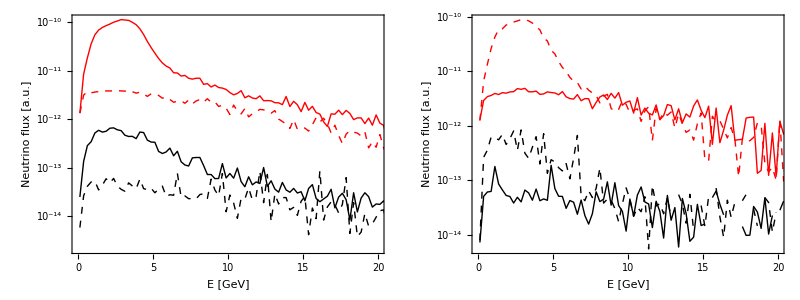

```mathematica
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ListLogPlot[Table[{#⟦1⟧,#⟦j⟧}&/@Data[i],{j,2,7}],Joined->True,PlotRange->{{0,20},All},
PlotStyle->{Directive[Black,Thick],Directive[Red,Thick],Directive[Blue,Thick],
Directive[Black,Dashed],Directive[Red,Dashed],Directive[Blue,Dashed]},FrameLabel->{"E [GeV]", "Neutrino flux [a.u.]"}];
];
Grid[{{MyPlot[1],MyPlot[2]}}]
```

#### Correct FD flux by using FD/ND ratio from Alex Sousa's histograms (DOESN'T REALLY LEAD TO AN IMPROVEMENT)

```mathematica
TotalFluxND=Cases[Import["0-code/glb/minos-nc/data/MINOS-total-flux-near.dat","Table"],{Repeated[_?NumericQ]}];
TotalFluxNDInterpol=Interpolation[TotalFluxND,InterpolationOrder->1];
TotalFluxFD=Cases[Import["0-code/glb/minos-nc/data/MINOS-total-flux-far.dat","Table"],{Repeated[_?NumericQ]}];
TotalFluxFDInterpol=Interpolation[TotalFluxFD,InterpolationOrder->1];
ConvertFlux[En_,x_]:=If[TotalFluxNDInterpol[En]==0,0,x*TotalFluxFDInterpol[En]/TotalFluxNDInterpol[En]];
For[i=1,i≤Length[DataFiles],i++,
DataFD[i]=Flatten[{#⟦1⟧,ConvertFlux[#⟦1⟧,#⟦2⟧],ConvertFlux[#⟦1⟧,#⟦3⟧],ConvertFlux[#⟦1⟧,#⟦4⟧],ConvertFlux[#⟦1⟧,#⟦5⟧],ConvertFlux[#⟦1⟧,#⟦6⟧],ConvertFlux[#⟦1⟧,#⟦7⟧]}]&/@Data[i];
Export[StringReplace[DataFiles⟦i⟧,".txt"->"-FD.txt"],DataFD[i],"Table"];
];
```

InterpolatingFunction::dmval: Input value {0.125`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

#### Correct fluxes by using ratio of Alex Sousa's histograms and ours (GIVES WRONG RESULTS SINCE NC SAMPLE FAVORS HIGHER ENERGIES)

```mathematica
TotalFluxND=Cases[Import["0-code/glb/minos-nc/data/MINOS-total-flux-near.dat","Table"],{Repeated[_?NumericQ]}];
TotalFluxNDInterpol=Interpolation[TotalFluxND,InterpolationOrder->1];
TotalFluxFD=Cases[Import["0-code/glb/minos-nc/data/MINOS-total-flux-far.dat","Table"],{Repeated[_?NumericQ]}];
TotalFluxFDInterpol=Interpolation[TotalFluxFD,InterpolationOrder->1];

i=1;
CorrectFlux[NormFlux_]:=Module[{Norm1,Norm2,tab},
Norm1=Total[Total[Data[i]⟦All,2;;-1⟧]];
Norm2=0.0;
tab=Table[
x=Total[Data[i]⟦j,2;;-1⟧];
Norm2+=NormFlux[Data[i]⟦j,1⟧];
{Data[i]⟦j,1⟧,If[x==0,{0,0,0,0,0,0},Data[i]⟦j,2;;-1⟧*NormFlux[Data[i]⟦j,1⟧]/x]},{j,1,Length[Data[i]]}];
Return[Flatten[{#⟦1⟧,#⟦2⟧*Norm1/Norm2}]&/@tab];
];
DataCorrectedND[i]=CorrectFlux[TotalFluxNDInterpol];
DataCorrectedFD[i]=CorrectFlux[TotalFluxFDInterpol];
Export[StringReplace[DataFiles⟦i⟧,".txt"->"-ND.txt"],DataCorrectedND[i],"Table"];
Export[StringReplace[DataFiles⟦i⟧,".txt"->"-FD.txt"],DataCorrectedFD[i],"Table"];
```

InterpolatingFunction::dmval: Input value {0.125`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.375`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.125`} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.375`} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

### Create dummy cross section file

```mathematica
XSTable=Table[Flatten[N[Round[{logE,ConstantArray[1./10^logE,6]},10^-5]]],{logE,-1,3,0.01}];
Export["0-code/glb/minos-nc/XFlat.dat",XSTable,"Table"];
```

### Re-interpolate smearing matrices

```mathematica
DataFiles=Union[FileNames["0-code/glb/minos-nc/data/nc_smear*"]];
Emin=0.5;
BinsReco=Flatten[{ConstantArray[0.125,60],ConstantArray[2,24],4}];
BinCentersReco=Table[Emin+Total[BinsReco⟦1;;k-1⟧]+BinsReco⟦k⟧/2,{k,1,Length[BinsReco]}];
BinsRaw=Flatten[{ConstantArray[0.125,60],ConstantArray[2,26]}];
BinCentersRaw=Table[Emin+Total[BinsRaw⟦1;;k-1⟧]+BinsRaw⟦k⟧/2,{k,1,Length[BinsRaw]}];
NData=Length[DataFiles];
Clear[S,s];
For[i=1,i≤NData,i++,
Data[i]=Import[DataFiles⟦i⟧,"Table","FieldSeparators"->{","," "},"CurrencyTokens"->{{"{","}:","};","}",",",":"},{"{","}:","};","}",",",":"}}];
Data[i]=Select[Cases[#,_Real|_Integer]&/@Data[i],Length[#]>0&];

S[i]=Array[s[i],{Length[Data[i]],Max[Data[i]⟦All,2⟧]+1}];
s[i][n_,m_]:={BinCentersReco⟦n⟧,BinCentersRaw⟦m⟧,0};
For[n=1,n≤Length[S[i]],n++,
For[m=Data[i]⟦n,1⟧+1,m≤Data[i]⟦n,2⟧+1,m++,
s[i][n,m]={BinCentersReco⟦n⟧,BinCentersRaw⟦m⟧,Data[i]⟦n,m-Data[i]⟦n,1⟧+2⟧/BinsReco⟦n⟧};
];
];
SmearInterpol[i]=Interpolation[Flatten[S[i],1],InterpolationOrder->1];
];
```

```mathematica
Integrate[SmearInterpol[1][Ereco,Eraw]/.Eraw->30,{Ereco,0,60}]
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 60 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

1.00087

InterpolatingFunction::dmval: Input value {0.0010214285714285714`, 25} lies outside the range of data in the interpolating function. Extrapolation will be used.

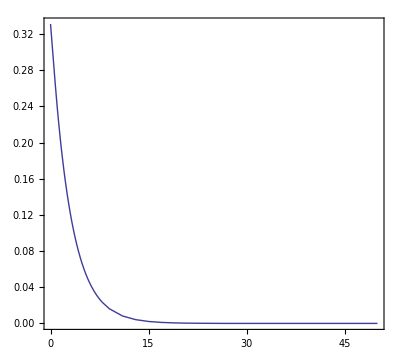

```mathematica
Plot[SmearInterpol[1][Ereco,Eraw]/.Eraw->25,{Ereco,0,50}]
```

```mathematica
MINOSEmin=0;
MINOSBinsRaw=ConstantArray[1,40];
MINOSBinsReco=ConstantArray[1,40];
MINOSBinCentersReco=Table[MINOSEmin+Total[MINOSBinsReco⟦1;;k-1⟧]+MINOSBinsReco⟦k⟧/2.,{k,1,Length[MINOSBinsReco]}];
MINOSBinCentersRaw=Table[MINOSEmin+Total[MINOSBinsRaw⟦1;;k-1⟧]+MINOSBinsRaw⟦k⟧/2.,{k,1,Length[MINOSBinsRaw]}];
MINOSSmear=Table[NIntegrate[SmearInterpol[1][Ereco,MINOSBinCentersRaw⟦m⟧],{Ereco,MINOSBinCentersReco⟦n⟧-MINOSBinsReco⟦n⟧/2.,MINOSBinCentersReco⟦n⟧+MINOSBinsReco⟦n⟧/2.}],{n,1,Length[MINOSBinsReco]},{m,1,Length[MINOSBinsRaw]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ereco near {Ereco} = {1.9791269479150333`}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ereco near {Ereco} = {2.979126947915033`}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

```mathematica
OutStr="energy(#ERES_NC)<\n";
OutStr=OutStr<>"  @energy =\n";
For[n=1,n≤Length[MINOSBinsReco],n++,
OutStr=OutStr<>"{ 0, "<>ToString[Length[MINOSBinsRaw]-1];
For[m=1,m≤Length[MINOSBinsRaw],m++,
OutStr=OutStr<>", "<>ToString[FortranForm[MINOSSmear⟦n,m⟧]];
];
If[n<Length[MINOSBinsReco],OutStr=OutStr<>"}:\n"];
];
OutStr=OutStr<>"};\n>";
Export["0-code/glb/minos-nc/smear_NC_lbne.dat",OutStr];
```

### Convert purities to background efficiencies

FIXME : For the ND, we use the purity from Alex Sousa's MC; for the FD we could continue to use the old purity from 1001.0336 since it turns out to give better agreement with the data and MINOS MC (not sure why this is the case).

```mathematica
DataFiles="1-spectra/"<>#&/@{"minos-nc-near-noosc.dat","minos-cc-near-noosc.dat","minos-nc-far-noosc.dat","minos-cc-far-noosc.dat"};
DataFilesPur="0-code/glb/minos-nc/data/"<>#&/@{"NC-pur-near-nu2010.dat","CC-pur-near.dat","NC-pur-far-nu2010.dat","CC-pur-far.dat"};
For[i=1,i≤Length[DataFiles],i++,
DataSig[i]=glbSignalTot[Get[DataFiles⟦i⟧]];
DataBG[i]=glbBGTot[Get[DataFiles⟦i⟧]];
DataPur[i]=Cases[Import[DataFilesPur⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
DataPurInterpol[i]=Interpolation[DataPur[i],InterpolationOrder->1];

Eff[i]=Table[En=DataSig[i]⟦j,1⟧;p=DataPurInterpol[i][En];
DataSig[i]⟦j,2⟧/DataBG[i]⟦j,2⟧*(1-p)/p,{j,1,Length[DataSig[i]]}];
];
Print["ND, CC BG in NC sample:\n",Eff[1]];
Print["ND, NC BG in CC sample:\n",Eff[2]];
Print["FD, CC BG in NC sample:\n",Eff[3]];
Print["FD, NC BG in CC sample:\n",Eff[4]];
```

ND, CC BG in NC sample:
{1.12466,0.435997,0.318037,0.309596,0.328685,0.345146,0.356098,0.337814,0.300697,0.28817,0.266693,0.249046,0.245356,0.224797,0.216089,0.206548,0.197618,0.198483,0.190414,0.185443}

ND, NC BG in CC sample:
{4.04701×10^-7,7.98211×10^-7,4.52343×10^-7,3.87917×10^-7,5.80404×10^-7,9.06235×10^-7,1.2551×10^-6,1.58662×10^-6,1.72093×10^-6,1.9359×10^-6,2.3753×10^-6,2.89925×10^-6,3.4374×10^-6,4.09129×10^-6,4.8391×10^-6,5.83318×10^-6,6.14974×10^-6,7.35302×10^-6,8.47596×10^-6,0.0000101564}

FD, CC BG in NC sample:
{0.91157,0.354907,0.253365,0.25827,0.305747,0.396002,0.50077,0.558518,0.580881,0.603479,0.60703,0.630974,0.622166,0.628168,0.639896,0.624359,0.633535,0.6293,0.62291,0.621873}

FD, NC BG in CC sample:
{1.83283×10^-7,4.78383×10^-7,4.35965×10^-7,3.48988×10^-7,3.55207×10^-7,4.82656×10^-7,5.9299×10^-7,7.31885×10^-7,8.81507×10^-7,9.62447×10^-7,9.97738×10^-7,1.01635×10^-6,9.88418×10^-7,9.68773×10^-7,8.65649×10^-7,9.175×10^-7,1.04254×10^-6,1.06335×10^-6,1.19582×10^-6,1.36735×10^-6}

### Event spectra

```mathematica
DataFiles={"minos-nc-near.dat","minos-cc-near.dat","minos-nc-far.dat","minos-cc-far.dat",
{"minos-th13.dat",{1,1}},{"minos-th13.dat",{1,2}},{"minos-th13.dat",{2,1}},{"minos-th13.dat",{2,2}},
{"minos-th24.dat",{1,1}},{"minos-th24.dat",{1,2}},{"minos-th24.dat",{2,1}},{"minos-th24.dat",{2,2}},
{"minos-th34.dat",{1,1}},{"minos-th34.dat",{1,2}},{"minos-th34.dat",{2,1}},{"minos-th34.dat",{2,2}},
{"minos-bf-thomas.dat",{1,1}},{"minos-bf-thomas.dat",{1,2}},{"minos-bf-thomas.dat",{2,1}},{"minos-bf-thomas.dat",{2,2}}}/.s_String:>"1-spectra/"<>s;
DataFilesMINOS={"NC-spectrum-near-nu2010.dat","CC-spectrum-near.dat","NC-spectrum-far-nu2010.dat","CC-spectrum-far.dat"}/.s_String:>"0-code/glb/minos-nc/data/"<>s;
MyPlotLabels={"Near detector NC","Near detector CC","Far detector NC","Far detector CC"};
For[i=1,i≤Length[DataFiles],i++,
If[Head[DataFiles⟦i⟧]===List,
Data[i]=ToExpression[StringReplace[Import[DataFiles⟦i,1⟧,"Text"],RegularExpression["#.*\n"]->""]]⟦Sequence@@DataFiles⟦i,2⟧⟧,
(* Else *)
Data[i]=Get[DataFiles⟦i⟧];
];
EventsSignal[i]=glbSignalTot[Data[i]];
EventsBG[i]=glbBGTot[Data[i]];
EventsTotal[i]=glbSignalBGTot[Data[i]];
BinSizes[i]=Function[x,First[Select[{0.125,0.25,0.5,1,2,4,8},FractionalPart[1/#(x+#/2)]<1*^-10&]]]/@EventsSignal[i]⟦All,1⟧;

If[Mod[i,4]==3||Mod[i,4]==0,
EventsTotal[i]=Table[{EventsTotal[i]⟦k,1⟧,EventsTotal[i]⟦k,2⟧*DataObs[i-2]⟦k,2⟧/EventsTotal[i-2]⟦k,2⟧},{k,1,Length[EventsTotal[i]]}]
];

DataMINOS[i]=Cases[Import[DataFilesMINOS⟦Mod[i-1,4]+1⟧,"Table"],{Repeated[_?NumericQ]}];
DataObs[i]=DataMINOS[i]⟦All,{1,2}⟧;
DataMC[i]=DataMINOS[i]⟦All,{1,3}⟧;
DataBGMC[i]=DataMINOS[i]⟦All,{1,4}⟧;
];
```

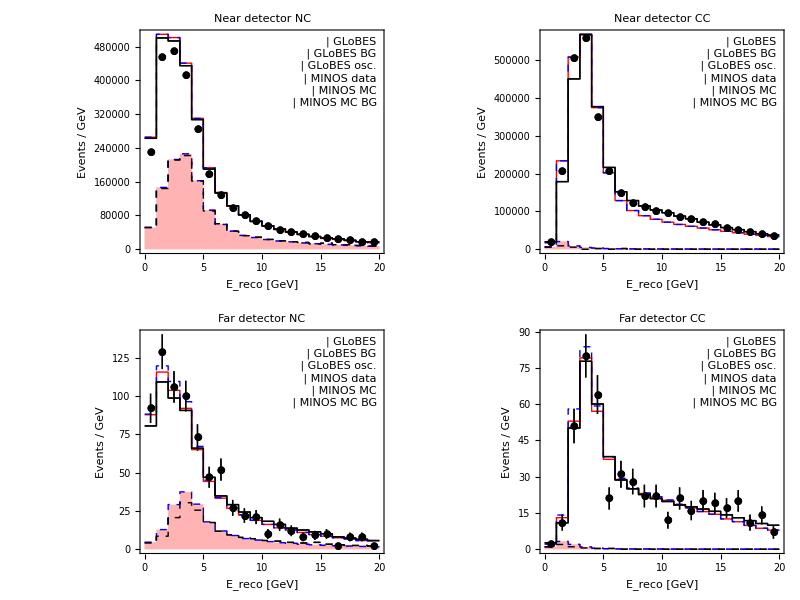

```mathematica
MyLegend=Framed[Grid[{
{LegendLine[Directive[Thick,Red]],"GLoBES"},
{LegendBox[RGBColor[1,.7,.7],Directive[Thick,Red,Dashed]],"GLoBES BG"},
{LegendLine[Directive[Thick,Blue,Dashed]],"GLoBES osc."},
{LegendDataPoint[PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}],"MINOS data"},
{LegendLine[Directive[Thick,Black]],"MINOS MC"},
{LegendLine[Directive[Thick,Black,Dashed]],"MINOS MC BG"}
},Spacings->{Automatic,Automatic}, Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];
For[i=1,i≤Length[DataFiles],i++,
PlotListObs={{#⟦1⟧,#⟦2⟧},ErrorBar[Sqrt[#⟦2⟧]]}&/@DataObs[i];
MyPlotObs[i]=ErrorListPlot[PlotListObs,PlotRange->All,PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}];

PlotListMCBG=Table[x=DataBGMC[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListMCBG,{PlotListMCBG⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListMCBG⟦-1,2⟧}];
MyPlotMCBG[i]=ListPlot[PlotListMCBG,PlotStyle->Directive[Thick,Black,Dashed],Joined->True,InterpolationOrder->0];

PlotListMC=Table[x=DataMC[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListMC,{PlotListMC⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListMC⟦-1,2⟧}];
MyPlotMC[i]=ListPlot[PlotListMC,PlotStyle->Directive[Thick,Black],Joined->True,InterpolationOrder->0];

PlotListTotal[i]=Table[x=EventsTotal[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListTotal[i],{PlotListTotal[i]⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListTotal[i]⟦-1,2⟧}];
MyPlotTotal[i]=ListPlot[PlotListTotal[i],PlotStyle->Directive[Thick,If[i≤4,Red,Directive[Blue,Dashed]]],Joined->True,InterpolationOrder->0];

PlotListBG[i]=Table[x=EventsBG[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[EventsBG[i]]}];
AppendTo[PlotListBG[i],{PlotListBG[i]⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListBG[i]⟦-1,2⟧}];
MyPlotBG[i]=ListPlot[PlotListBG[i],PlotStyle->Directive[If[i≤4,Red,Blue],Thick,Dashed],Joined->True,InterpolationOrder->0,Filling->{{1->{0,RGBColor[1,.7,.7]}}}];

MyPlot[i]=Show[{MyPlotTotal[i],MyPlotBG[i],MyPlotMCBG[i],MyPlotMC[i],MyPlotObs[i]},FrameLabel->{"E_reco [GeV]","Events / GeV"},PlotLabel->MyPlotLabels⟦Mod[i-1,4]+1⟧,Epilog->{Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}]}];
];
k=4;
Grid[{{Show[MyPlot[1],MyPlot[1+k]],Show[MyPlot[2],MyPlot[2+k]]},{Show[MyPlot[3],MyPlot[3+k]],Show[MyPlot[4],MyPlot[4+k]]}}]
If[SaveFigures,
Export["fig/spectra.eps",%];
];
```

### Fit results (verification of CC fit)

```mathematica
MINOSContoursRaw=Get["0-code/glb/minos/data/minos-contours.dat"];
BestFitNu=MINOSContoursRaw⟦1,1⟧;
Nu90=MINOSContoursRaw⟦2⟧;
Nu68=MINOSContoursRaw⟦3⟧;
BestFitNuBar=MINOSContoursRaw⟦4,1⟧;
NuBar90=MINOSContoursRaw⟦5⟧;
NuBar68=MINOSContoursRaw⟦6⟧;

i=1;
Data[i]=Cases[Import["2-smparams/th23dm31-minos.dat"],{Repeated[_Real|_Integer]}];
Data[i]={Sin[2#⟦1⟧]^2,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Data[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
```

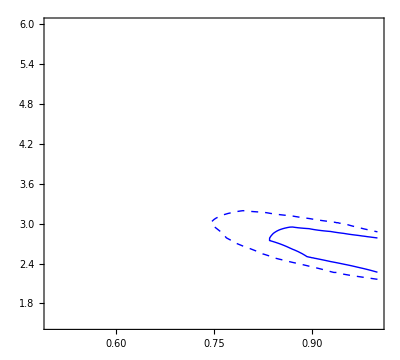

```mathematica
ContourPlot[DataInterpol[i][s22th13,dm31*1*^-3]-Chi2Min[i],{s22th13,0.5,1},{dm31,1.5,6},Contours->{χ2[2,0.32],χ2[2,0.1]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]}]
```

### Fit results (sterile neutrino fit)

```mathematica
ParamLabels={"θ_23 [degrees]","θ_34 [degrees]","θ_24 [degrees]"};
DataFiles="3-3p1/"<>#&/@{"th23th34th24-minos-th13-0.dat","th23th34th24-minos-th13-12deg.dat"};
DataFilesMINOS=Map["0-code/glb/minos-nc/data/"<>#&,{{"fit-m4ggm3-th23-A.dat","fit-m4ggm3-th34-A.dat","fit-m4ggm3-th24-A.dat"},{"fit-m4ggm3-th23-B.dat","fit-m4ggm3-th34-B.dat","fit-m4ggm3-th24-B.dat"}},{-1}];
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
For[j=1,j≤Length[Data[1]⟦1⟧]-1,j++,
DataProj[i,j]={#⟦1,j⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦j⟧==#2⟦j⟧&];
DataProjInterpol[i,j]=Interpolation[DataProj[i,j],InterpolationOrder->1];
xmin[i,j]=Min[Data[i]⟦All,j⟧];
xmax[i,j]=Max[Data[i]⟦All,j⟧];
];
];
For[i=1,i≤Length[DataFilesMINOS],i++,
For[j=1,j≤Length[DataFilesMINOS⟦i⟧],j++,
DataMINOS[i,j]=Cases[Import[DataFilesMINOS⟦i,j⟧,"Table"],{Repeated[_?NumericQ]}];
];
];
```

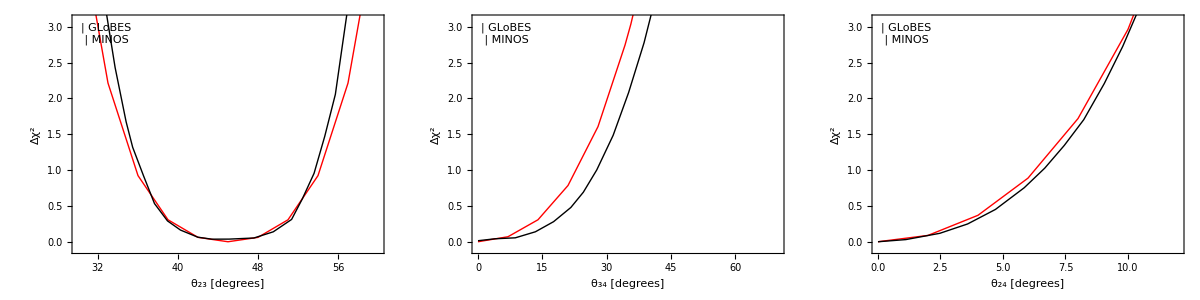

```mathematica
i=1;
MyLegend=Framed[Grid[{
{LegendLine[Directive[Thick,Red]],"GLoBES"},
{LegendLine[Directive[Thick,Black]],"MINOS"}
},Spacings->{Automatic,Automatic}, Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];
For[j=1,j≤Length[Data[1]⟦1⟧]-1,j++,
MyPlot[i,j]=Show[
Plot[DataProjInterpol[i,j][x Degree]-Chi2Min[i],{x,xmin[i,j]/Degree,xmax[i,j]/Degree},PlotStyle->Directive[Thick,Red]],
ListPlot[DataMINOS[i,j],Joined->True,PlotStyle->Directive[Thick,Black]],
PlotRange->{-0.1,3.1},FrameLabel->{ParamLabels⟦j⟧,"Δχ^2"},Epilog->{Inset[MyLegend,Scaled[{0.03,0.97}],{-1,1}]}
]
];
Grid[{{MyPlot[i,1],MyPlot[i,2],MyPlot[i,3]}}]
If[SaveFigures,
Export["fig/fits.eps",%];
];
```

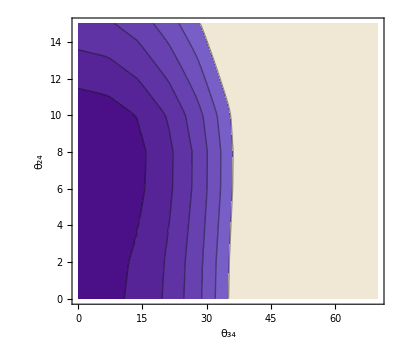

```mathematica
i=1;
DataProjTest={#⟦1,2⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{2,3}⟧==#2⟦{2,3}⟧&];
DataProjTestInterpol=Interpolation[DataProjTest,InterpolationOrder->1];
ContourPlot[DataProjTestInterpol[x Degree,y Degree]-Chi2Min[i],{x,0,70},{y,0,15},FrameLabel->{"θ_34","θ_24"},Contours->{0.5,1,1.5,2,2.5,3}]
```

## MINOS — 1003.0336 + 1103.0340

### Beam fluxes

```mathematica
DataFiles={
"0-code/glb/minos-nc/flugg_le010z185i_run1_735km_0kmoa_flux.txt",
"0-code/glb/minos-nc/flugg_le010z-185i_run4_735km_0kmoa_flux.txt"
};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Import[DataFiles⟦i⟧,"Table"];
];
```

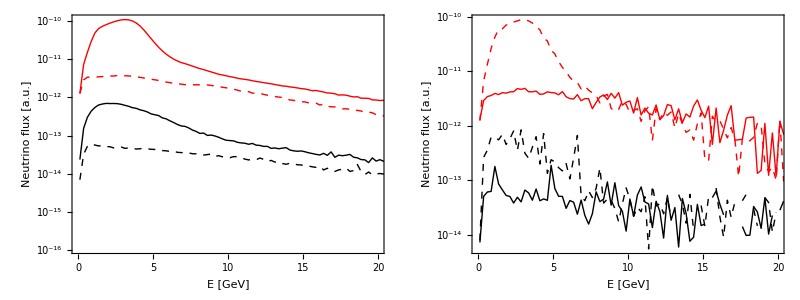

```mathematica
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i]=ListLogPlot[Table[{#⟦1⟧,#⟦j⟧}&/@Data[i],{j,2,7}],Joined->True,PlotRange->{{0,20},All},
PlotStyle->{Directive[Black,Thick],Directive[Red,Thick],Directive[Blue,Thick],
Directive[Black,Dashed],Directive[Red,Dashed],Directive[Blue,Dashed]},FrameLabel->{"E [GeV]", "Neutrino flux [a.u.]"}];
];
Grid[{{MyPlot[1],MyPlot[2]}}]
```

### Preparation of input files

#### Rebinning of event spectra

NOTE : Run Event spectra code first for proper initialization

```mathematica
DataMINOS[i]=Cases[Import[DataFilesMINOS⟦Mod[i-1,4]+1⟧,"Table"],{Repeated[_?NumericQ]}];
DataObs[i]=DataMINOS[i]⟦All,{1,2}⟧;
DataMC[i]=DataMINOS[i]⟦All,{1,3}⟧;
DataBGMC[i]=DataMINOS[i]⟦All,{1,4}⟧;

(* CC ND data *)
Make1GeVBins[DataObs[2]]⟦All,2⟧

(* CC FD data *)
Make1GeVBins[DataObs[4]]⟦All,2⟧
```

{79474.4,1.08292×10^6,2.75959×10^6,2.9265×10^6,1.66333×10^6,957837.,722416.,638357.,582196.,526039.,477828.,429627.,393376.,361109.,320876.,280643.,248376.,220098.,199777.,175483.}

{8.59002,28.308,145.64,237.007,175.705,94.8805,86.2907,89.0238,92.9283,89.0239,86.6811,64.8156,68.7202,51.5401,56.2256,63.2538,46.8547,42.9501,40.6074,32.7983,163.991,109.328}

#### Compute background efficiencies

USAGE: Run event spectra code first for proper initialization. Then, run
  globes -s -c3 -m minos-cc-far.glb > minos-cc-far-NCnoeff.dat
to get rates for NC channel with *no* efficiencies. Finally, run the following code and copy the output back to the glb file.

```mathematica
i=4;
Data[i]=Get["1-spectra/minos-cc-far-NCnoeff.dat"]⟦1⟧;
(DataBGMC[i]⟦1;;Length[Data[i]]⟧/Data[i])⟦All,2⟧
```

{2.11933×10^-7,3.66763×10^-7,4.79433×10^-7,6.13481×10^-7,9.85216×10^-7,2.08878×10^-6,2.97771×10^-6,2.77602×10^-6,6.9601×10^-6,5.52704×10^-6,7.25806×10^-6,0.0000158291,0.,0.,0.,0.,0.,0.,0.,0.}

#### Efficiencies for CC events

USAGE:
- Remove efficiencies from CC channels in glb files and compute event spectra
- Run event spectra code for proper initialization.
- Then, run the code below for the *near detector* and copy the result into the glb file as @post_smearing_efficiencies
- Compute event spectra again (*without oscillations*) and run event spectra code below again. Near detector prediction should now coincide exactly with MINOS MC prediction
- Run code for *far detector* and copy the result into the glb file as @post_smearing_efficiencies

```mathematica
i=2;
Print["Near: ",(DataMC[i]⟦1;;Length[EventsTotal[i]]⟧/EventsTotal[i])⟦All,2⟧];
i=4;
n=Length[EventsTotal[i]];
Print["Far: ",(DataMC[i]⟦1;;n,2⟧-DataBGMC[i]⟦1;;n,2⟧)/(EventsTotal[i]⟦All,2⟧-DataBGMC[i]⟦1;;n,2⟧)];
```

Near: {0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,1.,1.,1.,1.,1.,1.}

Far: {0.294003,0.685595,0.698816,0.613537,0.640051,0.83512,1.00646,1.05674,1.09238,1.16574,1.16659,1.20161,1.20245,1.14027,1.13093,1.15642,1.16221,1.12668,1.10608,1.15491}

### Event spectra

```mathematica
DataFiles={"minos-nc-near","minos-cc-near","minos-nc-far","minos-cc-far",
{"minos-th24",{2,1}},{"minos-th24",{4,1}},{"minos-th24",{1,1}},{"minos-th24",{3,1}}}/.s_String:>"1-spectra/"<>s<>".dat";
DataFilesMINOS={"NC-spectrum-near-nu2010.dat","cc-1103.0340-nd.dat","NC-spectrum-far-nu2010.dat","cc-1103.0340-fd.dat"}/.s_String:>"0-code/glb/minos-nc/data/"<>s;
MyPlotLabels={"Near detector NC","Near detector CC","Far detector NC","Far detector CC"};
For[i=1,i≤Length[DataFiles],i++,
If[Head[DataFiles⟦i⟧]===List,
Data[i]=ToExpression[StringReplace[Import[DataFiles⟦i,1⟧,"Text"],RegularExpression["#.*\n"]->""]]⟦Sequence@@DataFiles⟦i,2⟧⟧,
(* Else *)
Data[i]=Get[DataFiles⟦i⟧];
];
EventsSignal[i]=glbSignalTot[Data[i]];
EventsBG[i]=glbBGTot[Data[i]];
EventsTotal[i]=glbSignalBGTot[Data[i]];

GetBinWidths[s_]:=Module[{t,j},(* This works only if the lower boundary of the 1st bin is at 0 *)
t={2*s⟦1⟧};
For[j=1,j≤Length[s]-1,j++,
AppendTo[t,2*Differences[s]⟦j⟧-t⟦j⟧];
];
Return[t];
];
BinSizes[i]=GetBinWidths[EventsSignal[i]⟦All,1⟧];

(* Load data from published MINOS plots *)
DataMINOS[i]=Cases[Import[DataFilesMINOS⟦Mod[i-1,4]+1⟧,"Table"],{Repeated[_?NumericQ]}];
DataObs[i]=DataMINOS[i]⟦All,{1,2}⟧;
DataMC[i]=DataMINOS[i]⟦All,{1,3}⟧;
DataBGMC[i]=DataMINOS[i]⟦All,{1,4}⟧;
If[Length[DataMINOS[i]⟦1⟧]>4,
DataMCosc[i]=DataMINOS[i]⟦All,{1,5}⟧;
];
];

(* Combine data into 1 GeV bins for CC ND data *)
Make1GeVBins[X_]:=Module[{j,bb,t,res},
res={};
bb=Accumulate[GetBinWidths[X⟦All,1⟧]];
t=0.0;
For[j=1,j≤Length[X],j++,
t+=X⟦j,2⟧;
If[FractionalPart[bb⟦j⟧]<1*^-10,
AppendTo[res,{bb⟦j⟧-0.5,t}];
t=0.0;
]; (* If *)
]; (* For *)
Return[res];
]; (* Module *)

Do[
DataObs[i]=Make1GeVBins[DataObs[i]];
DataMC[i]=Make1GeVBins[DataMC[i]];
DataBGMC[i]=Make1GeVBins[DataBGMC[i]];
If[Length[DataMINOS[i]⟦1⟧]>4,
DataMCosc[i]=Make1GeVBins[DataMCosc[i]];
];
(*EventsTotal[i]=Make1GeVBins[EventsTotal[i]];
EventsSignal[i]=Make1GeVBins[EventsSignal[i]];
EventsBG[i]=Make1GeVBins[EventsBG[i]];
BinSizes[i]=ConstantArray[1,Length[DataObs[i]]];*)
,{i,{2,4,6,8}}];

(* Near-far extrapolation *)
Do[
EventsTotal[i]=Table[{EventsTotal[i]⟦k,1⟧,EventsTotal[i]⟦k,2⟧*DataObs[i-2]⟦k,2⟧/EventsTotal[i-2]⟦k,2⟧},{k,1,Length[DataObs[i-2]]}];
BinSizes[i]=BinSizes[i-2];
,{i,{3,4,7,8}}];
```

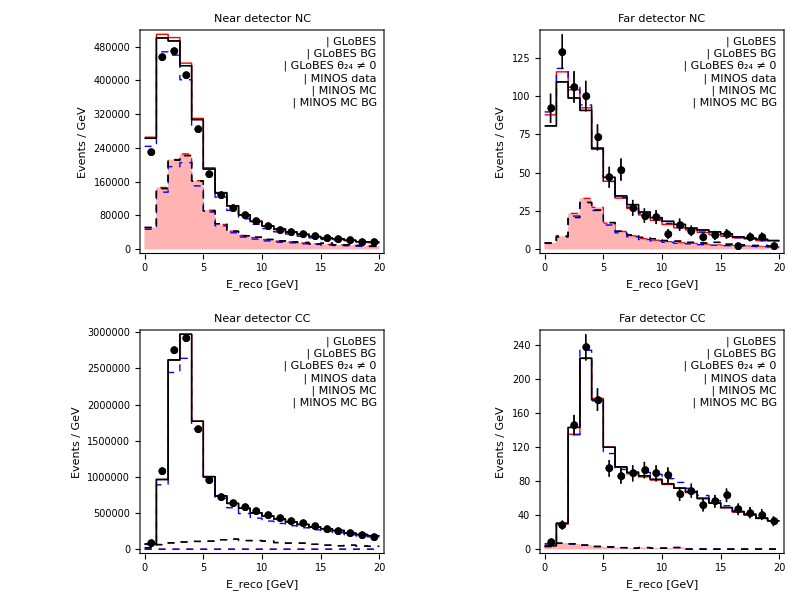

```mathematica
MyLegend=Framed[Grid[{
{LegendLine[Directive[Thick,Red]],"GLoBES"},
{LegendBox[RGBColor[1,.7,.7],Directive[Thick,Red,Dashed]],"GLoBES BG"},
{LegendLine[Directive[Thick,Blue,Dashed]],"GLoBES θ_24 ≠ 0"},
{LegendDataPoint[PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}],"MINOS data"},
{LegendLine[Directive[Thick,Black]],"MINOS MC"},
{LegendLine[Directive[Thick,Black,Dashed]],"MINOS MC BG"}
},Spacings->{Automatic,Automatic}, Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];
For[i=1,i≤Length[DataFiles],i++,
(* MINOS data *)
PlotListObs[i]={{#⟦1⟧,#⟦2⟧},ErrorBar[Sqrt[#⟦2⟧]]}&/@DataObs[i];
PlotListObs[i]=Table[{{DataObs[i]⟦k,1⟧,DataObs[i]⟦k,2⟧/BinSizes[i]⟦k⟧},ErrorBar[Sqrt[DataObs[i]⟦k,2⟧]/BinSizes[i]⟦k⟧]},{k,1,Length[BinSizes[i]]}];
MyPlotObs[i]=ErrorListPlot[PlotListObs[i],PlotRange->All,PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}];

(* MINOS BG predictions *)
PlotListMCBG[i]=Table[x=DataBGMC[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListMCBG[i],{PlotListMCBG[i]⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListMCBG[i]⟦-1,2⟧}];
MyPlotMCBG[i]=ListPlot[PlotListMCBG[i],PlotStyle->Directive[Thick,Black,Dashed],Joined->True,InterpolationOrder->0];

(* MINOS total predictions *)
PlotListMC[i]=Table[x=DataMC[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListMC[i],{PlotListMC[i]⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListMC[i]⟦-1,2⟧}];
MyPlotMC[i]=ListPlot[PlotListMC[i],PlotStyle->Directive[Thick,Black],Joined->True,InterpolationOrder->0];

If[Length[DataMINOS[i]⟦1⟧]>4,
PlotListMCosc[i]=Table[x=DataMCosc[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListMCosc[i],{PlotListMCosc[i]⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListMCosc[i]⟦-1,2⟧}];
MyPlotMC[i]=ListPlot[PlotListMCosc[i],PlotStyle->Directive[Thick,Black],Joined->True,InterpolationOrder->0];
];

(* GLoBES total prediction *)
PlotListTotal[i]=Table[x=EventsTotal[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListTotal[i],{PlotListTotal[i]⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListTotal[i]⟦-1,2⟧}];
MyPlotTotal[i]=ListPlot[PlotListTotal[i],PlotStyle->Directive[Thick,If[i≤4,Red,Directive[Blue,Dashed]]],Joined->True,InterpolationOrder->0];

(* GLoBES BG prediction *)
PlotListBG[i]=Table[x=EventsBG[i]⟦k⟧;{x⟦1⟧-BinSizes[i]⟦k⟧/2,x⟦2⟧/BinSizes[i]⟦k⟧},{k,1,Length[BinSizes[i]]}];
AppendTo[PlotListBG[i],{PlotListBG[i]⟦-1,1⟧+BinSizes[i]⟦-1⟧,PlotListBG[i]⟦-1,2⟧}];
MyPlotBG[i]=ListPlot[PlotListBG[i],PlotStyle->Directive[If[i≤4,Red,Blue],Thick,Dashed],Joined->True,InterpolationOrder->0,Filling->{{1->{0,RGBColor[1,.7,.7]}}}];

MyPlot[i]=Show[{MyPlotTotal[i],MyPlotBG[i],MyPlotMCBG[i],MyPlotMC[i],MyPlotObs[i]},FrameLabel->{"E_reco [GeV]","Events / GeV"},PlotLabel->MyPlotLabels⟦Mod[i-1,4]+1⟧,Epilog->{Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}]}];
];
k=4;
Grid[{{Show[MyPlot[1],MyPlot[1+k]],Show[MyPlot[3],MyPlot[3+k]]},{Show[MyPlot[2],MyPlot[2+k]],Show[MyPlot[4],MyPlot[4+k]]}}]
(*Grid[{{MyPlot[1],MyPlot[3]},{MyPlot[2],MyPlot[4]}}]*)
If[SaveFigures,
Export["fig/minos-spectra.eps",%];
];
```

### Fit results (verification of CC fit)

```mathematica
MINOSContoursRaw=Get["0-code/glb/minos-nc/data/cc-contours-1103.0340.dat"];
BestFitNu=MINOSContoursRaw⟦1,1⟧;
Nu90=MINOSContoursRaw⟦2⟧;
Nu68=MINOSContoursRaw⟦3⟧;

i=1;
Data[i]=Cases[Import["2-smparams/th23dm31-minos.dat.gz"],{Repeated[_Real|_Integer]}];
Data[i]={Sin[2#⟦1⟧]^2,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Data[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
```

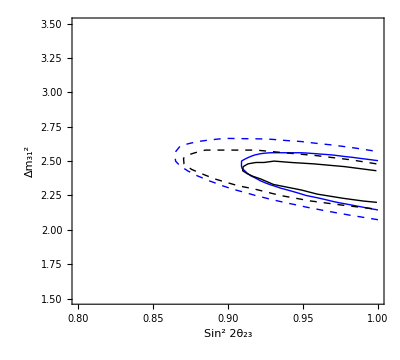

```mathematica
ContourPlot[DataInterpol[i][s22th13,dm31*1*^-3]-Chi2Min[i],{s22th13,0.8,1},{dm31,1.5,3.5},Contours->{χ2[2,0.32],χ2[2,0.1]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},
Epilog->{Line[{#⟦1⟧,#⟦2⟧*1000}&/@Nu68],Dashed,Line[{#⟦1⟧,#⟦2⟧*1000}&/@Nu90]},FrameLabel->{"Sin^2 2θ_23","Δm_31^2"}]
```

### Fit results (sterile neutrino fit)

```mathematica
ParamLabels={"θ_23 [degrees]","θ_34 [degrees]","θ_24 [degrees]"};
DataFiles="3-3p1/"<>#&/@{"th23th34th24-minos-th13-0-dm41-5-noNDosc.dat.gz","th23th34th24-minos-th13-12deg-dm41-5-noNDosc.dat.gz"};
DataFilesMINOS=Map["0-code/glb/minos-nc/data/"<>#&,{{"fit-m4ggm3-th23-A.dat","fit-m4ggm3-th34-A.dat","fit-m4ggm3-th24-A.dat"},{"fit-m4ggm3-th23-B.dat","fit-m4ggm3-th34-B.dat","fit-m4ggm3-th24-B.dat"}},{-1}];
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]=Flatten[{#⟦1;;-3⟧,Min[#⟦-2⟧,#⟦-1⟧]}]&/@Data[i];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧];
For[j=1,j≤Length[Data[1]⟦1⟧]-1,j++,
DataProj[i,j]={#⟦1,j⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦j⟧==#2⟦j⟧&];
DataProjInterpol[i,j]=Interpolation[DataProj[i,j],InterpolationOrder->1];
xmin[i,j]=Min[Data[i]⟦All,j⟧];
xmax[i,j]=Max[Data[i]⟦All,j⟧];
];
];
For[i=1,i≤Length[DataFilesMINOS],i++,
For[j=1,j≤Length[DataFilesMINOS⟦i⟧],j++,
DataMINOS[i,j]=Cases[Import[DataFilesMINOS⟦i,j⟧,"Table"],{Repeated[_?NumericQ]}];
];
];
```

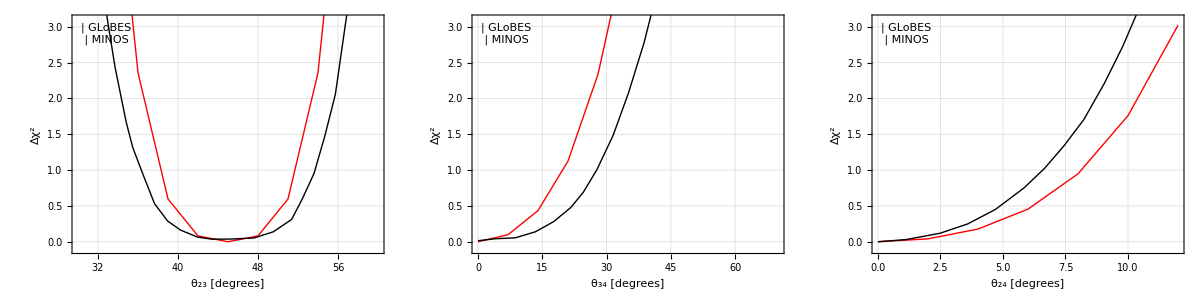

```mathematica
i=1;
MyLegend=Framed[Grid[{
{LegendLine[Directive[Thick,Red]],"GLoBES"},
{LegendLine[Directive[Thick,Black]],"MINOS"}
},Spacings->{Automatic,Automatic}, Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];
For[j=1,j≤Length[Data[1]⟦1⟧]-1,j++,
MyPlot[i,j]=Show[
Plot[DataProjInterpol[i,j][x Degree]-Chi2Min[i],{x,xmin[i,j]/Degree,xmax[i,j]/Degree},PlotStyle->Directive[Thick,Red]],
ListPlot[DataMINOS[i,j],Joined->True,PlotStyle->Directive[Thick,Black]],
PlotRange->{-0.1,3.1},FrameLabel->{ParamLabels⟦j⟧,"Δχ^2"},GridLines->Automatic,Epilog->{Inset[MyLegend,Scaled[{0.03,0.97}],{-1,1}]}
]
];
Grid[{{MyPlot[i,1],MyPlot[i,2],MyPlot[i,3]}}]
If[SaveFigures,
Export["fig/fits.eps",%];
];
```

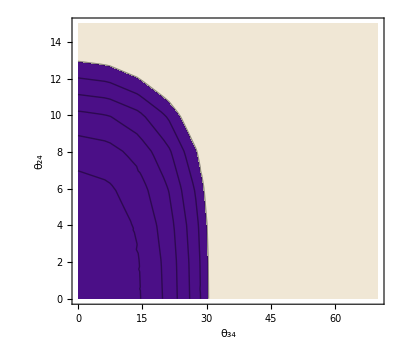

```mathematica
i=1;
DataProjTest={#⟦1,2⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{2,3}⟧==#2⟦{2,3}⟧&];
DataProjTestInterpol=Interpolation[DataProjTest,InterpolationOrder->1];
ContourPlot[DataProjTestInterpol[x Degree,y Degree]-Chi2Min[i],{x,0,70},{y,0,15},FrameLabel->{"θ_34","θ_24"},Contours->{0.5,1,1.5,2,2.5,3},PlotRange->All]
```

### The effect of the finite length of the decay pipe

```mathematica
(* Typical parent pion energy for given neutrino energy *)
(* Note: Neutrino momentum in pion rest frame given by PDG eq. 43.15 as (mπ^2-mμ^2)/(2mπ) *)
(mπ^2-mmu^2)/(2mπ)*γ(1-β Cos[θ])//.{γ->Eπ/mπ,β->Sqrt[1-1/γ^2],Cos[θ]->x}
1/2*Integrate[%,{x,-1,1}]
%//.MyNumbers
Eπ/%
```

(Eπ (-mmu^2+mπ^2) (1-√(1-mπ^2/Eπ^2) x))/(2 mπ^2)

1/2 (Eπ-(Eπ mmu^2)/mπ^2)

ReplaceRepeated::reps: {MyNumbers} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1/2 (Eπ-(Eπ mmu^2)/mπ^2)//.MyNumbers

Eπ/(1/2 (Eπ-(Eπ mmu^2)/mπ^2)//.MyNumbers)

```mathematica
$Assumptions={σE>0,En>0,Eprime>0};
Clear[σE,PInt3];
MyNumbers=Union[{
dmsq->10 eV^2,
L0->1.04km, (* Distance of ND from target *)
d->675meter, (* Length of decay pipe *)
τ0->7.8045meter*4.7En/mπ, (* Pion lifetime including rough estimate of boost factor, En=ν energy *)
mπ->139.57MeV},NN];
σE[E_]:=(*.07GeV(E/GeV)^2+*).5Min[1,τ0/L0]En//.Union[MyNumbers,{En->E}]
σE=-3GeV/(#/GeV)+2GeV&;

P=Sin[dmsq*L/(4En)]^2;
PP=P//.Union[MyNumbers,{L->Max[L0-d,L0-d/2],En->E0 GeV}];

PInt1=Integrate[P*1/(τ0(1-Exp[-d/τ0])) Exp[-(L0-L)/τ0],{L,L0-d,L0}];
PPInt1=PInt1//.Union[MyNumbers,{En->E0 GeV}];

(*PInt2[E0_]:=NIntegrate[Evaluate[P*1/τ0 L/E0 Exp[-(L0-L/E0*En)/τ0]//.Union[{L->L0},MyNumbers]],Evaluate[{En,(L0-d)/(L0-d/2)E0,L0/(L0-d/2)E0}//.MyNumbers]];

PInt3[E_]:=PInt3[E,dmsq//.MyNumbers,σE];
PInt3[E_,dmsq0_,σE_]:=NIntegrate[Evaluate[(P//.{L->Max[L0-d,L0-d/2],dmsq->dmsq0})*1/(Sqrt[2π]σE[E])Exp[-(E-En)^2/(2 σE[E]^2)]//.MyNumbers],{En,-∞,∞},Method->{"DoubleExponential","SymbolicProcessing"->0},PrecisionGoal->5]*)

PInt4[E_]:=PInt4[E,dmsq//.MyNumbers,σE]
PInt4[E_,dmsq_,σE_]:=1/2(1-Cos[dmsq L/(2E)]*Exp[-σE[E]^2*(dmsq L/(2E))^2/(2 E^2)])//.Union[MyNumbers,{L->Max[L0-d,L0-d/2]}];
```

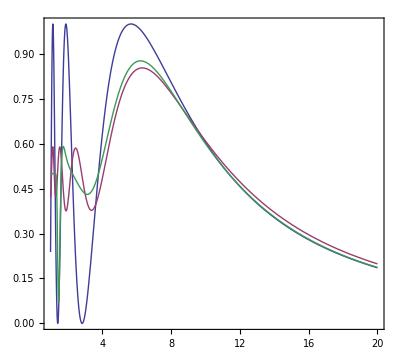

```mathematica
Plot[{PP,PPInt1,(*PInt2[E0 GeV],PInt3[E0 GeV]*),PInt4[E0 GeV]},{E0,1,20},PlotRange->{0,1}(*,MaxRecursion->3*)]
```

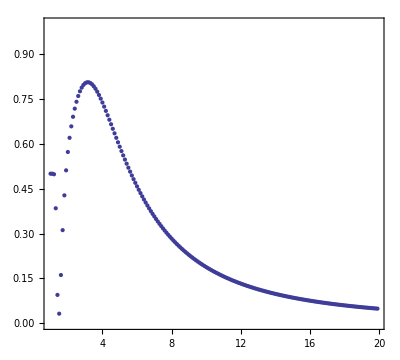

```mathematica
ListPlot[{#⟦1⟧,1-#⟦2⟧}&/@Cases[Import["ptest.dat"],{Repeated[_?NumericQ]}]⟦All,{1,2}⟧,PlotRange->{0,1}]
```

```mathematica
nI=40;
nJ=10;
PTable=Flatten[Table[{10^(0.+i*1./nI)GeV,0 eV^2+j*10.eV^2/nJ},{i,1,nI},{j,0,nJ}],1]//.MyNumbers;
PTable=Chop[{#⟦1⟧,#⟦2⟧,PInt1//.Union[{En->#⟦1⟧,dmsq->#⟦2⟧},MyNumbers]}]&/@PTable;
(*f=(x0+x1*(#/GeV)+x2*(#/GeV)^2(*+x3*(#/GeV)^3+x4*(#/GeV)^4*))GeV&;
MyFit=FindFit[PTable,PInt3[EE,dmsq,f],{{x0,.1},{x1,.1},{x2,.1}(*,{x3,.1},{x4,.1}*)},{EE,dmsq}]*)
f=(xm1/(#/GeV)+x0+0x1*(#/GeV)+0x2*(#/GeV)^2(*+x3*(#/GeV)^3+x4*(#/GeV)^4*))GeV&;
MyFit=FindFit[PTable,PInt4[EE,dmsq,f],{{x0,1},(*{x1,0},{x2,0},*){xm1,-1}},{EE,dmsq}]
```

{x0→47.2183,xm1→-8.42449}

General::unfl: Underflow occurred in computation.

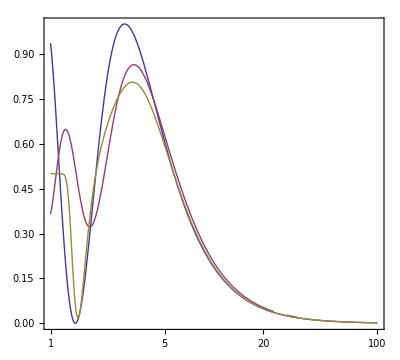

```mathematica
MyNumbers2=MyNumbers/.{(dmsq->__):>(dmsq->5 eV^2)};
f=-3GeV/(#/GeV)+2GeV&;
LogLinearPlot[{
P//.Union[MyNumbers2,{L->Max[L0-d,L0-d/2],En->E0 GeV}],
PInt1//.Union[MyNumbers2,{En->E0 GeV}],
PInt4[E0 GeV,dmsq//.MyNumbers2,f//.Union[MyFit,MyNumbers2]]},{E0,1,100},PlotRange->{0,1},MaxRecursion->3]
```

```mathematica
DataFiles=Union[FileNames["0-code/glb/minos-nc/smear_nc_mc-near-1001.0336.dat"]];
Emin=0;
BinsReco=ConstantArray[1.,20];
BinCentersReco=Table[Emin+Total[BinsReco⟦1;;k-1⟧]+BinsReco⟦k⟧/2,{k,1,Length[BinsReco]}];
BinsRaw=Flatten[{ConstantArray[0.25,40],ConstantArray[.5,40],ConstantArray[1,90]}];
BinCentersRaw=Table[Emin+Total[BinsRaw⟦1;;k-1⟧]+BinsRaw⟦k⟧/2,{k,1,Length[BinsRaw]}];
Clear[S,s];
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Import[DataFiles⟦i⟧,"Table","FieldSeparators"->{","," "},"CurrencyTokens"->{{"{","}:","};","}",",",":"},{"{","}:","};","}",",",":"}}];
Data[i]=Select[Cases[#,_Real|_Integer]&/@Data[i],Length[#]>0&];

S[i]=Array[s[i],{Length[Data[i]],Max[Data[i]⟦All,2⟧]+1}];
s[i][n_,m_]:={BinCentersReco⟦n⟧,BinCentersRaw⟦m⟧,0};
For[n=1,n≤Length[S[i]],n++,
For[m=Data[i]⟦n,1⟧+1,m≤Data[i]⟦n,2⟧+1,m++,
s[i][n,m]={BinCentersReco⟦n⟧,BinCentersRaw⟦m⟧,Data[i]⟦n,m-Data[i]⟦n,1⟧+2⟧/BinsReco⟦n⟧};
];
];
SmearInterpol[i]=Interpolation[Flatten[S[i],1],InterpolationOrder->1];
];
```

InterpolatingFunction::dmval: Input value {0.000408571, 10} lies outside the range of data in the interpolating function. Extrapolation will be used.

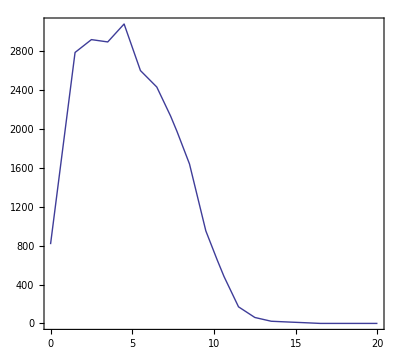

```mathematica
Plot[SmearInterpol[1][Ereco,Eraw]/.Eraw->10,{Ereco,0,20}]
```

## MINOS — 1607.01176

### Efficiencies

```mathematica
(1-pur)*(eSig*S+eBG*B)==eBG*B
eBG/.Solve[%,eBG]⟦1⟧

(* To obtain these numbers, compute event rates without efficiencies *)
%/.{pur->0.589,eSig->0.799,S->2.167*^6,B->7.8418*^6} (* NC near *)
%%/.{pur->0.613,eSig->0.876,S->740.5,B->1869} (* NC far *)
```

(1-pur) (B eBG+eSig S)==B eBG

-(eSig (-1+pur) S)/(B pur)

0.154069

0.219114

### Far/Near ratio

To compute energy-dependent efficiencies, set %eff_far to {1,1,...} in minos-cc/nc-far.glb, compute spectra, then run the code below to obtain Eff[1], Eff[2]

```mathematica
DataFilesMINOS=Join["0-code/glb/minos-2016/data/minos-"<>#<>"-1607.01176.dat"&/@{"cc","nc"},
{"0-code/glb/minos-2016/data/minos-spectrum-cc-1304.6335.dat"}];
For[i=1,i≤Length[DataFilesMINOS],i++,
DataMINOS[i]=Cases[Import[DataFilesMINOS⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
];
DataCC=DataMINOS[1];
DataNC=DataMINOS[2];

DataFilesGlb={"0-code/glb/minos-2016/minos-cc-far.glb","0-code/glb/minos-2016/minos-nc-far.glb"};
For[i=1,i≤Length[DataFilesGlb],i++,
(* Load glb file *)
GlbFile[i]=StringReplace[Import[DataFilesGlb⟦i⟧,"Text"],{RegularExpression["(?m)//.*$"]:>""}];

(* Extract bin sizes, sampling points, and energy window *)
Emin[i]=ToExpression[StringCases[GlbFile[i],RegularExpression["(?m)\\$emin\\s*=\\s*(.*)$"]->"$1"]⟦1⟧];
Emax[i]=ToExpression[StringCases[GlbFile[i],RegularExpression["(?m)\\$emax\\s*=\\s*(.*)$"]->"$1"]⟦1⟧];
BinSizes[i]=ToExpression[StringCases[GlbFile[i],RegularExpression["(?s)\\$binsize\\s*=\\s*({.*?})"]->"$1"]⟦1⟧];
BinCenters[i]=Emin[i]+Accumulate[BinSizes[i]]-BinSizes[i]/2;
BinBoundaries[i]=Join[{Emin[i]},Emin[i]+Accumulate[BinSizes[i]]];

SamplingMin[i]=StringCases[GlbFile[i],RegularExpression["(?m)\\$sampling_min\\s*=\\s*(.*)$"]->"$1"];
If[SamplingMin[i]=={},SamplingMin[i]=Emin[i],SamplingMin[i]=ToExpression[SamplingMin[i]⟦1⟧]];
SamplingMax[i]=StringCases[GlbFile[i],RegularExpression["(?m)\\$sampling_max\\s*=\\s*(.*)$"]->"$1"];
If[SamplingMax[i]=={},SamplingMax[i]=Emax[i],SamplingMax[i]=ToExpression[SamplingMax[i]⟦1⟧]];
SamplingBinSizes[i]=StringCases[GlbFile[i],RegularExpression["(?s)\\$sampling_stepsize\\s*=\\s*({.*?})"]->"$1"];
If[SamplingBinSizes[i]=={},SamplingBinSizes[i]=BinSizes[i],SamplingBinSizes[i]=ToExpression[SamplingBinSizes[i]⟦1⟧]];
SamplingPoints[i]=SamplingMin[i]+Accumulate[SamplingBinSizes[i]]-SamplingBinSizes[i]/2;
];
```

```mathematica
DataFiles="1-spectra/minos-"<>#<>".dat"&/@{"cc-near","cc-far","nc-near","nc-far","cc-far-noosc"};
(*DataFiles={
{"9-devel/minos-spectrum.dat",{4,1}},{"9-devel/minos-spectrum.dat",{3,1}},
{"9-devel/minos-spectrum.dat",{2,1}},{"9-devel/minos-spectrum.dat",{1,1}}
};*)
For[i=1,i≤Length[DataFiles],i++,
If[Head[DataFiles⟦i⟧]===List,
Data[i]=ToExpression[StringReplace[Import[DataFiles⟦i,1⟧,"Text"],RegularExpression["#.*\n"]->""]]⟦Sequence@@DataFiles⟦i,2⟧⟧,
(* Else *)
Data[i]=Get[DataFiles⟦i⟧];
];
EventsSignal[i]=glbSignalTot[Data[i]];
EventsBG[i]=glbBGTot[Data[i]];
EventsTotal[i]=glbSignalBGTot[Data[i]];
];
```

```mathematica
For[i=1,i≤Length[DataFilesMINOS]-1,i++,
MINOSDataPlot[i]=ErrorListPlot[MapThread[{{#1,#2},ErrorBar[#3/2,#4]}&,
{BinCenters[i],1*^3DataMINOS[i]⟦All,3⟧,BinSizes[i],1*^3DataMINOS[i]⟦All,4⟧}],PlotStyle->Black];
MINOS3fPlot[i]=ListPlot[MapThread[{#1,#2}&,{BinBoundaries[i],1*^3Append[DataMINOS[i]⟦All,2⟧,DataMINOS[i]⟦-1,2⟧]}],Joined->True,InterpolationOrder->0,PlotStyle->Directive[Thick,Red]];
FNRatios[i]=EventsTotal[2i]⟦All,2⟧/EventsTotal[2i-1]⟦All,2⟧;
Eff[i]=DataMINOS[i]⟦All,2⟧/FNRatios[i]; (* efficiencies for implementation in AEDL file *)
GLoBESPlot[i]=ListPlot[MapThread[{#1,#2}&,{BinBoundaries[i],1*^3Append[FNRatios[i],FNRatios[i]⟦-1⟧]}],Joined->True,InterpolationOrder->0,PlotStyle->Directive[Thick,Blue]];

MINOSPlot[i]=Show[MINOSDataPlot[i],MINOS3fPlot[i],GLoBESPlot[i],FrameLabel->{"Neutrino energy [GeV]","Far/Near ratio [× 10^-3]"},PlotRange->{{0,10},All}]
];
```

```mathematica
(* Compare to CC plot from https://arxiv.org/abs/1304.6335 *)
j=5;
GLoBESPlot[j]=ListPlot[MapThread[{#1,#3/#2}&,{BinBoundaries[1],Append[BinSizes[1],BinSizes[1]⟦-1⟧],
Append[EventsTotal[j]⟦All,2⟧,EventsTotal[j]⟦-1,2⟧]}],Joined->True,InterpolationOrder->0,PlotStyle->Directive[Thick,Blue]];

i=3;
BinBoundaries[i]=Join[Range[0,9,.5],{9.75,10.5,11.25,12,13,14}];
BinSizes[i]=Differences[BinBoundaries[i]];
MINOSnooscPlot[i]=ListPlot[MapThread[{#1,#2}&,{BinBoundaries[i],Append[DataMINOS[i]⟦All,2⟧,DataMINOS[i]⟦-1,2⟧]}],Joined->True,InterpolationOrder->0,PlotStyle->Directive[Thick,Red]];

DataMINOSnooscInterpol[i]=Interpolation[DataMINOS[i],InterpolationOrder->1];
Eff[j]=MapThread[DataMINOSnooscInterpol[i][#1⟦1⟧]/(#1⟦2⟧/#2)&,
{Select[EventsTotal[j],#⟦1⟧≤BinBoundaries[i]⟦-1⟧&],
BinSizes[1]⟦1;;Count[EventsTotal[5],_?(#⟦1⟧≤BinBoundaries[i]⟦-1⟧&)]⟧}];
Eff[j]=Join[Eff[j],ConstantArray[Eff[j]⟦-1⟧,Length[EventsTotal[j]]-Length[Eff[j]]]];

MINOSPlot[j]=Show[MINOSnooscPlot[i],GLoBESPlot[j],Plot[DataMINOSnooscInterpol[i][En],{En,0,14},PlotStyle->Directive[Black,Dashed]],FrameLabel->{"Neutrino energy [GeV]","Events / GeV"}];
```

InterpolatingFunction::dmval: Input value {0.000286} lies outside the range of data in the interpolating function. Extrapolation will be used.

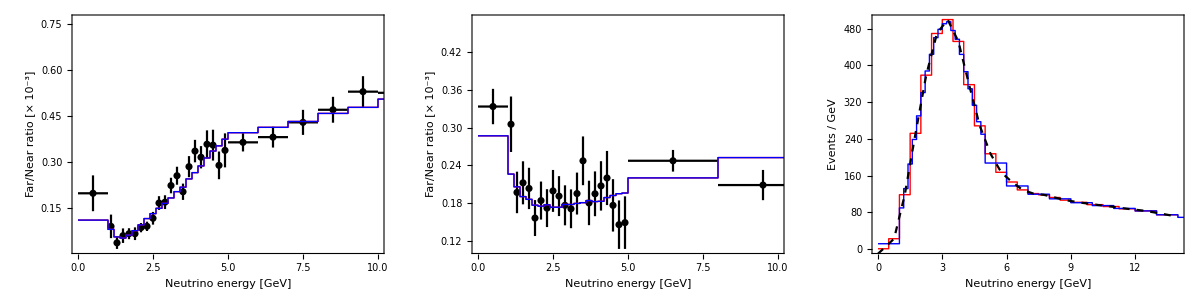

```mathematica
Grid[{{MINOSPlot[1],MINOSPlot[2],MINOSPlot[5]}}]
```

```mathematica
Eff[5]
Eff[5]/Eff[1]
Eff[2]
```

{0.620679,1.15642,1.11325,1.20266,1.24991,1.26649,1.28435,1.23884,1.185,1.14273,1.07701,1.03224,0.98756,0.935021,0.914068,0.895013,0.895117,0.911134,0.947422,0.985779,1.04979,1.20584,1.42919,1.49485,1.55423,1.63722,1.65154,1.68328,1.69948,1.65695,1.65695,1.65695,1.65695,1.65695,1.65695,1.65695,1.65695,1.65695,1.65695,1.65695,1.65695,1.65695,1.65695}

{2.02668,2.49371,2.41132,2.09727,1.91997,1.94344,1.89242,1.82451,1.71594,1.61166,1.50803,1.41627,1.30099,1.2183,1.14912,1.15682,1.19095,1.21155,1.26803,1.35216,1.41786,1.58147,1.61947,1.56266,1.71743,1.66233,1.37833,1.62419,1.57598,1.93288,2.01536,1.78996,1.80239,1.28375,1.27806,1.82789,1.78469,3.23653,2.86409,4.56493,3.87751,3.35569,3.43595}

{1.44,1.19613,1.12838,1.07641,1.06989,1.01473,0.994284,0.987635,0.94107,0.9121,0.906042,0.872572,0.848265,0.818536,0.803087,0.765256,0.740823,0.740224,0.72942,0.719908,0.70712,0.735032,0.77287,0.783106,0.803621,0.813162,0.693064,0.537895,0.508897}

### Fit of 3-flavor parameters (sanity check, comparison to MINOS disappearance analysis)

```mathematica
MINOSContour90=Cases[Import["0-code/glb/minos-2016/data/minos2013-disapp.dat","Table"],{Repeated[_?NumericQ]}];
(*MINOSLikelihood=Cases[Import["0-code/glb/minos-2016/data/minos2013-disapp-likelihood.csv"],{Repeated[_Real|_Integer]}];*)

i=1;
Data[i]=Cases[Import["2-smparams/th23dm31-minos.dat"],{Repeated[_Real|_Integer]}];
Data[i]={Sin[2#⟦1⟧]^2,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Data[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,-1⟧]
```

75.8573

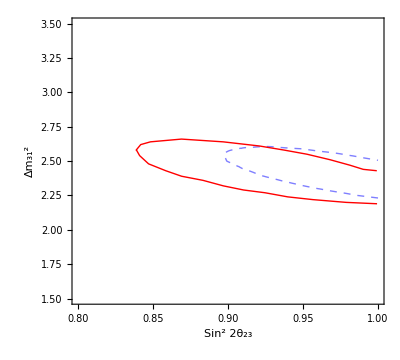

```mathematica
ContourPlot[DataInterpol[i][s22th13,dm31*1*^-3]-Chi2Min[i],{s22th13,0.8,1},{dm31,1.5,3.5},Contours->{(*χ2[2,0.32],*)χ2[2,0.1]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]},
Epilog->{Directive[Thick,Red],Line[{#⟦1⟧,#⟦2⟧*10^3}&/@MINOSContour90]},FrameLabel->{"Sin^2 2θ_23","Δm_31^2"}]
```

### θ_24 vs. Δm_41^2

```mathematica
Clear[DataMINOS,Data,DataInterpol,Chi2Min];
DataFilesMINOS={"0-code/glb/minos-2016/data/th24dm41-contours.dat"};
For[i=1,i≤Length[DataFilesMINOS],i++,
DataMINOS[i]=Cases[Import[DataFilesMINOS⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
];

DataFiles="3-3p1/"<>#&/@{"th24dm41-minos-2016.dat"};
(*DataFiles="results/"<>#&/@{"th24dm41-minos-2016.dat.gz"};*)
For[i=1,i≤Length[DataFiles],i++,
Data[i]={Sin[#⟦1⟧]^2,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]=Select[Data[i],#⟦2⟧<2&];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,3⟧];
];
Chi2Min[1]
```

56.1299

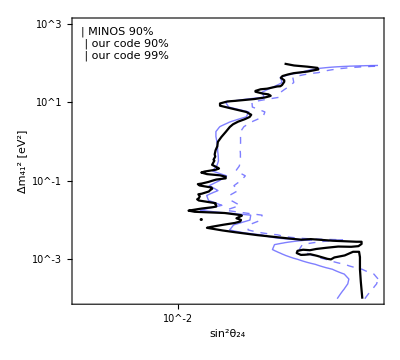

```mathematica
i=1;
MyLegend=Framed[Grid[{
{LegendLine[Directive[Thick,Black]],"MINOS 90%"},
{LegendLine[Directive[Thick,Blue]],"our code 90%"},
{LegendLine[Directive[Thick,Blue,Dashed]],"our code 99%"}
},Alignment->{Left,Center}]];
Grid[{{
(*ContourPlot[DataInterpol[i][s2th24,logdm41]-Chi2Min[i],{s2th24,0,0.12},{logdm41,-4,3},Contours->{χ2[2,0.1],χ2[2,0.01]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Blue]},
FrameLabel->{"sin^2θ_24","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{Automatic,Automatic}},
Epilog->{Text["•",Select[Data[i],#⟦3⟧==Chi2Min[i]&]⟦1,1;;2⟧]}],*)
Show[
ContourPlot[DataInterpol[i][10^logs2th24,logdm41]-Chi2Min[i],{logs2th24,-3,0},{logdm41,-4,3},Contours->{χ2[2,0.1],χ2[2,0.01]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]}],
ListPlot[{Log10[#⟦1⟧],Log10[#⟦2⟧]}&/@DataMINOS[1],Joined->True,PlotStyle->Black],
FrameLabel->{" sin^2θ_24","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},Epilog->{
Text["•",({Log10[#⟦1⟧],#⟦2⟧}&/@Select[Data[i],#⟦3⟧==Chi2Min[i]&])⟦1,1;;2⟧],
Inset[MyLegend,Scaled[{0.03,0.97}],{-1,1}]
}
]
}}]
```

## MINOS — 1710.06488

### Event spectra

```mathematica
DataFiles={{"minos-2017-dm41-0.1",{1,1}},{"minos-2017-dm41-0.1",{1,2}},{"minos-2017-dm41-0.1",{1,3}},{"minos-2017-dm41-0.1",{1,4}}}/.s_String:>"1-spectra/"<>s<>".dat";
DataFiles={{"minos-2017-dm41-1000",{1,1}},{"minos-2017-dm41-1000",{1,2}},{"minos-2017-dm41-1000",{1,3}},{"minos-2017-dm41-1000",{1,4}}}/.s_String:>"1-spectra/"<>s<>".dat";
DataFiles={{"minos-2017-th24-0",{1,1}},{"minos-2017-th24-0",{1,2}},{"minos-2017-th24-0",{1,3}},{"minos-2017-th24-0",{1,4}}}/.s_String:>"1-spectra/"<>s<>".dat";
(*DataFiles={{"minos-2017-noosc",{1,1}},{"minos-2017-noosc",{1,2}},{"minos-2017-noosc",{1,3}},{"minos-2017-noosc",{1,4}}}/.s_String:>"1-spectra/"<>s<>".dat";*)
DataFiles={{"minos-2017-nusquids-test",{1,1}},{"minos-2017-nusquids-test",{1,2}},{"minos-2017-nusquids-test",{1,3}},{"minos-2017-nusquids-test",{1,4}}}/.s_String:>"1-spectra/"<>s<>".dat";
(*DataFiles={{"minos-2017-nusquids-test-1",{1,1}},{"minos-2017-nusquids-test-1",{1,2}},{"minos-2017-nusquids-test-1",{1,3}},{"minos-2017-nusquids-test-1",{1,4}}}/.s_String:>"1-spectra/"<>s<>".dat";
DataFiles={{"minos-2017-nusquids-test-3",{1,1}},{"minos-2017-nusquids-test-3",{1,2}},{"minos-2017-nusquids-test-3",{1,3}},{"minos-2017-nusquids-test-3",{1,4}}}/.s_String:>"1-spectra/"<>s<>".dat";
DataFiles={{"minos-2017-nusquids-test-4",{1,1}},{"minos-2017-nusquids-test-4",{1,2}},{"minos-2017-nusquids-test-4",{1,3}},{"minos-2017-nusquids-test-4",{1,4}}}/.s_String:>"1-spectra/"<>s<>".dat";*)
DataFilesMINOS={"data-fd-nc","data-nd-nc","data-fd-cc","data-nd-cc"}/.s_String:>"0-code/glb/minos-plus/data/"<>s<>".dat";
MyLabels={"FD NC","ND NC","FD CC","ND CC"};

For[i=1,i≤Length[DataFiles],i++,
If[Head[DataFiles⟦i⟧]===List,
Data[i]=ToExpression[StringReplace[Import[DataFiles⟦i,1⟧,"Text"],RegularExpression["#.*\n"]->""]]⟦Sequence@@DataFiles⟦i,2⟧⟧,
(* Else *)
Data[i]=Get[DataFiles⟦i⟧];
];
];
For[i=1,i≤Length[DataFilesMINOS],i++,
DataMINOS[i]=Cases[Import[DataFilesMINOS⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
];

GetBinWidths[s_]:=Module[{t,j},(* This works only if the lower boundary of the 1st bin is at 0 *)
t={2*s⟦1⟧};
For[j=1,j≤Length[s]-1,j++,
AppendTo[t,2*Differences[s]⟦j⟧-t⟦j⟧];
];
Return[t];
];
```

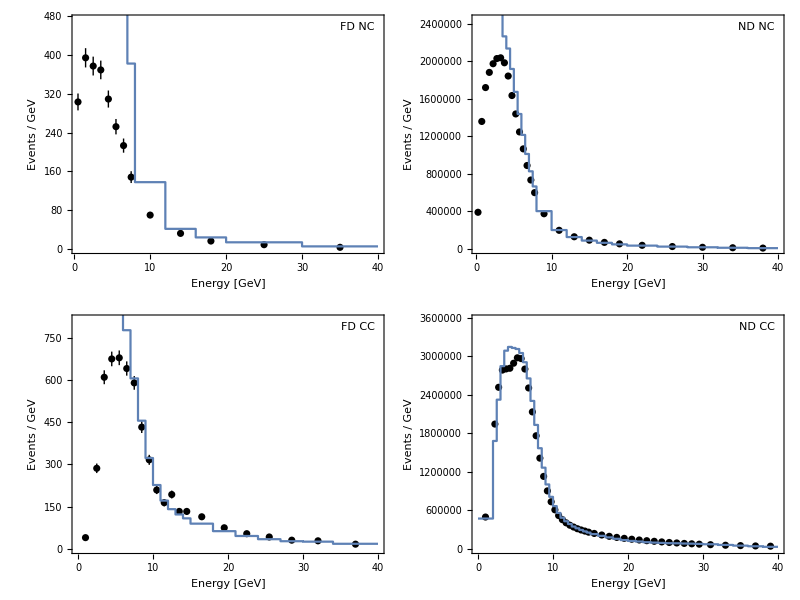

```mathematica
For[i=1,i≤Length[DataFiles],i++,
BinWidths[i]=GetBinWidths[Data[i]⟦All,1⟧];
PlotList[i]=Flatten[MapThread[{{#1⟦1⟧-#2/2,#1⟦2⟧/#2},{#1⟦1⟧+#2/2,#1⟦2⟧/#2}}&,{Data[i],BinWidths[i]}],{1,2}];
PlotListObs[i]=Table[{{DataMINOS[i]⟦k,1⟧,DataMINOS[i]⟦k,2⟧/BinWidths[i]⟦k⟧},ErrorBar[Sqrt[DataMINOS[i]⟦k,2⟧]/BinWidths[i]⟦k⟧]},{k,1,Length[BinWidths[i]]}];
(*PlotList[i]=Flatten[MapThread[{{#1⟦1⟧-#2/2,#1⟦2⟧},{#1⟦1⟧+#2/2,#1⟦2⟧}}&,{Data[i],BinWidths[i]}],{1,2}];
PlotListObs[i]=Table[{{DataMINOS[i]⟦k,1⟧,DataMINOS[i]⟦k,2⟧},ErrorBar[Sqrt[DataMINOS[i]⟦k,2⟧]]},{k,1,Length[BinWidths[i]]}];*)
MyPlot[i]=Show[
ErrorListPlot[PlotListObs[i],PlotRange->All,PlotStyle->Directive[Thick,Black]],
ListPlot[PlotList[i],Joined->True,InterpolationOrder->0],
PlotRange->{0,1.2Max[PlotListObs[i]⟦All,1⟧]},
FrameLabel->{"Energy [GeV]","Events / GeV"},ImageSize->400,ImagePadding->{{100,10},{60,10}},
Epilog->{Text[MyLabels⟦i⟧,Scaled[{0.97,0.97}],{1,1}]}
];
];
Grid[{{MyPlot[1],MyPlot[2]},{MyPlot[3],MyPlot[4]}}]
```

### θ_24 vs. Δm_41^2

```mathematica
(* Published MINOS/MINOS+ curves *)
Clear[DataMINOS,Data,DataInterpol,Chi2Min];
DataFilesMINOS={"0-code/glb/minos-plus/data/th24dm41-contours-1710.06488.dat"};
For[i=1,i≤Length[DataFilesMINOS],i++,
DataMINOS[i]=Cases[Import[DataFilesMINOS⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
];

(* our simulations *)
DataFiles="3-3p1/"<>#&/@{"th24dm41-minos-2017.dat","th24dm41-minos-2017-nosys.dat",
"th24dm41-minos-2017-nomarg.dat","th24dm41-minos-2017-nomarg-freenorm.dat",
"th24dm41-minos-2017-nomarg-glblowpass.dat"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]={Sin[#⟦1⟧]^2,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,3⟧];
];
Chi2Min[1]
```

62.0441

62.2288

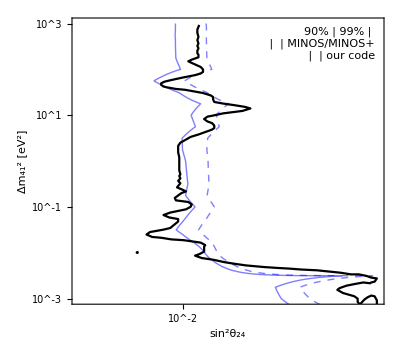

```mathematica
i=3;
Chi2Min[i]
MyLegend=Framed[Grid[{
{"90%","99%",""},
{LegendLine[Directive[Thick,Black]],"","MINOS/MINOS+"},
{LegendLine[Directive[Thick,Blue]],LegendLine[Directive[Thick,Blue,Dashed]],"our code"}(*,
{LegendLine[Directive[Thick,Red]],LegendLine[Directive[Thick,Red,Dashed]],"our code (no syst.)"}*)
},Alignment->{Left,Center},Spacings->{.3,.2},BaseStyle->{FontSize->14}],Background->GrayLevel[1,.7]];
Grid[{{
Show[
ContourPlot[DataInterpol[i][10^logs2th24,logdm41]-Chi2Min[i],{logs2th24,-3,0},{logdm41,-4,3},Contours->{χ2[2,0.1],χ2[2,0.01]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]}],
(*ContourPlot[DataInterpol[3][10^logs2th24,logdm41]-Chi2Min[2],{logs2th24,-3,0},{logdm41,-4,3},Contours->{χ2[2,0.1],χ2[2,0.01]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Red],Directive[Thick,Red,Dashed]}],*)
ListPlot[{Log10[#⟦1⟧],Log10[#⟦2⟧]}&/@DataMINOS[1],Joined->True,PlotStyle->Black],
PlotRange->{-3,3},
FrameLabel->{" sin^2θ_24","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},Epilog->{
Text["•",({Log10[#⟦1⟧+1*^-10],#⟦2⟧}&/@Select[Data[i],#⟦3⟧==Chi2Min[i]&])⟦1,1;;2⟧],
Blue,(*Text[Style["no systematics\nno profiling over θ_23, θ_34, Δm_31^2",TextAlignment->Left,LineSpacing->{1,0}],Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,.7]],*)
Black,Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}]
}
]
}}]
```

```mathematica
R=Union[NN,{dmsq->1000.,L->1.04km,n->30}];
(dmsq L)/(4*n π/2)//.R
%-(dmsq L)/(4*(n+1) π/2)//.R
```

2.80062×10^10

9.03425×10^8

### θ_23 vs. Δm_31^2 in standard 3-flavor oscillations

```mathematica
(* Published MINOS/MINOS+ curves *)
(*Clear[DataMINOS,Data,DataInterpol,Chi2Min];
DataFilesMINOS={"0-code/glb/minos-plus/data/th24dm41-contours-1710.06488.dat"};
For[i=1,i≤Length[DataFilesMINOS],i++,
DataMINOS[i]=Cases[Import[DataFilesMINOS⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
];*)

(* our simulations *)
DataFiles="results/"<>#&/@{"minos-test.dat"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]={Sin[#⟦1⟧]^2,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,3⟧];
];
Chi2Min[1]
```

61.9807

61.9807

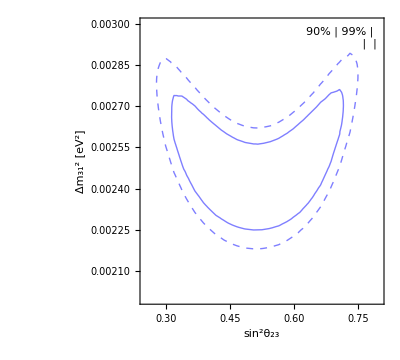

```mathematica
i=1;
Chi2Min[i]
MyLegend=Framed[Grid[{
{"90%","99%",""},
(*{LegendLine[Directive[Thick,Black]],"","MINOS/MINOS+"},*)
{LegendLine[Directive[Thick,Blue]],LegendLine[Directive[Thick,Blue,Dashed]](*,"our code"*)}(*,
{LegendLine[Directive[Thick,Red]],LegendLine[Directive[Thick,Red,Dashed]],"our code (no syst.)"}*)
},Alignment->{Left,Center},Spacings->{.3,.2},BaseStyle->{FontSize->14}],Background->GrayLevel[1,.7]];
Grid[{{
Show[
ContourPlot[DataInterpol[i][s2th23,dm31]-Chi2Min[i],{s2th23,0.25,0.8},{dm31,0.002,0.003},Contours->{χ2[2,0.1],χ2[2,0.01]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]}],
(*ListPlot[{Log10[#⟦1⟧],Log10[#⟦2⟧]}&/@DataMINOS[1],Joined->True,PlotStyle->Black],*)
FrameLabel->{" sin^2θ_23","Δm_31^2 [eV^2]"},FrameTicks->Automatic,Epilog->{
Text["•",({Log10[#⟦1⟧+1*^-10],#⟦2⟧}&/@Select[Data[i],#⟦3⟧==Chi2Min[i]&])⟦1,1;;2⟧],
Blue,(*Text[Style["no systematics\nno profiling over θ_23, θ_34, Δm_31^2",TextAlignment->Left,LineSpacing->{1,0}],Scaled[{0.03,0.03}],{-1,-1},Background->GrayLevel[1,.7]],*)
Black,Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}]
}
]
}}]
```

```mathematica
PDataFiles={"results/prob-3f.dat","results/prob-4f.dat"};
For[i=1,i≤Length[PDataFiles],i++,
PData[i]=Cases[Import[PDataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
];
```

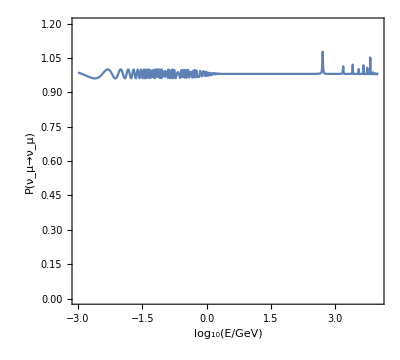

```mathematica
PlotList=MapThread[{Log10[#1⟦1⟧],#2⟦3⟧/#1⟦3⟧}&,{PData[1],PData[2]}];
ListPlot[PlotList,Joined->True,FrameLabel->{"log_10(E/GeV)","P(ν_μ→ν_μ)"},PlotRange->{0,1.2}]
```

## Atmospheric neutrinos (courtesy of Michele Maltoni)

### Constraints on d_μ

```mathematica
Data[1]=Cases[Import["0-code/old-codes/external-old/Data-files/atm-data-dmu.dat","Table"],{Repeated[_?NumericQ]}];
Data[2]={#⟦1⟧^2,#⟦2⟧^2,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import["6-atm/Um4Um5-v43.dat.gz","Table"],{Repeated[_?NumericQ]}];
Data[3]={#⟦1⟧^2,Min[#⟦2⟧,#⟦3⟧]}&/@Cases[Import["6-atm/Um4-v43.dat.gz","Table"],{Repeated[_?NumericQ]}];
Data[4]={#⟦1⟧^2,#⟦2⟧^2,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import["6-atm/Um4Um5-th13-0.dat.gz","Table"],{Repeated[_?NumericQ]}];
Data[5]={#⟦1⟧^2,Min[#⟦2⟧,#⟦3⟧]}&/@Cases[Import["6-atm/Um4-th13-0.dat.gz","Table"],{Repeated[_?NumericQ]}];
Data[6]={#⟦1⟧^2,#⟦2⟧^2,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import["6-atm/Um4Um5.dat.gz","Table"],{Repeated[_?NumericQ]}];
Data[7]={#⟦1⟧^2,Min[#⟦2⟧,#⟦3⟧]}&/@Cases[Import["6-atm/Um4.dat.gz","Table"],{Repeated[_?NumericQ]}];

(* Use x=Um4^2+Um5^2, y=Um4^2-Um5^2 *)
DataInterpolFull[2]=Interpolation[Data[2],InterpolationOrder->1];
DataInterpol[2]=(FindMinimum[DataInterpolFull[j][(#+y)/2,(#-y)/2],{y,#,-#,#}]⟦1⟧&)/.{j->2};
DataInterpolFull[4]=Interpolation[Data[4],InterpolationOrder->1];
DataInterpol[4]=(FindMinimum[DataInterpolFull[j][(#+y)/2,(#-y)/2],{y,#,-#,#}]⟦1⟧&)/.{j->4};
DataInterpolFull[6]=Interpolation[Data[6],InterpolationOrder->1];
DataInterpol[6]=(FindMinimum[DataInterpolFull[j][(#+y)/2,(#-y)/2],{y,#,-#,#}]⟦1⟧&)/.{j->6};

MyLegend=Framed[Grid[{
(*{LegendLine[Black],"Thomas' table"},*)
{LegendLine[Directive[Blue,Thick,Dotted]],"atm v43 (4 flavor)"},
{LegendLine[Directive[Blue]],"atm v54 (4 flavor)"},
{LegendLine[Directive[Blue,Dashed]],"atm v54 (4 flavor, θ_13=0)"},
{LegendLine[Directive[Red, Thick, Dotted]],"atm v43 (5 flavor)"},
{LegendLine[Directive[Red]],"atm v54 (5 flavor)"},
{LegendLine[Directive[Red, Dashed]],"atm v54 (5 flavor, θ_13=0)"}
}, BaseStyle->{FontFamily->"Times",FontSize->16},Alignment->Left],Background->GrayLevel[1,0.8]];
Show[(*ListPlot[Data[1],Joined->True,PlotStyle->Black],*)
ListPlot[Transpose[{Data[3]⟦All,1⟧,Data[3]⟦All,2⟧-Data[3]⟦1,2⟧}],Joined->True,PlotStyle->Directive[Blue,Thick,Dotted]],
ListPlot[Transpose[{Data[5]⟦All,1⟧,Data[5]⟦All,2⟧-Data[5]⟦1,2⟧}],Joined->True,PlotStyle->Directive[Blue]],
ListPlot[Transpose[{Data[7]⟦All,1⟧,Data[7]⟦All,2⟧-Data[7]⟦1,2⟧}],Joined->True,PlotStyle->Directive[Blue,Dashed]],
Plot[DataInterpol[2][dmu]-DataInterpol[2][0],{dmu,0,0.25},PlotStyle->Directive[Red,Thick,Dotted]],
Plot[DataInterpol[4][dmu]-DataInterpol[4][0],{dmu,0,0.25},PlotStyle->Directive[Red]],
Plot[DataInterpol[6][dmu]-DataInterpol[6][0],{dmu,0,0.25},PlotStyle->Directive[Red,Dashed]],
PlotRange->{{0,0.25},{0,85}},
FrameLabel->{"U_μ4^2 + U_μ5^2","Δχ^2"},Epilog->{Inset[MyLegend,Scaled[{0.03,0.97}],{-1,1}]}]
```

FindMinimum::reged: The point {5.10714×10^-6} is at the edge of the search region {-5.10714×10^-6, 5.10714×10^-6} in coordinate 1 and the computed search direction points outside the region.

FindMinimum::reged: The point {0.} is at the edge of the search region {0., 0.} in coordinate 1 and the computed search direction points outside the region.

FindMinimum::reged: The point {5.10714×10^-6} is at the edge of the search region {-5.10714×10^-6, 5.10714×10^-6} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindMinimum :: reged will be suppressed during this calculation.

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

-Graphics-

### Constraints on SM parameters

#### θ_23 vs. θ_13 vs. Δm_31^2

```mathematica
DataFiles="6-atm/"<>#&/@{"dm31th23th13.dat.gz"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]={Sin[#⟦2⟧]^2,#⟦1⟧,Log10[Sin[10^#⟦3⟧]^2],Min[#⟦{-2,-1}⟧]}&/@Data[i];
Data[i,1]={#⟦1,1⟧,#⟦1,2⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{1,2}⟧==#2⟦{1,2}⟧&]; (* dm31, th23 *)
Data[i,2]={#⟦1,1⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{1,3}⟧==#2⟦{1,3}⟧&]; (* dm31, th13 *)
Data[i,3]={#⟦1,2⟧,#⟦1,3⟧,Min[#⟦All,-1⟧]}&/@Gather[Data[i],#1⟦{2,3}⟧==#2⟦{2,3}⟧&]; (* th23, th13 *)

DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
DataInterpol[i,1]=Interpolation[Data[i,1],InterpolationOrder->1];
DataInterpol[i,2]=Interpolation[Data[i,2],InterpolationOrder->1];
DataInterpol[i,3]=Interpolation[Data[i,3],InterpolationOrder->1];

p1Min[i]=Min[Data[i]⟦All,1⟧];
p1Max[i]=Max[Data[i]⟦All,1⟧];
p2Min[i]=Min[Data[i]⟦All,2⟧];
p2Max[i]=Max[Data[i]⟦All,2⟧];
p3Min[i]=Min[Data[i]⟦All,3⟧];
p3Max[i]=Max[Data[i]⟦All,3⟧];

BFPoint[i]=Sort[Data[i],OrderedQ[{#1⟦-1⟧,#2⟦-1⟧}]&]⟦1⟧;
{Chi2Min[i],BFPoint[i]}=FindMinimum[DataInterpol[i][p1,p2,p3],{p1,BFPoint[i]⟦1⟧,p1Min[i],p1Max[i]},{p2,BFPoint[i]⟦2⟧,p2Min[i],p2Max[i]},{p3,BFPoint[i]⟦3⟧,p3Min[i],p3Max[i]}]/.Rule[s_,x_]:>x;
];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

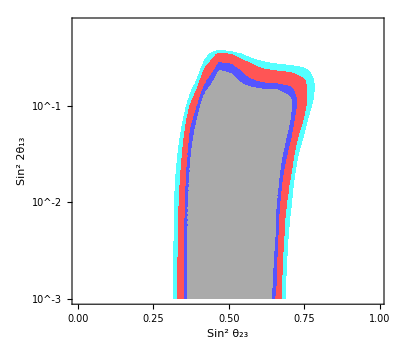
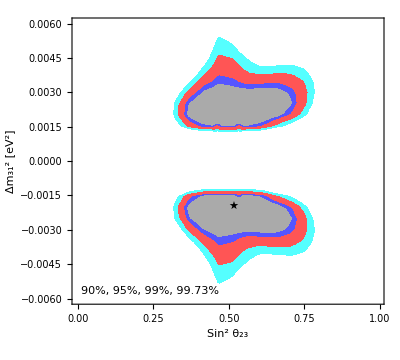
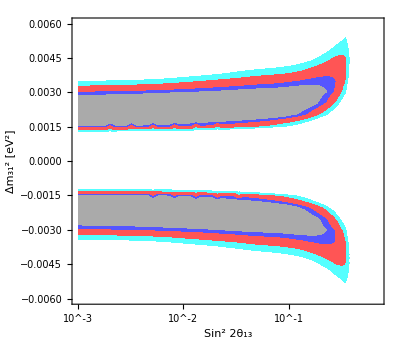
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
MyOptions={PlotRange->Full,Contours->{χ2[2,0.1],χ2[2,0.05],χ2[2,0.01],χ2[2,PValue[3]]},ContourShading->(Lighter[#]&/@{Gray,Blue,Red,Cyan,White}),ContourStyle->None,ImagePadding->{{100,10},{70,10}}};
For[i=1,i≤Length[DataFiles],i++,
MyPlot[i,1]=ContourPlot[DataInterpol[i,1][p1,p2]-Chi2Min[i],{p1,p1Min[i],p1Max[i]},{p2,p2Min[i],p2Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"Sin^2 θ_23","Δm_31^2 [eV^2]"},
Epilog->{
Text["★",BFPoint[i]⟦{1,2}⟧],
Text["90%, 95%, 99%, 99.73%",Scaled[{0.03,0.03}],{-1,-1}]}];
MyPlot[i,2]=ContourPlot[DataInterpol[i,2][p1,p3]-Chi2Min[i],{p1,p1Min[i],p1Max[i]},{p3,p3Min[i],p3Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"Sin^2 θ_23","Sin^2 2θ_13"},FrameTicks->{Automatic,LogTicks[-4,0],Automatic,LogTicksNoLabel[-4,0]}];
MyPlot[i,3]=ContourPlot[DataInterpol[i,3][p2,p3]-Chi2Min[i],{p3,p3Min[i],p3Max[i]},{p2,p2Min[i],p2Max[i]},Evaluate[Sequence@@MyOptions],FrameLabel->{"Sin^2 2θ_13","Δm_31^2 [eV^2]"},FrameTicks->{LogTicks[-4,0],Automatic,LogTicksNoLabel[-4,0],Automatic}];
];
MyGridPlot=Grid[{{MyPlot[1,2]},{MyPlot[1,1],MyPlot[1,3]}}]
If[SaveFigures,
Export["fig/atm-3flavor.pdf",MyGridPlot];
];
```

## RENO

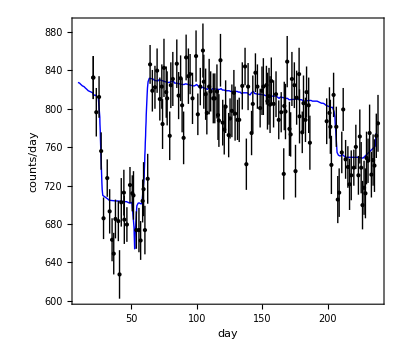

InterpolatingFunction::dmval: Input value {237.299} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {238.59} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.1863

InterpolatingFunction::dmval: Input value {237.299} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {238.59} lies outside the range of data in the interpolating function. Extrapolation will be used.

{156.594,{a→-0.0133051}}

0.190176

```mathematica
i=1;
DataObs=Cases[Import["0-code/glb/reno/nd-data.dat"],{Repeated[_?NumericQ]}];
Data[i]=Cases[Import["0-code/glb/reno/nd-prediction.dat"],{Repeated[_?NumericQ]}];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Show[ListPlot[Data[i],Joined->True,PlotStyle->Blue],
ErrorListPlot[{{#⟦1⟧,#⟦2⟧},ErrorBar[#⟦3⟧]}&/@DataObs,PlotStyle->Black],
FrameLabel->{"day","counts/day"}]

NObsND=154088;
Chi2=Sum[(DataObs⟦j,2⟧-(1-0.012)DataInterpol[i][DataObs⟦j,1⟧])^2/DataObs⟦j,3⟧^2,{j,1,Length[DataObs]}]; (* 1.2% reduction due to theta-13 *)
1-CDF[ChiSquareDistribution[Length[DataObs]]][Chi2]

(* Fit with free normalization *)
Chi2=Sum[(DataObs⟦j,2⟧-(1+a)DataInterpol[i][DataObs⟦j,1⟧])^2/DataObs⟦j,3⟧^2,{j,1,Length[DataObs]}];
FindMinimum[Chi2,{a,0}]
1-CDF[ChiSquareDistribution[Length[DataObs]]][%⟦1⟧]
```

```mathematica
(* Alternative approach: Compute number of events in each bin from error bar, assuming it is statistical only *)
(* SEEMS *NOT* TO WORK *)
NBGND=21.75; (* events/day *)

Solve[Sqrt[(RatePaper+BGperDay)*τ]==ErrorPaper*τ,τ]
NObsND=Total[(NBGND+#⟦2⟧)*(NBGND+#⟦2⟧)/(#⟦3⟧)^2&/@DataObs]
NThND=Total[(NBGND+DataInterpol[i][#⟦1⟧])*(NBGND+#⟦2⟧)/(#⟦3⟧)^2&/@DataObs]
Chi2=(NObsND-NThND)^2/NThND
1-CDF[ChiSquareDistribution[1]][Chi2]
```

{{τ→0},{τ→(BGperDay+RatePaper)/ErrorPaper^2}}

156368.

InterpolatingFunction::dmval: Input value {237.299} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {238.59} lies outside the range of data in the interpolating function. Extrapolation will be used.

158261.

22.6481

1.94556×10^-6

```mathematica
Total[(NBGND+#⟦2⟧)/(#⟦3⟧)^2&/@DataObs]
```

195.4

## MINERνA

```mathematica
i=1;
DataFiles="9-ttt/"<>#<>".dat"&/@{"minerva-spectrum"};
Data[i]=ToExpression[StringReplace[Import[DataFiles⟦i⟧,"Text"],RegularExpression["#.*\n"]->""]];
Sig[i]=glbSignalTot[Data[1]⟦1,1⟧]
BG[i]=glbBGTot[Data[1]⟦1,1⟧]
BinWidth=Mean[Differences[Sig[i]⟦All,1⟧]];
```

{{0.5,0.506783},{1.5,12.905},{2.5,13.5132},{3.5,10.5063},{4.5,4.12897},{5.5,1.19437},{6.5,0.51899},{7.5,0.322799},{8.5,0.212653},{9.5,0.145039},{10.5,0.108304},{11.5,0.084237},{12.5,0.065951},{13.5,0.051958},{14.5,0.042563},{15.5,0.033898},{16.5,0.027777},{17.5,0.022461},{18.5,0.018939},{19.5,0.015633}}

{{0.5,0.},{1.5,0.},{2.5,0.},{3.5,0.},{4.5,0.},{5.5,0.},{6.5,0.},{7.5,0.},{8.5,0.},{9.5,0.},{10.5,0.},{11.5,0.},{12.5,0.},{13.5,0.},{14.5,0.},{15.5,0.},{16.5,0.},{17.5,0.},{18.5,0.},{19.5,0.}}

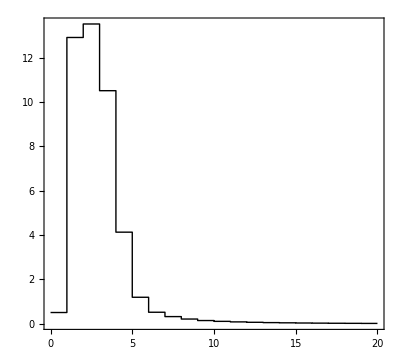

```mathematica
PlotList={#⟦1⟧-BinWidth/2,#⟦2⟧}&/@Sig[i];
AppendTo[PlotList,{PlotList⟦-1,1⟧+BinWidth,PlotList⟦-1,2⟧}];
ListPlot[PlotList,Joined->True,InterpolationOrder->0,PlotStyle->Directive[Thick,Black]]
```

## OPERA

### Flux / Cross Sections

The following is unnecessary / wrong -- glb_ICARUS.dat is already just the flux!

```mathematica
(* Divide out cross sections from the flux*x-sec product in Pedro's code *)
FluxData=Cases[Import["0-code/glb/opera/glb_ICARUS_spectrum.dat"],{Repeated[_?NumericQ]}];
XSecData=Cases[Import["0-code/glb/opera/XCC.dat"],{Repeated[_?NumericQ]}];
XSecDataInterpol[En_]=En*Interpolation[XSecData⟦All,{1,3}⟧][Log10[En]];
```

```mathematica
FluxDataNew=ReplacePart[#,3->#⟦3⟧/XSecDataInterpol[#⟦1⟧]]&/@FluxData;
```

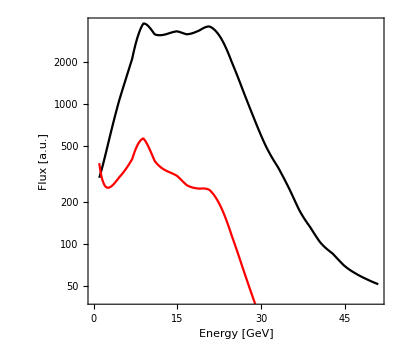

```mathematica
Show[ListLogPlot[FluxData⟦All,{1,3}⟧,Joined->True,PlotStyle->Black],
ListLogPlot[FluxDataNew⟦All,{1,3}⟧,Joined->True,PlotStyle->Red],
FrameLabel->{"Energy [GeV]","Flux [a.u.]"}
]
```

```mathematica
Export["~/opera-flux.dat",FluxDataNew,"Table"];
```

### Event Spectrum

```mathematica
(* define OPERA data (hardcoded here, taken from opera-2013.c, which in turn is based on Neutrino 2016 talk) *)
i=1;
DataOPERA[i]=Transpose[{BinCenters0,{1,6,6}}];
BGOPERA[i]=Transpose[{BinCenters0,{0.58022,3.40993,5.15097}}];
OPERANorm=2.7*^3*17.97/5.25;
PlotListObs[i]=MapThread[{{#1⟦1⟧/GeV,#1⟦2⟧/#2/GeV^-1},ErrorBar[#2/2/GeV,N[Sqrt[#⟦2⟧]]/#2/GeV^-1]}//.NN&,{DataOPERA[i],BinWidths[i]}];
MyPlotObs[i]=ErrorListPlot[PlotListObs[i],PlotRange->All,PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}];

(* Read GLoBES output files *)
DataFiles={{"opera-oscdecay",{1,1}}}/.s_String:>"1-spectra/"<>s<>".dat";
BinBoundaries0={1,10,20,30}GeV//.NN;
BinWidths0=Differences[BinBoundaries0];
BinCenters0=ListConvolve[{0.5,0.5},BinBoundaries0];
For[i=1,i≤Length[DataFiles],i++,
DataRaw[i]=Import[DataFiles⟦i,1⟧,"Text"];
Data[i]=ToExpression[StringReplace[DataRaw[i],RegularExpression["#.*\n"]->""]]⟦Sequence@@DataFiles⟦i,2⟧⟧;
BinBoundaries[i]=BinBoundaries0;
BinWidths[i]=BinWidths0;
BinCenters[i]=BinCenters0;

(* extract event rates from GLobES output file *)
EventsSignal[i]={#⟦1⟧GeV,OPERANorm*#⟦2⟧}//.NN&/@glbSignalTot[Data[i]]⟦1;;Length[BinBoundaries[i]]-1⟧;
EventsBG[i]=MapThread[{#1⟦1⟧GeV,#1⟦2⟧+#2⟦2⟧}//.NN&,{glbBGTot[Data[i]]⟦1;;Length[BinBoundaries[i]]-1⟧,BGOPERA[i]}];
EventsTotal[i]=MapThread[{#⟦1⟧GeV,OPERANorm*#1⟦2⟧+#2⟦2⟧}//.NN&,{glbSignalBGTot[Data[i]]⟦1;;Length[BinBoundaries[i]]-1⟧,BGOPERA[i]}];

(* extract metadata *)
TH14[i]=ImportString[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *TH14 = ([-+0-9eE\\.]*).*"]:>"$1"],"List"]⟦1⟧;
TH24[i]=ImportString[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *TH24 = ([-+0-9eE\\.]*).*"]:>"$1"],"List"]⟦1⟧;
DM41[i]=ImportString[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *DM41 = ([-+0-9eE\\.]*).*"]:>"$1"],"List"]⟦1⟧;
M4Γ[i]=ImportString[StringReplace[DataRaw[i],RegularExpression["(?m)(?s).*# *M4_GAMMA = ([-+0-9eE\\.]*).*"]:>"$1"],"List"]⟦1⟧;
Ue4[i]=Sin[TH14[i]];
Uμ4[i]=Cos[TH14[i]]Sin[TH24[i]];

(* make signal plot *)
PlotListSignal[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/GeV^-1}//.NN&,{BinBoundaries[i],Append[EventsSignal[i],EventsSignal[i]⟦-1⟧],Append[BinWidths[i],BinWidths[i]⟦-1⟧]}];
MyPlotSignal[i]=ListPlot[PlotListSignal[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[Thick,Blue,Dashed]];

(* make background plot *)
PlotListBG[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/GeV^-1}//.NN&,{BinBoundaries[i],Append[EventsBG[i],EventsBG[i]⟦-1⟧],Append[BinWidths[i],BinWidths[i]⟦-1⟧]}];
MyPlotBG[i]=ListPlot[PlotListBG[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[Thick,Blue,Dashed]];

(* make plot of total rate (sig+bg) *)
PlotListTotal[i]=MapThread[{#1/GeV,#2⟦2⟧/#3/GeV^-1}//.NN&,{BinBoundaries[i],Append[EventsTotal[i],EventsTotal[i]⟦-1⟧],Append[BinWidths[i],BinWidths[i]⟦-1⟧]}];
MyPlotTotal[i]=ListPlot[PlotListTotal[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[Thick,Blue]];
];
```

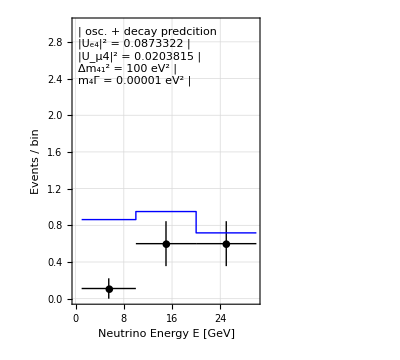

```mathematica
i=1;
MyLegend=Framed[Grid[{
(*{LegendDataPoint[PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}],"OPERA data"},*)
{LegendLine[Directive[Thick,Blue]],"osc. + decay predcition"},
{"|U_e4|^2 = "<>ToString[Ue4[i]^2],SpanFromLeft},
{"|U_μ4|^2 = "<>ToString[Uμ4[i]^2],SpanFromLeft},
{"Δm_41^2 = "<>ToString[DM41[i]]<>" eV^2",SpanFromLeft},
{"m_4Γ = "<>ToString[M4Γ[i]]<>" eV^2",SpanFromLeft}
},Spacings->{Automatic,Automatic}, Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];
Show[MyPlotObs[i],MyPlotTotal[i],
PlotRange->{{0,30},{0,5Max[Flatten[PlotListObs[i]⟦All,1,2⟧]]}},GridLines->Automatic,
FrameLabel->{"Neutrino Energy E [GeV]","Events / bin"},
Epilog->{Inset[MyLegend,Scaled[{0.03,0.97}],{-1,1}]}]
```

## ICARUS

### ICARUS Fit

```mathematica
DataFiles="9-devel/"<>#<>"-test.dat"&/@{"icarus-2012","icarus-2014"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}]⟦All,1;;3⟧;
Data[i]={Log10[Sin[2*10^(#⟦1⟧)]^2],#⟦2⟧,#⟦3⟧}&/@Data[i];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->2];
logs22thMin[i]=Min[Data[i]⟦All,1⟧];
logs22thMax[i]=Max[Data[i]⟦All,1⟧];
logdmMin[i]=Min[Data[i]⟦All,2⟧];
logdmMax[i]=Max[Data[i]⟦All,2⟧];
Chi2Min[i]=Min[Data[i]⟦All,3⟧];
Print[DataFiles⟦i⟧,": minimum at ",Select[Data[i],#⟦3⟧==Chi2Min[i]&]];
];

(* ICARUS contour from Neutrino 2014 *)
DataIcarus90=Sort[Reverse/@Cases[KPImport["0-code/glb/icarus-2014/nu2014/icarus-nu2014-90.dat"],{Repeated[_?NumericQ]}]];
DataIcarus99=Sort[Reverse/@Cases[KPImport["0-code/glb/icarus-2014/nu2014/icarus-nu2014-99.dat"],{Repeated[_?NumericQ]}]];
DataIcarusInterpol90=Interpolation[DataIcarus90,InterpolationOrder->1];
DataIcarusInterpol99=Interpolation[DataIcarus99,InterpolationOrder->1];
```

9-devel/icarus-2012-test.dat: minimum at {{-7.41794,-1.2,0.211898}}

9-devel/icarus-2014-test.dat: minimum at {{-7.41794,-2,0.489186}}

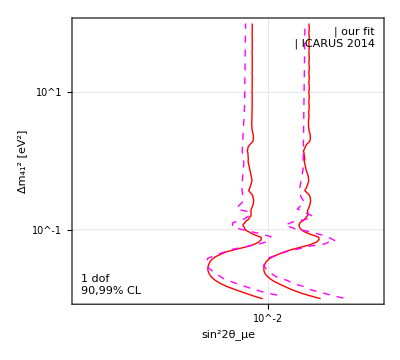

```mathematica
i=2;
MyContours={χ2[2,0.1],χ2[2,0.01]};
MyContours={χ2[1,0.1],χ2[1,0.01]}; (*FIXME*)
(*MyContours={-Log[0.1],-Log[0.01]};*)

MyLegend=Framed[Grid[{
{LegendLine[Directive[Red]],"our fit"},
{LegendLine[Directive[RGBColor[1,0,1],Thick,Dashed]],"ICARUS 2014"}
},Spacings->{Automatic,Automatic}, Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];

(*Chi2Icarus[dm41_,s22thme_]:=(χ2[1,.01]/DataIcarusInterpol99[dm41]^2)*s22thme^2;
MyPlotIcarus=ContourPlot[Chi2Icarus[10^logdm41,10^logs22thme],{logs22thme,-3,-0.5},{logdm41,-2,2},Contours->MyContours,ContourShading->False,ContourStyle->Directive[Pink,Thick,Dashed]];*)
Show[(*MyPlotIcarus,*)
ContourPlot[DataInterpol[i][logs22th,logdm]-Chi2Min[i],{logs22th,-3.,logs22thMax[i]},{logdm,logdmMin[i],logdmMax[i]},Contours->MyContours,PlotRange->Full,ContourShading->None,ContourStyle->Red],
FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},
FrameLabel->{"sin^22θ_μe","Δm_41^2 [eV^2]"},GridLines->Automatic,
Epilog->{
RGBColor[1,0,1],Thick,Dashed,
Line[Log10[Reverse/@DataIcarus90]],
Line[Log10[Reverse/@DataIcarus99]],
Black,Dashing[{}],
Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}],
Text[Style["1 dof\n90,99% CL",TextAlignment->Left],Scaled[{0.03,0.03}],{-1,-1}](*,
Text[Style["Fake\nnormalization",TextAlignment->Left],Scaled[{0.03,0.97}],{-1,1}]*)
}
]
```

### Feldman-Cousins

```mathematica
DataFilesFC="9-devel/"<>#<>"-fc.dat"&/@{"icarus-2014"};
For[i=1,i≤Length[DataFilesFC],i++,
DataFCRaw[i]=Import[DataFilesFC⟦i⟧,"Table"];
DataFC[i]=Cases[DataFCRaw[i],{"FC_data",Repeated[_?NumericQ]}]⟦All,4;;5⟧;
BestFitFC[i]=Cases[DataFCRaw[i],{"FC_bf",_?NumericQ}]⟦1,2⟧;
logs22thMin[i]=Min[DataFC[i]⟦All,1⟧];
logs22thMax[i]=Max[DataFC[i]⟦All,1⟧];
dlogs22thMax[i]=Differences[Union[DataFC[1]⟦All,1⟧]]⟦1⟧;
];
```

```mathematica
i=1;
FCBinning[i]={logs22thMin[i]-dlogs22thMax[i]/2,logs22thMax[i]+dlogs22thMax[i]/2,dlogs22thMax[i]};
FCBinCenters[i]=Range[logs22thMin[i],logs22thMax[i],dlogs22thMax[i]];
FCDataBinned[i]=BinCounts[DataFC[i],FCBinning[i],FCBinning[i]];
FCDataInterpol[i]=Interpolation[MapThread[Append[#2,#1]&,
{Flatten[FCDataBinned[i]],Flatten[Outer[List,FCBinCenters[i],FCBinCenters[i]],{1,2}]}],InterpolationOrder->1];
FCLimit[i][logs22thmueObs_,CL_]:=FindRoot[NIntegrate[FCDataInterpol[i][x,logs22thmueObs],{x,logs22thMin[i],xMax}]/NIntegrate[FCDataInterpol[i][x,logs22thmueObs],{x,logs22thMin[i],logs22thMax[i]}]==CL,{xMax,logs22thmueObs}];
```

```mathematica
FCDataBinned[i]//MatrixForm
```

(500 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
183 | 0 | 0 | 0 | 197 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 83 | 0 | 0 | 27 | 0 | 8 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
161 | 0 | 0 | 0 | 211 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 97 | 0 | 0 | 23 | 0 | 7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
167 | 0 | 0 | 0 | 203 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 88 | 0 | 0 | 32 | 0 | 8 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
183 | 0 | 0 | 0 | 192 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 79 | 0 | 0 | 35 | 0 | 9 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
160 | 0 | 0 | 0 | 186 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 102 | 0 | 0 | 41 | 0 | 7 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
176 | 0 | 0 | 0 | 170 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 107 | 0 | 0 | 36 | 0 | 9 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
141 | 0 | 0 | 0 | 202 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 109 | 0 | 0 | 34 | 0 | 13 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
137 | 0 | 0 | 0 | 190 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 102 | 0 | 0 | 46 | 0 | 17 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
132 | 0 | 0 | 0 | 185 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 121 | 0 | 0 | 47 | 0 | 9 | 5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
124 | 0 | 0 | 0 | 163 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 109 | 0 | 0 | 66 | 0 | 24 | 11 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
90 | 0 | 0 | 0 | 165 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 136 | 0 | 0 | 76 | 0 | 23 | 8 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
86 | 0 | 0 | 0 | 151 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 141 | 0 | 0 | 72 | 0 | 32 | 13 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
68 | 0 | 0 | 0 | 131 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 139 | 0 | 0 | 87 | 0 | 48 | 20 | 5 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
49 | 0 | 0 | 0 | 124 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 131 | 0 | 0 | 99 | 0 | 53 | 29 | 7 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
39 | 0 | 0 | 0 | 91 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 115 | 0 | 0 | 121 | 0 | 76 | 33 | 14 | 10 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
26 | 0 | 0 | 0 | 76 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 102 | 0 | 0 | 115 | 0 | 83 | 39 | 37 | 17 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
17 | 0 | 0 | 0 | 67 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 85 | 0 | 0 | 89 | 0 | 113 | 59 | 42 | 25 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
10 | 0 | 0 | 0 | 28 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 58 | 0 | 0 | 110 | 0 | 95 | 77 | 51 | 57 | 7 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 35 | 0 | 0 | 72 | 0 | 96 | 88 | 69 | 91 | 14 | 14 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24 | 0 | 0 | 60 | 0 | 74 | 72 | 78 | 113 | 35 | 28 | 5 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 16 | 0 | 39 | 65 | 74 | 143 | 70 | 70 | 8 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 6 | 0 | 20 | 28 | 48 | 129 | 61 | 143 | 39 | 17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 3 | 12 | 22 | 89 | 44 | 174 | 91 | 58 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 3 | 28 | 28 | 138 | 107 | 148 | 40 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 9 | 9 | 61 | 84 | 189 | 103 | 41 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 3 | 8 | 25 | 127 | 181 | 135 | 19 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 28 | 102 | 217 | 129 | 19 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 19 | 137 | 224 | 108 | 11 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 21 | 135 | 241 | 98 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 118 | 282 | 90 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 118 | 302 | 71 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 81 | 352 | 66 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 80 | 350 | 69 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 52 | 396 | 52
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 50 | 450)

```mathematica
FCLimit[i][BestFitFC[i],0.99]
```

NIntegrate::nlim: x = xMax is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{xMax→-1.64475}

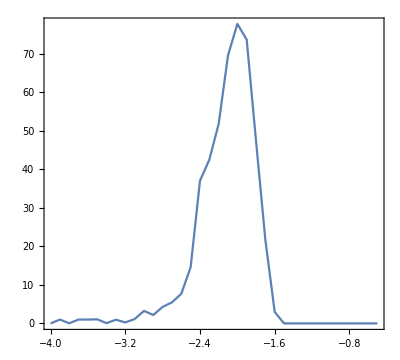

```mathematica
Plot[FCDataInterpol[i][x,BestFitFC[i]],{x,logs22thMin[i],logs22thMax[i]}]
```

## T2K

### Fluxes

InterpolatingFunction::dmval: Input value TraditionalForm`{0.000102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

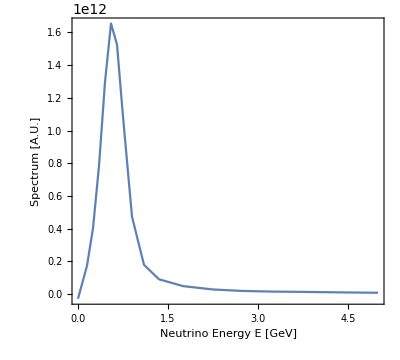

```mathematica
DataFiles={"0-code/glb/t2k/data/t2k-spectrum-2-ND280.dat"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
For[j=1,j≤6,j++,
DataInterpol[i,j]=Interpolation[Data[i]⟦All,{1,j+1}⟧,InterpolationOrder->1];
];
T2KSpectrumPlot[i]=Plot[DataInterpol[i,2][En],{En,0,5},FrameLabel->{"Neutrino Energy E [GeV]","Spectrum [A.U.]"}];
];
T2KSpectrumPlot[1]
```

```mathematica
For[i=1,i≤Length[DataFiles],i++,
OutputData[i]=Join[{
{"# T2K beam spectrum at ND280"},
{"# from Lorena Escudero's thesis, http://www.t2k.org/docs/thesis/070"},
{"#"},
{"#      E [GeV}  e       mu      tau   e-bar  mu-bar  tau-bar"}},
{"",#,Sequence@@Table[DataInterpol[i,j][#],{j,1,6}]}&/@Range[Data[i]⟦1,1⟧,Data[i]⟦-1,1⟧,0.05]];
];
Export["0-code/glb/t2k/t2k-spectrum-nd280.dat",OutputData[1],"Table"];
```

### Cross sections (non-QE)

```mathematica
DataCC=Cases[Import["0-code/glb/t2k/XCC.dat","Table"],{Repeated[_?NumericQ]}];
DataQE=Cases[Import["0-code/glb/t2k/XQE.dat","Table"],{Repeated[_?NumericQ]}];
DataNQE=Flatten/@Transpose[{DataCC⟦All,1⟧,DataCC⟦All,2;;-1⟧-DataQE⟦All,2;;-1⟧}];
```

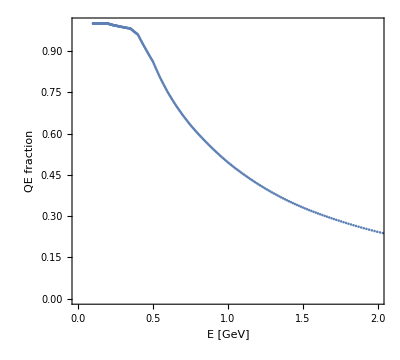

```mathematica
ListPlot[Transpose[{10^DataQE⟦All,1⟧,DataQE⟦All,3⟧/DataCC⟦All,3⟧}],PlotRange->{{0,2},All},FrameLabel->{"E [GeV]","QE fraction"}]
```

```mathematica
Export["0-code/glb/t2k/XNQE.dat",DataNQE];
```

### Smearing matrices

Note: in this section, energies are in GeV

```mathematica
Clear[GlbFile,Emin,Emax,BinSizes,BinCenters,BinBoundaries,SamplingMin,SamplingMax,SamplingPoints];
DataFilesGlb={"0-code/glb/t2k/t2k-fd.glb","0-code/glb/wbb_wc/wbb_wc_common_far.inc"};

For[i=1,i≤Length[DataFilesGlb],i++,
(* Load glb file *)
GlbFile[i]=StringReplace[Import[DataFilesGlb⟦i⟧,"Text"],{RegularExpression["(?m)//.*$"]:>""}];

(* Extract bin sizes, sampling points, and energy window *)
Emin[i]=ToExpression[StringCases[GlbFile[i],RegularExpression["(?m)\\$emin\\s*=\\s*(.*)$"]->"$1"]⟦1⟧];
Emax[i]=ToExpression[StringCases[GlbFile[i],RegularExpression["(?m)\\$emax\\s*=\\s*(.*)$"]->"$1"]⟦1⟧];
BinSizes[i]=ToExpression[StringCases[GlbFile[i],RegularExpression["(?s)\\$binsize\\s*=\\s*({.*?})"]->"$1"]⟦1⟧];
BinCenters[i]=Emin[i]+Accumulate[BinSizes[i]]-BinSizes[i]/2;
BinBoundaries[i]=Join[{Emin[i]},Emin[i]+Accumulate[BinSizes[i]]];

SamplingMin[i]=StringCases[GlbFile[i],RegularExpression["(?m)\\$sampling_min\\s*=\\s*(.*)$"]->"$1"];
If[SamplingMin[i]=={},SamplingMin[i]=Emin[i],SamplingMin[i]=ToExpression[SamplingMin[i]⟦1⟧]];
SamplingMax[i]=StringCases[GlbFile[i],RegularExpression["(?m)\\$sampling_max\\s*=\\s*(.*)$"]->"$1"];
If[SamplingMax[i]=={},SamplingMax[i]=Emax[i],SamplingMax[i]=ToExpression[SamplingMax[i]⟦1⟧]];
SamplingBinSizes[i]=StringCases[GlbFile[i],RegularExpression["(?s)\\$sampling_stepsize\\s*=\\s*({.*?})"]->"$1"];
If[SamplingBinSizes[i]=={},SamplingBinSizes[i]=BinSizes[i],SamplingBinSizes[i]=ToExpression[SamplingBinSizes[i]⟦1⟧]];
SamplingPoints[i]=SamplingMin[i]+Accumulate[SamplingBinSizes[i]]-SamplingBinSizes[i]/2;
];

i=1;

(* Gaussian smearing matrices for QE and non-QE events; resolutions from https://arxiv.org/abs/1307.3248, table 1 *)
IDTable={"NU_QE","NU_NQE","NUBAR_QE","NUBAR_NQE"};
σTable={0.114,0.105,0.073,0.136};
ΔTable={0.,-0.44,0.,-0.36};

E1=0.55;
E2=0.75;
σTable={{0.085,0.098},{0.070,0.110},{0.057,0.060},{0.100,0.120}};
ΔTable={{-0.010,-0.015},{-0.325,-0.390},{-0.020,-0.020},{-0.270,-0.310}};
Δ[j_,E_]:=ΔTable⟦j,1⟧+(E-E1)/(E2-E1)*(ΔTable⟦j,2⟧-ΔTable⟦j,1⟧);
σ[j_,E_]:=σTable⟦j,1⟧+(E-E1)/(E2-E1)*(σTable⟦j,2⟧-σTable⟦j,1⟧);
For[j=1,j≤Length[σTable],j++,
(*SmearingFunction[j][Etrue_,Ereco_]:=1/Sqrt[2π σ^2] Exp[-(Ereco-ΔTable⟦j⟧Sqrt[Etrue]-Etrue)^2/(2 σ^2)]/.σ->σTable⟦j⟧Sqrt[Etrue];*)
SmearingFunction[j][Etrue_,Ereco_]:=1/Sqrt[2π σ^2] Exp[-(Ereco-Δ[j,Etrue]-Etrue)^2/(2 σ^2)]/.σ->σ[j,Etrue];
SmearingIntegral[j][Etrue_,ErecoMin_,ErecoMax_]=Integrate[SmearingFunction[j][Etrue,Ereco],{Ereco,ErecoMin,ErecoMax}];
SmearingMatrix[j][i]=Table[SmearingIntegral[j][SamplingPoints[i]⟦m⟧,BinBoundaries[i]⟦k⟧,BinBoundaries[i]⟦k+1⟧],{k,1,Length[BinCenters[i]]},{m,1,Length[SamplingPoints[i]]}];

OutputString[j]="// Mapping of true neutrino energy to reconstructed energy\n"<>
"// in T2K\n"<>
"energy(#ERES_"<>IDTable⟦j⟧<>")<\n"<>
"  @energy =\n";
For[k=1,k≤Length[SmearingMatrix[j][i]],k++,
OutputString[j]=OutputString[j]<>"{0, "<>ToString[Length[SamplingPoints[i]]-1]<>StringJoin[Flatten[Table[{", ",ToString[CForm[SmearingMatrix[j][i]⟦k,m⟧]]},{m,1,Length[SmearingMatrix[j][i]⟦k⟧]}]]]<>"}";
If[k<Length[SmearingMatrix[j][i]],OutputString[j]=OutputString[j]<>":\n"];
];
OutputString[j]=OutputString[j]<>";\n>\n";
];
```

```mathematica
For[j=1,j≤Length[σTable],j++,
Export["0-code/glb/t2k/smear-cc-"<>StringReplace[ToLowerCase[IDTable⟦j⟧],"_"->"-"]<>".dat",OutputString[j]]
];
```

```mathematica
(* Read and interpolation NC smearing matrix -- not used *)
n=10;
SmearData[n]=StringReplace[Import["0-code/glb/t2k/nc_smear_nu_ereco.dat","Text"],
{RegularExpression["(?m)//.*$"]:>"",
"}:"->"},",
"};"->"}",
"e-"->"*^-"
}];
SmearingMatrix[n]=StringCases[SmearData[n],RegularExpression["(?s)@energy\\s*=\\s*(.*)>"]->"$1"]⟦1⟧;
SmearingMatrix[n]=ToExpression["{"<>SmearingMatrix[n]<>"}"]⟦All,3;;-1⟧;
```

```mathematica
(*Flatten[MapThread[Append,{Outer[{#1,#2}&,BinCenters[2],SamplingPoints[2]],SmearingMatrix[n]},2],{1,2}];*)
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

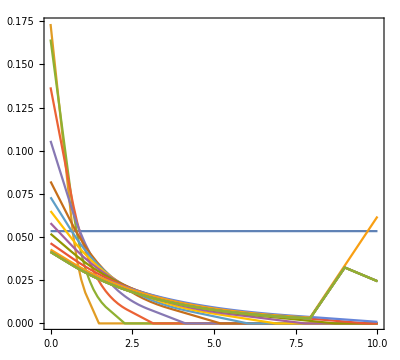

```mathematica
SMInterpol[n]=Interpolation[Select[MapThread[List,{BinCenters[2],#}],(#⟦2⟧≠0&)],InterpolationOrder->1]&/@Transpose[SmearingMatrix[n]];
SMInterpol[n]=Function[En,Evaluate[Max[#[En],0]]]&/@SMInterpol[n];
(*ListPlot[%]*)
Plot[Evaluate[Table[SMInterpol[n]⟦j⟧[En],{j,1,Length[SMInterpol[n]],5}]],{En,0,10}]
```

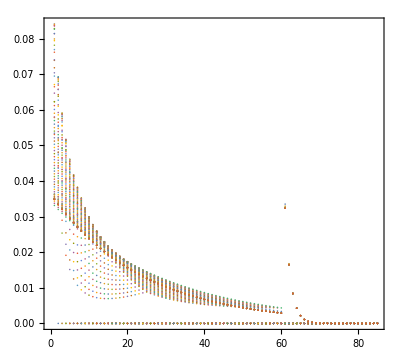

```mathematica
ListPlot[Transpose[SmearingMatrix[n]]]
```

### Efficiencies from WBB_WC (not accurate enough at low E)

```mathematica
(* Load efficiencies from WBB WC simulation and re-interpolate them *)
DataFilesGlb={"0-code/glb/t2k/t2k-fd.glb","0-code/glb/wbb_wc/wbb_wc_common_far.inc"};

For[i=1,i≤Length[DataFilesGlb],i++,
(* Load glb file *)
GlbFile[i]=StringReplace[Import[DataFilesGlb⟦i⟧,"Text"],{RegularExpression["(?m)//.*$"]:>""}];

(* Extract bin sizes, sampling points, and energy window *)
Emin[i]=ToExpression[StringCases[GlbFile[i],RegularExpression["(?m)\\$emin\\s*=\\s*(.*)$"]->"$1"]⟦1⟧];
Emax[i]=ToExpression[StringCases[GlbFile[i],RegularExpression["(?m)\\$emax\\s*=\\s*(.*)$"]->"$1"]⟦1⟧];
BinSizes[i]=ToExpression[StringCases[GlbFile[i],RegularExpression["(?s)\\$binsize\\s*=\\s*({.*?})"]->"$1"]⟦1⟧];
BinCenters[i]=Emin[i]+Accumulate[BinSizes[i]]-BinSizes[i]/2;
BinBoundaries[i]=Join[{Emin[i]},Emin[i]+Accumulate[BinSizes[i]]];

SamplingMin[i]=StringCases[GlbFile[i],RegularExpression["(?m)\\$sampling_min\\s*=\\s*(.*)$"]->"$1"];
If[SamplingMin[i]=={},SamplingMin[i]=Emin[i],SamplingMin[i]=ToExpression[SamplingMin[i]⟦1⟧]];
SamplingMax[i]=StringCases[GlbFile[i],RegularExpression["(?m)\\$sampling_max\\s*=\\s*(.*)$"]->"$1"];
If[SamplingMax[i]=={},SamplingMax[i]=Emax[i],SamplingMax[i]=ToExpression[SamplingMax[i]⟦1⟧]];
SamplingBinSizes[i]=StringCases[GlbFile[i],RegularExpression["(?s)\\$sampling_stepsize\\s*=\\s*({.*?})"]->"$1"];
If[SamplingBinSizes[i]=={},SamplingBinSizes[i]=BinSizes[i],SamplingBinSizes[i]=ToExpression[SamplingBinSizes[i]⟦1⟧]];
SamplingPoints[i]=SamplingMin[i]+Accumulate[SamplingBinSizes[i]]-SamplingBinSizes[i]/2;
];
```

```mathematica
i=2;
channels={"#nc_bg","#nu_e_signal"};
For[j=1,j≤Length[channels],j++,
ch[j]=StringCases[GlbFile[i],RegularExpression["(?s)channel\\("<>channels⟦j⟧<>"\\)<(.*?)>"]:>"$1"]⟦1⟧;
effPre[j]=ToExpression[StringCases[ch[j],RegularExpression["(?s)@pre_smearing_efficiencies\\s*=\\s*({.*?})"]:>"$1"]⟦1⟧];
effPost[j]=ToExpression[StringCases[ch[j],RegularExpression["(?s)@post_smearing_efficiencies\\s*=\\s*({.*?})"]:>"$1"]⟦1⟧];

effPreInterpol[j]=Interpolation[Transpose[{SamplingPoints[i],effPre[j]}],InterpolationOrder->1];
effPostInterpol[j]=Interpolation[Transpose[{BinCenters[i],effPost[j]}],InterpolationOrder->1];
];
```

InterpolatingFunction::dmval: Input value {0.501216} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

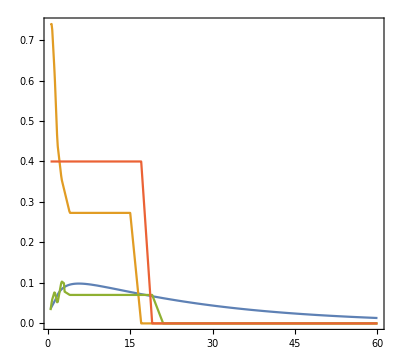

```mathematica
Plot[Evaluate[Join[Table[effPreInterpol[j][En],{j,1,Length[channels]}],Table[effPostInterpol[j][En],{j,1,Length[channels]}]]],{En,SamplingMin[i],SamplingMax[i]}]
```

```mathematica
effPreInterpol[1]/@SamplingPoints[1]
effPostInterpol[1]/@BinCenters[1]
```

InterpolatingFunction::dmval: Input value {0.025} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.075} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.125} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.0236603,0.024963,0.0262657,0.0275684,0.0288711,0.0301739,0.0314766,0.0327793,0.034082,0.0353847,0.0366875,0.0379902,0.0392929,0.0405956,0.0418801,0.0431585,0.0444335,0.0456981,0.0469627,0.0482232,0.0494822,0.0507414,0.052001,0.0532605,0.0545239,0.0557887,0.0570555,0.0583287,0.0596018,0.0613527,0.0632628,0.0650621,0.0665288,0.0679954,0.0693414,0.0706471,0.071917,0.0730796,0.0742422,0.0753103,0.0763471,0.0773562,0.0782827,0.0792091,0.0800631,0.0808929,0.0817015,0.0824464,0.0831913,0.08388,0.0845499,0.0852033,0.0858069,0.0864105,0.0869697,0.0875142,0.0880454,0.0885368,0.0890283,0.0894841,0.0907622,0.0925766,0.0940508,0.09524,0.0965819,0.0977147,0.098271,0.0983885,0.0979556}

InterpolatingFunction::dmval: Input value {0.025} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.075} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.125} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-0.0123423,-0.00759111,-0.00283995,0.00191121,0.00666237,0.0114135,0.0161647,0.0209159,0.025667,0.0304182,0.0351693,0.0399205,0.0446717,0.0494228,0.0532479,0.0567644,0.0599721,0.0622538,0.0645354,0.0668171,0.0690987,0.0713804,0.0736621,0.0759437,0.0762063,0.075796,0.0747126,0.0716102,0.0685078,0.0654054,0.0623029,0.0592005,0.0560981,0.0529957,0.0524477,0.0527513,0.0539063,0.0576158,0.0613252,0.0650347,0.0687442,0.0724537,0.0761632,0.0798726,0.0835821,0.0872916,0.0910011,0.0947105,0.09842,0.100538,0.102125,0.103181,0.102647,0.102112,0.101577,0.101041,0.100506,0.0999711,0.099436,0.093023,0.0778365,0.0756961,0.0735558,0.0714154,0.0703452,0.0703452,0.0703452,0.0703452,0.0703452}

### Plot event rates

```mathematica
(* Generate T2K spectrum *)
Run["ssh uni \"export LD_LIBRARY_PATH=/home/jkopp/local/software/root/lib/; "<>
"cd papers/sterile-nu/sim/0-code; "<>
"./nu -a SPECTRUM -e T2K -t TH12=0,TH23=0,TH13=0,DM21=0 > ../9-devel/t2k-spectrum-no-osc.dat\""];
Run["ssh uni \"export LD_LIBRARY_PATH=/home/jkopp/local/software/root/lib/; "<>
"cd papers/sterile-nu/sim/0-code; "<>
"./nu -a SPECTRUM -e T2K -t TH23=0.809407,TH13=0.206401,DM31=2.51e-3,DELTA_0=1.91 > ../9-devel/t2k-spectrum-osc.dat\""];

(*Run["ssh uni \"export LD_LIBRARY_PATH=/home/jkopp/local/software/root/lib/; "<>
"cd papers/sterile-nu/sim/0-code; "<>
"./nu -a SPECTRUM -e T2K -t TH23=0.785,TH13=0.0,DM31=2.4e-3 > ../9-devel/t2k-spectrum-osc.dat\""];*)
```

```mathematica
(* Extract the bin widths from the data *)
GetBinWidths[s_]:=Module[{t,j},(* This works only if the lower boundary of the 1st bin is at 0 *)
t={2*s⟦1⟧};
For[j=1,j≤Length[s]-1,j++,
AppendTo[t,2*Differences[s]⟦j⟧-t⟦j⟧];
];
Return[t];
];

(* Import T2K data *)
T2KDataFiles="0-code/glb/t2k/data/"<>#<>".dat"&/@{"nd280-data-mu-inclusive","t2k-data-mu-fd","t2k-data-e-fd"};
For[i=1,i≤Length[T2KDataFiles],i++,
DataT2K[i]={#⟦1⟧GeV,#⟦2⟧,#⟦3⟧,#⟦4⟧}//.NN&/@Cases[Import[T2KDataFiles⟦i⟧],{Repeated[_?NumericQ]}];
BinSizes[i]=GetBinWidths[DataT2K[i]⟦All,1⟧];
BinBoundaries[i]=Prepend[Accumulate[BinSizes[i]],0];
];

(* Import GLoBES results *)
DataFiles={
{"t2k-spectrum-no-osc",{1,1}}, (* Format: {filename,{exp. number, rule number}} *)
{"t2k-spectrum-no-osc",{2,1}},
{"t2k-spectrum-no-osc",{2,2}},
{"t2k-spectrum-osc",{1,1}},
{"t2k-spectrum-osc",{2,1}},
{"t2k-spectrum-osc",{2,2}}
}/.{s_String:>"9-devel/"<>s<>".dat"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=ToExpression[StringReplace[Import[DataFiles⟦i,1⟧,"Text"],RegularExpression["#.*\n"]->""]]⟦Sequence@@DataFiles⟦i,2⟧⟧;
BinBoundaries[i]=BinBoundaries[Mod[i-1,Length[T2KDataFiles]]+1];
BinCenters[i]=ListConvolve[{1/2,1/2},BinBoundaries[i]];

EventsSignal[i]={#⟦1⟧GeV,#⟦2⟧}//.NN&/@glbSignalTot[Data[i]]⟦1;;Length[BinBoundaries[i]]-1⟧;
EventsBG[i]={#⟦1⟧GeV,#⟦2⟧}//.NN&/@glbBGTot[Data[i]]⟦1;;Length[BinBoundaries[i]]-1⟧;
EventsTotal[i]={#⟦1⟧GeV,#⟦2⟧}//.NN&/@glbSignalBGTot[Data[i]]⟦1;;Length[BinBoundaries[i]]-1⟧;

PlotListSignal[i]=MapThread[{#1/GeV,#2⟦2⟧}//.NN&,{BinBoundaries[i],Append[EventsSignal[i],EventsSignal[i]⟦-1⟧]}];
MyPlotSignal[i]=ListPlot[PlotListSignal[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[Thick,Blue,Dashed]];

PlotListBG[i]=MapThread[{#1/GeV,#2⟦2⟧}//.NN&,{BinBoundaries[i],Append[EventsBG[i],EventsBG[i]⟦-1⟧]}];
MyPlotBG[i]=ListPlot[PlotListBG[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[Thick,Blue,Dashed]];

PlotListTotal[i]=MapThread[{#1/GeV,#2⟦2⟧}//.NN&,{BinBoundaries[i],Append[EventsTotal[i],EventsTotal[i]⟦-1⟧]}];
MyPlotTotal[i]=ListPlot[PlotListTotal[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[Thick,Blue]];
];

(* Normalization *)
Total[DataT2K[2]⟦All,3⟧]/Total[EventsTotal[2]⟦All,2⟧]
```

0.966951

```mathematica
For[i=1,i≤Length[T2KDataFiles],i++,
PlotListObs[i]={{#⟦1⟧/GeV,#⟦2⟧},ErrorBar[N[Sqrt[#⟦2⟧]]]}//.NN&/@DataT2K[i];
MyPlotObs[i]=ErrorListPlot[PlotListObs[i],PlotRange->All,PlotStyle->Directive[Thick,Black],PlotMarkers->{Automatic,10}];

PlotListT2KNoOsc[i]=MapThread[{#1/GeV,#2⟦3⟧}//.NN&,{BinBoundaries[i],Append[DataT2K[i],DataT2K[i]⟦-1⟧]}];
MyPlotT2KNoOsc[i]=ListPlot[PlotListT2KNoOsc[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[Thick,Black]];

PlotListT2K[i]=MapThread[{#1/GeV,#2⟦4⟧}//.NN&,{BinBoundaries[i],Append[DataT2K[i],DataT2K[i]⟦-1⟧]}];
MyPlotT2K[i]=ListPlot[PlotListT2K[i],InterpolationOrder->0,Joined->True,PlotStyle->Directive[Thick,Red]];
];
```

```mathematica
MyLegend=Framed[Grid[{
{LegendLine[Directive[Thick,Black]],"T2K (no. osc)"},
{LegendLine[Directive[Thick,Red]],"T2K (bf. osc)"},
{LegendLine[Directive[Thick,Blue]],"my code"},
{LegendDataPoint[HorizontalError->False,PlotStyle->Directive[Thick,Black]],"T2K data"}
},BaseStyle->{FontSize->18},Spacings->{Automatic,Automatic},Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];
MyPlot[1]=Grid[{Table[
Show[
MyPlotObs[i],MyPlotT2KNoOsc[i],MyPlotT2K[i],
MyPlotTotal[i],MyPlotTotal[i+3],
PlotRange->{{0,2},{0,1.3Max[Flatten[DataT2K[i]⟦All,2;;4⟧]]+3}},GridLines->Automatic,
FrameLabel->{"Neutrino Energy E [GeV]","Events / bin"},
Epilog->{Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}]}
],{i,1,Length[T2KDataFiles]}]}]
```

-Graphics-

#### Efficiencies

Procedure for recomputing ND efficiencies:
1. Uncomment lines labeld “For debugging purposes and to compute efficiencies in Mathematica” in t2k-nd280.glb, remove previous efficiencies
2. Run section “Plot event rates” above
3. Run code below to compute efficiencies
4. Copy & paste to t2k-nd280.glb

```mathematica
(* ND efficiencies *)
i=1;
ND280Eff=If[#⟦2⟧>0,#⟦1⟧/#⟦2⟧,0]&/@Transpose[{DataT2K[i]⟦All,3⟧,EventsTotal[i]⟦All,2⟧}];
OutputString[i]="%eff_mu = {\n  ";
For[j=1,j≤Length[ND280Eff],j++,
OutputString[i]=OutputString[i]<>ToString[ND280Eff⟦j⟧];
If[j<Length[ND280Eff],OutputString[i]=OutputString[i]<>", "];
If[Mod[j,5]==0,OutputString[i]=OutputString[i]<>"\n  "];
];
OutputString[i]=OutputString[i]<>" }"
```

%eff_mu = {
  0, 0.279751, 0.585663, 0.929422, 1.13341, 
  1.12019, 1.09724, 1.1379, 1.27118, 1.30263, 
  1.40955, 1.46639, 1.54908, 1.52349, 1.53652, 
  1.56106, 1.60375, 1.71539, 1.73776, 1.72501, 
  1.70777, 1.73911, 1.87304, 1.72717, 1.73762, 
  1.55798, 1.84651, 1.79551, 1.45269, 1.69024, 
  1.42346, 1.62941, 1.43674, 1.67374, 1.62755, 
  1.46151, 1.5894, 1.61435, 1.73367, 12.2245
   }

Procedure for recomputing FD efficiencies:
1. Comment out line labeled “Rescale to T2K MC” in code below
2. Run code below to compute efficiencies
3. Run section “Plot event rates” above
4. Reintroduce line labeled “Rescale to T2K MC” in code below
5. Run code below again
6. Rerun section “Plot event rates” above to verify

```mathematica
(* The following numbers are based on
NDCorrectionNuMu[E_]:=1/Piecewise[{{1.029, 0≤E/GeV<0.4}, {1.022, 0.4≤E/GeV<0.5}, {0.995, 0.5≤E/GeV<0.6}, {0.966, 0.6≤E/GeV<0.7}, {0.934, 0.7≤E/GeV<1}, {0.992, 1≤E/GeV<1.5}, {1.037, 1.5≤E/GeV<2.5}, {1.054, 2.5≤E/GeV<3.5}, {1.035, 3.5≤E/GeV<5}, {0.975, 5≤E/GeV<7}, {0.943, 7≤E/GeV<30}}]//.NN;
NDCorrectionNuMuBar[E_]:=1/Piecewise[{{1.030, 0≤E/GeV<0.7}, {1.011, 0.7≤E/GeV<1}, {1.007, 1≤E/GeV<1.5}, {1.026, 1.5≤E/GeV<2.5}, {1.008, 2.5≤E/GeV<30}}]//.NN;
NDCorrectionQE[E_]:=1/Piecewise[{{0.966, 0≤E/GeV<1.5}, {0.931, 1.5≤E/GeV<3.5}, {0.852, 3.5≤E/GeV<30}}]//.NN;
NDCorrectionNQE[E_]:=1/Piecewise[{{1.265, 0≤E/GeV<2.5}, {1.122, 2.5≤E/GeV<30}}]//.NN;
EffCorrectorFunction={
NDCorrectionNuMu[#]*NDCorrectionQE[#]&,
NDCorrectionNuMu[#]*NDCorrectionNQE[#]&,
NDCorrectionNuMuBar[#]*NDCorrectionQE[#]&,
NDCorrectionNuMuBar[#]*NDCorrectionNQE[#]&
};
```

```mathematica
(* FD efficiencies *)
EffIDs={"%eff_nu_qe","%eff_nu_nqe","%eff_nubar_qe","%eff_nubar_nqe"};
DataFilesEff="0-code/glb/t2k/data/"<>#<>".dat"&/@{"t2k-eff-nu-qe","t2k-eff-nu-nqe","t2k-eff-nubar-qe","t2k-eff-nubar-nqe"};
DataFilesGlb={"0-code/glb/t2k/t2k-fd.glb"};
For[i=1,i≤Length[DataFilesGlb],i++,
GlbFile[i]=Import[DataFilesGlb⟦i⟧,"Text"];
];
For[i=1,i≤Length[DataFilesEff],i++,
DataEff[i]={#⟦1⟧GeV,#⟦2⟧}//.NN&/@Cases[Import[DataFilesEff⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
DataEffInterpol[i]=Interpolation[DataEff[i],InterpolationOrder->1,"ExtrapolationHandler"->{If[#≤DataEff[i]⟦1,1⟧,DataEff[i]⟦1,2⟧,DataEff[i]⟦-1,2⟧]&,"WarningMessage"->False}];
DataEffRebinned[i]={#,DataEffInterpol[i][#]}&/@BinCenters[2];

(* Rescale to T2K MC, undo ND normalization *)
DataEffRebinned[i]*=PlotListT2KNoOsc[2]⟦1;;-2,2⟧/PlotListTotal[2]⟦1;;-2,2⟧*(EffCorrectorFunction⟦i⟧[#]//.NN&/@BinCenters[2]);

OutputString[i]=EffIDs⟦i⟧<>" = {\n  ";
For[j=1,j≤Length[DataEffRebinned[i]],j++,
OutputString[i]=OutputString[i]<>ToString[DataEffRebinned[i]⟦j,2⟧];
If[j<Length[DataEffRebinned[i]],OutputString[i]=OutputString[i]<>", "];
If[Mod[j,5]==0,OutputString[i]=OutputString[i]<>"\n  "];
];
OutputString[i]=OutputString[i]<>" }";
GlbFile[1]=StringReplace[GlbFile[1],RegularExpression["(?m)(?s)^"<>EffIDs⟦i⟧<>"\\s*=\\s*{.*?}"]:>OutputString[i]];
];
```

```mathematica
Export[DataFilesGlb⟦1⟧,GlbFile[1],"Text"];
```

### Fit results — verification of 3-flavor fit

FIXME Current code is not consistent — T2K FD prediction might be affected by sterile neutrinos already

Comparing to Loredana Escudero’s thesis, http://www.t2k.org/docs/thesis/070, fig. 5.18 (p. 153)

```mathematica
Clear[T2KContours];
T2KFitFiles="0-code/glb/t2k/data/"<>#<>".dat"&/@{
"t2k-fit-th23-dm31-68","t2k-fit-th23-dm31-90",
"t2k-fit-th23-th13-68","t2k-fit-th23-th13-90",
"t2k-fit-th13-delta-68","t2k-fit-th13-delta-90"
};
For[i=1,i≤Length[T2KFitFiles],i++,
T2KContours[i]=Cases[Import[T2KFitFiles⟦i⟧],{Repeated[_Real|_Integer]}];
];

DataFiles="9-devel/"<>#<>".dat"&/@{"t2k-3f-th23dm31","t2k-3f-th23th13","t2k-3f-th13delta"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]=Cases[Import[DataFiles⟦i⟧],{Repeated[_Real|_Integer]}];
Chi2Min[i]=Min[Flatten[Data[i]⟦All,{-2,-1}⟧]];
];
Data[1]={Sin[#⟦1⟧]^2,#⟦2⟧-8*^-5,#⟦3⟧}&/@Data[1];
Data[2]={Sin[#⟦1⟧]^2,Sin[#⟦2⟧]^2,#⟦3⟧}&/@Data[2];
Data[3]={Sin[#⟦1⟧]^2,If[#⟦2⟧>π,#⟦2⟧-2π,#⟦2⟧],#⟦3⟧}&/@Data[3];
For[i=1,i≤Length[DataFiles],i++,
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
];
```

InterpolatingFunction::dmval: Input value {7.14286×10^-6,-3.14114} lies outside the range of data in the interpolating function. Extrapolation will be used.

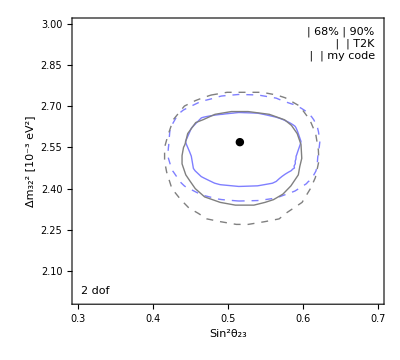
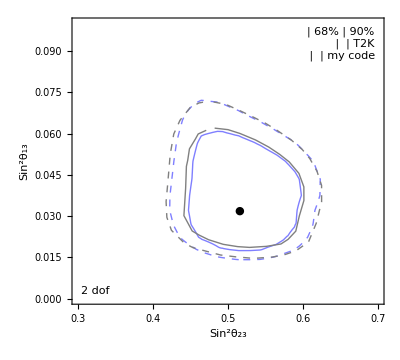
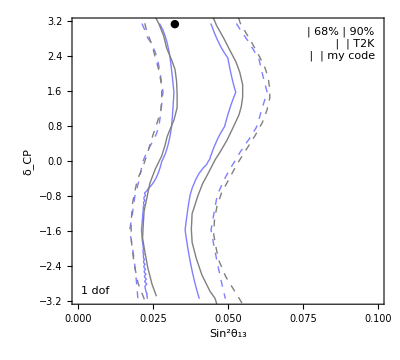
-Graphics- | -Graphics-
-Graphics- |

```mathematica
MyLegend=Framed[Grid[{
{"","68%","90%"},
{LegendLine[Directive[Gray]],LegendLine[Directive[Gray,Dashed]],"T2K"},
{LegendLine[Directive[Thick,Blue]],LegendLine[Directive[Thick,Blue,Dashed]],"my code"}
},BaseStyle->{FontSize->18},Spacings->{Automatic,Automatic},Alignment->{Left,Center}],Background->RGBColor[1,1,1,.8]];

i=1;
MyPlot[i]=Show[
ContourPlot[DataInterpol[i][sth23,dm31*1*^-3]-Chi2Min[i],{sth23,0.3,0.7},{dm31,2,3},Contours->{χ2[2,0.32],χ2[2,0.1]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]}],
Graphics[{Gray,Line[{#⟦1⟧,#⟦2⟧/1*^-3}&/@T2KContours[2i-1]],Dashed,Line[{#⟦1⟧,#⟦2⟧/1*^-3}&/@T2KContours[2i]]}],
FrameLabel->{"Sin^2θ_23","Δm_32^2 [10^-3 eV^2]"},
Epilog->{Text["2 dof",Scaled[{0.03,0.03}],{-1,-1}],
Text["●",Sort[{#⟦1⟧,#⟦2⟧*1*^3,#⟦3⟧}&/@Data[i],OrderedQ[{#1⟦3⟧,#2⟦3⟧}]&]⟦1,{1,2}⟧],
Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}]}];

i=2;
MyPlot[i]=Show[
ContourPlot[DataInterpol[i][sth23,sth13]-Chi2Min[i],{sth23,0.3,0.7},{sth13,0,0.1},Contours->{χ2[2,0.32],χ2[2,0.1]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]}],
Graphics[{Gray,Line[T2KContours[2i-1]],Dashed,Line[T2KContours[2i]]}],
FrameLabel->{"Sin^2θ_23","Sin^2θ_13"},
Epilog->{Text["2 dof",Scaled[{0.03,0.03}],{-1,-1}],
Text["●",Sort[Data[i],OrderedQ[{#1⟦3⟧,#2⟦3⟧}]&]⟦1,{1,2}⟧],
Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}]}];

i=3;
MyPlot[i]=Show[
ContourPlot[DataInterpol[i][sth13,delta]-Chi2Min[i],{sth13,0,0.1},{delta,-π,π},Contours->{χ2[1,0.32],χ2[1,0.1]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Blue],Directive[Thick,Blue,Dashed]}],
Graphics[{Gray,Line[{#⟦1⟧,#⟦2⟧}&/@T2KContours[2i-1]],Dashed,Line[{#⟦1⟧,#⟦2⟧}&/@T2KContours[2i]]}],
FrameLabel->{"Sin^2θ_13","δ_CP"},
Epilog->{Text["1 dof",Scaled[{0.03,0.03}],{-1,-1}],
Text["●",Sort[Data[i],OrderedQ[{#1⟦3⟧,#2⟦3⟧}]&]⟦1,{1,2}⟧],
Inset[MyLegend,Scaled[{0.97,0.97}],{1,1}]}];

Grid[{{MyPlot[1],MyPlot[2]},{MyPlot[3]}}]
```

### Fit results — 3+1

```mathematica
DataFiles="3-3p1/"<>#&/@{"th24dm41-t2k.dat"};
DataFiles="results/"<>#&/@{"th24dm41-t2k.dat"};
For[i=1,i≤Length[DataFiles],i++,
Data[i]={Sin[#⟦1⟧]^2,#⟦2⟧,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import[DataFiles⟦i⟧,"Table"],{Repeated[_?NumericQ]}];
Data[i]=Select[Data[i],#⟦2⟧<2&];
DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->1];
Chi2Min[i]=Min[Data[i]⟦All,3⟧];
];
Chi2Min[1]
```

76.8515

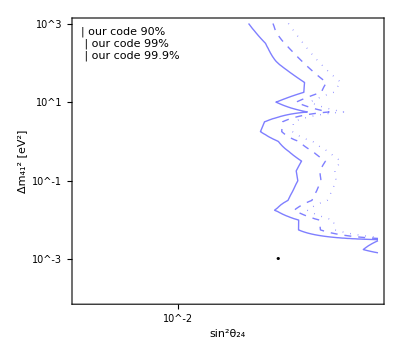

```mathematica
i=1;
MyLegend=Framed[Grid[{
{LegendLine[Directive[Thick,Blue]],"our code 90%"},
{LegendLine[Directive[Thick,Blue,Dashed]],"our code 99%"},
{LegendLine[Directive[Thick,Blue,Dotted]],"our code 99.9%"}
},Alignment->{Left,Center}]];
Grid[{{
(*ContourPlot[DataInterpol[i][s2th24,logdm41]-Chi2Min[i],{s2th24,0,0.12},{logdm41,-4,3},Contours->{χ2[2,0.1],χ2[2,0.01]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Blue]},
FrameLabel->{"sin^2θ_24","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{Automatic,Automatic}},
Epilog->{Text["•",Select[Data[i],#⟦3⟧==Chi2Min[i]&]⟦1,1;;2⟧]}],*)
Show[
ContourPlot[DataInterpol[i][10^logs2th24,logdm41]-Chi2Min[i],{logs2th24,-3,0},{logdm41,-4,3},Contours->{χ2[2,0.1],χ2[2,0.01],χ2[2,0.001]},PlotRange->Full,ContourShading->False,ContourStyle->{Directive[Thick,Blue],Directive[Thick,Blue,Dashed],Directive[Thick,Blue,Dotted]}],
FrameLabel->{" sin^2θ_24","Δm_41^2 [eV^2]"},FrameTicks->{{LogTicks[-5,5],LogTicksNoLabel[-5,5]},{LogTicks[-5,5],LogTicksNoLabel[-5,5]}},Epilog->{
Text["•",({Log10[#⟦1⟧],#⟦2⟧}&/@Select[Data[i],#⟦3⟧==Chi2Min[i]&])⟦1,1;;2⟧],
Inset[MyLegend,Scaled[{0.03,0.97}],{-1,1}]
}
]
}}]
```

```mathematica
2π En/dmsq/km//.Union[NN,{dmsq->1*^3,En->0.5GeV}]
dmsq L/2(1/n-1/(n+1))//.Union[NN,{n->1000,dmsq->1*^3,L->280meter}]
dmsq L/2(1/n-1/(n+1))//.Union[NN,{n->1000000,dmsq->1*^3,L->295km}]
```

0.000618911

709930.

748.709

## Double Chooz

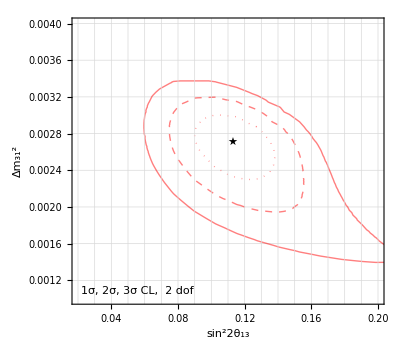

Best fit point: {0.112727,0.0027}

{0.128727,0.0967272}

```mathematica
MyPlot[1]=GlbPlot2d["results/th13dm31-dc.dat",P1Function->(Sin[2#]^2&),Contours->{χ2[2,PValue[1]],χ2[2,PValue[2]],χ2[2,PValue[3]]},ContourStyle->{Directive[Red,Dotted],Directive[Red,Dashed],Directive[Red]}];
Show[
MyPlot[1],
PlotRange->{{0.02,0.2},{1*^-3,4*^-3}},FrameLabel->{"sin^22θ_13","Δm_31^2"},
FrameTicks->Automatic,GridLines->{Range[0,0.2,0.01],Automatic},Epilog->{
Text["1σ, 2σ, 3σ CL,  2 dof",Scaled[{0.03,0.03}],{-1,-1}],
Text["★",BestFit]
}
]
Print["Best fit point: ",BestFit]
{BestFit⟦1⟧+0.016,BestFit⟦1⟧-0.016}
```

{0.119492,90.9099}

Best fit: 0.119477+0.0159419-0.0161347

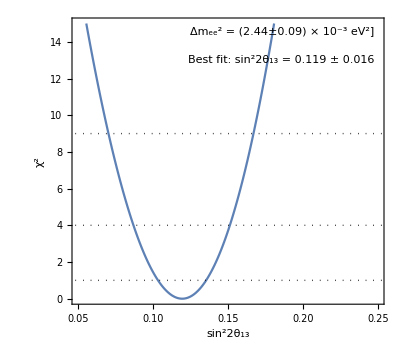

```mathematica
i=1;
Clear[Data,bfp,xMin,x1σUpper,x1σLower];
Data[i]={Sin[2#⟦1⟧]^2,Min[#⟦2⟧,#⟦3⟧]}&/@Cases[Import["results/th13chi2-dc.dat","Table"],{Repeated[_?NumericQ]}];
bfp[i]=First[Sort[Data[i],OrderedQ[{#1⟦2⟧,#2⟦2⟧}]&]]
Data[i]={#⟦1⟧,#⟦2⟧-bfp[i]⟦2⟧}&/@Data[i];

DataInterpol[i]=Interpolation[Data[i],InterpolationOrder->3];
xMin[i]=FindArgMin[DataInterpol[i][x],{x,0.1,0.15}]⟦1⟧;
x1σUpper[i]=x/.FindRoot[DataInterpol[i][x]==χ2[1,PValue[1]],{x,xMin[i]+0.05}];
x1σLower[i]=x/.FindRoot[DataInterpol[i][x]==χ2[1,PValue[1]],{x,xMin[i]-0.05}];
Print["Best fit: ",xMin[i],"+",x1σUpper[i]-xMin[i],"-",xMin[i]-x1σLower[i]];
ListPlot[Data[i],Joined->True,PlotRange->{{0.05,0.25},{0,15}},
FrameLabel->{"sin^22θ_13","χ^2"},
Epilog->{
Black,Dotted,
Line[{{-1,χ2[1,PValue[1]]},{2,χ2[1,PValue[1]]}}],
Line[{{-1,χ2[1,PValue[2]]},{2,χ2[1,PValue[2]]}}],
Line[{{-1,χ2[1,PValue[3]]},{2,χ2[1,PValue[3]]}}],
Text["Δm_ee^2 = (2.44±0.09) × 10^-3 eV^2]",Scaled[{0.97,0.97}],{1,1},Background->GrayLevel[1,.7]],
Text["Best fit: sin^22θ_13 = "<>ToString[Round[xMin[i],0.001]]<>" ± "<>ToString[Round[(x1σUpper[i]-x1σLower[i])/2,0.001]],Scaled[{0.97,0.87}],{1,1},Background->GrayLevel[1,.7]]
}]
```

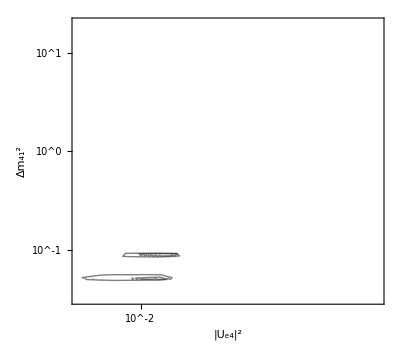

```mathematica
Show[GlbPlot2d["results/th14dm41-dc.dat",P1Function->(Log10[Max[1*^-4,Sin[#]^2]]&),Contours->{χ2[2,0.001],χ2[2,0.01],χ2[2,0.1]},ContourStyle->{Directive[Black,Thick]}],PlotRange->{{-2.5,-0.1},{-1.5,1.3}},
FrameLabel->{"|U_e4|^2","Δm_41^2"},FrameTicks->{{LogTicks[-4,4],LogTicksNoLabel[-4,4]},{LogTicks[-4,4],LogTicksNoLabel[-4,4]}},
Epilog->{Red,Dashed,Black(*Inset[MyLegend,Scaled[{0.97,0.5}],{1,0}],*)(*Text["95% CL, 2 dof",Scaled[{0.03,0.03}],{-1,-1}]*)}]
```

## Daya Bay

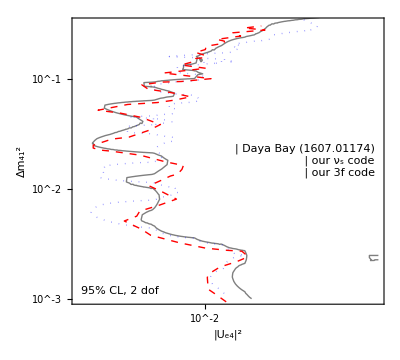

```mathematica
MyLegend=Framed[Grid[{
{LegendLine[Directive[Red,Dashed]],"Daya Bay (1607.01174)"},
{LegendLine[Directive[Black,Thick]],"our ν_s code"},
{LegendLine[Directive[Blue,Dotted]],"our 3f code"}
},Alignment->{Left,Center}]];
DBData={Log10[Sin[ArcSin[Sqrt[#⟦1⟧]]/2]^2],Log10[#⟦2⟧]}&/@Cases[Import["0-code/glb/daya-bay/data/db-exclusion.dat","Table"],{Repeated[_?NumericQ]}];
Show[
GlbPlot2d["results/th14dm41-db-sterile.dat",P1Function->(Log10[Max[1*^-4,Sin[#]^2]]&),Contours->{χ2[2,0.05]},ContourStyle->{Directive[Black,Thick]}],
GlbPlot2d["results/th14dm41-db-3f.dat",P1Function->(Log10[Max[1*^-4,Sin[#]^2]]&),Contours->{χ2[2,0.05]},ContourStyle->{Directive[Blue,Dotted]}],
PlotRange->{{-3.1,-0.5},{-3,-0.5}},
FrameLabel->{"|U_e4|^2","Δm_41^2"},FrameTicks->{{LogTicks[-4,4],LogTicksNoLabel[-4,4]},{LogTicks[-4,4],LogTicksNoLabel[-4,4]}},
Epilog->{Red,Dashed,Line[DBData],Black,Inset[MyLegend,Scaled[{0.97,0.5}],{1,0}],Text["95% CL, 2 dof",Scaled[{0.03,0.03}],{-1,-1}]}]
```

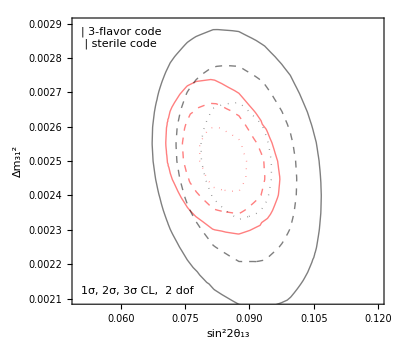

```mathematica
MyLegend=Framed[Grid[{
{LegendLine[Directive[Red]],"3-flavor code"},
{LegendLine[Directive[Black]],"sterile code"}
},Alignment->{Left,Center}]];
Show[
GlbPlot2d["results/th13dm31-db-3f.dat",P1Function->(Sin[2#]^2&),ContourStyle->{Directive[Red,Dotted],Directive[Red,Dashed],Directive[Red]}],
GlbPlot2d["results/th13dm31-db-sterile.dat",P1Function->(Sin[2#]^2&),ContourStyle->{Directive[Black,Dotted],Directive[Black,Dashed],Directive[Black]}],
PlotRange->{{0.05,0.12},{2.1*^-3,2.9*^-3}},FrameLabel->{"sin^22θ_13","Δm_31^2"},
FrameTicks->Automatic,Epilog->{
Text["1σ, 2σ, 3σ CL,  2 dof",Scaled[{0.03,0.03}],{-1,-1}],
Inset[MyLegend,Scaled[{0.03,0.97}],{-1,1}]}
]
```

## DANSS

### Import and fit DANSS energy resolution function

0.320403+0.0221976 En-0.1345 √En+0.0367406/(√En)

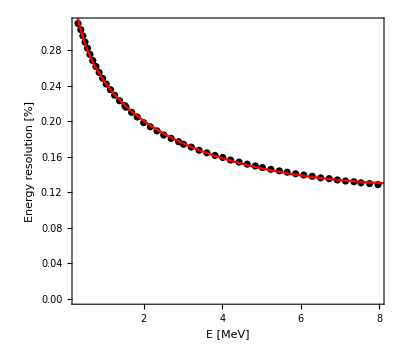

```mathematica
DataDANSSeres=Cases[Import["0-code/reactors/Data_DANSS/danss-eres-1412.0817.dat","Table"],{Repeated[_?NumericQ]}];
f=α/Sqrt[En]+β+γ*Sqrt[En]+δ*En;
fFit=FindFit[DataDANSSeres,f,{α,β,γ,δ},En];
f/.fFit
Show[ListPlot[DataDANSSeres,PlotStyle->Black],
Plot[f/.fFit,{En,0,10},PlotStyle->Red],
FrameLabel->{"E [MeV]","Energy resolution [%]"}
]
```

### Results

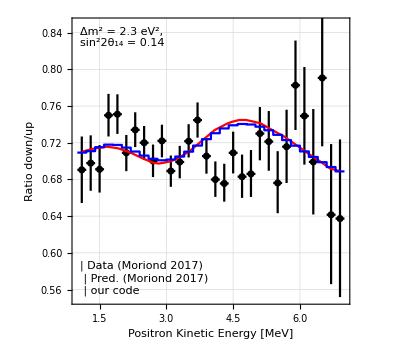

```mathematica
MyLegend=Framed[Grid[{
{LegendDataPoint[PlotStyle->Directive[Thick]],"Data (Moriond 2017)"},
{LegendLine[Directive[Red,Dashed]],"Pred. (Moriond 2017)"},
{LegendLine[Directive[Blue,Thick]],"our code"}
},Alignment->{Left,Center}],Background->GrayLevel[1,.7]];
DANSSUpDownData=Cases[Import["0-code/reactors/Data_DANSS/danss-up-down-moriond2017.dat","Table"],{Repeated[_?NumericQ]}];
DANSSUpDownTheirPred=Cases[Import["0-code/reactors/Data_DANSS/danss-up-down-moriond2017-pred.dat","Table"],{Repeated[_?NumericQ]}];
DANSSUpDownOurPred=Cases[Import["results/danss-spectrum-test.dat","Table"],{Repeated[_?NumericQ]}];
Show[
ErrorListPlot[{{#⟦1⟧,#⟦2⟧},ErrorBar[0.1,#⟦2⟧-{#⟦3⟧,#⟦4⟧}]}&/@DANSSUpDownData,PlotStyle->Black],
ListPlot[DANSSUpDownTheirPred,Joined->True,PlotStyle->Red],
ListPlot[DANSSUpDownOurPred,Joined->True,PlotStyle->Blue],
PlotRange->{All,{0.55,0.85}},GridLines->Automatic,
FrameLabel->{"Positron Kinetic Energy [MeV]","Ratio down/up"},
Epilog->{Inset[MyLegend,Scaled[{0.03,0.03}],{-1,-1}],
Text[Style["Δm^2 = 2.3 eV^2,\nsin^22θ_14 = 0.14",LineSpacing->{1.1,0}],Scaled[{0.03,0.97}],{-1,1},Background->GrayLevel[1,.7]]}
]
```

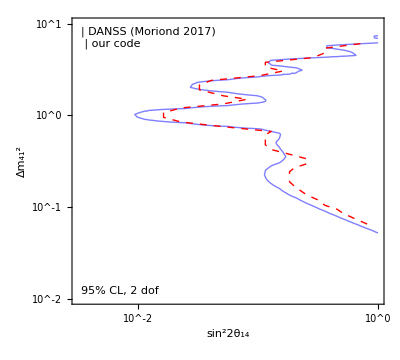

```mathematica
MyLegend=Framed[Grid[{
{LegendLine[Directive[Red,Dashed]],"DANSS (Moriond 2017)"},
{LegendLine[Directive[Blue,Thick]],"our code"}
},Alignment->{Left,Center}]];
DANSSExclusion={Log10[#⟦1⟧],Log10[#⟦2⟧]}&/@Cases[Import["0-code/reactors/Data_DANSS/danss-exclusion-moriond2017.dat","Table"],{Repeated[_?NumericQ]}];
Show[
GlbPlot2d["results/th14dm41-danss.dat",P1Function->(Log10[Max[1*^-4,Sin[2#]^2]]&),Contours->{χ2[2,0.05]},ContourStyle->{Directive[Blue,Thick]}],
PlotRange->{{-2.5,0},{-2,1}},
FrameLabel->{"sin^22θ_14","Δm_41^2"},FrameTicks->{{LogTicks[-4,4],LogTicksNoLabel[-4,4]},{LogTicks[-4,4],LogTicksNoLabel[-4,4]}},
Epilog->{Red,Dashed,Line[DANSSExclusion],Black,Dashing[{}],Inset[MyLegend,Scaled[{0.03,0.97}],{-1,1}],Text["95% CL, 2 dof",Scaled[{0.03,0.03}],{-1,-1}]}]
```

```mathematica
(* average distance between neutrino production and detection vertices *)
dD=12.7;
RP=1.55; (* reactor core radius *)
hP=3.5; (* reactor core height *)
XD=1.; (* edge length of detector *)
Norm[{rP Cos[θP],rP Sin[θP],zP}-{xD,yD,zD}]
1/(π RP^2 hP*XD^3)NIntegrate[rP %,{rP,0,RP},{θP,0,2π},{zP,-hP/2,hP/2},{xD,-XD/2,XD/2},{yD,-XD/2,XD/2},{zD,dD-XD/2,dD+XD/2}]
```

√(Abs[rP cos(θP)-xD]^2+Abs[rP sin(θP)-yD]^2+Abs[zP-zD]^2)

12.7541

```mathematica
(* Integrals over size of the reactor core *)
$Assumptions={L2>L1>0};
Integrate[Sin[dmsq L/(4En)]^2,{L,L1,L2}]
Integrate[Sin[dmsq L/(4En)]^2/L^2,{L,L1,L2}]
Integrate[1/L^2,{L,L1,L2}]
0.5*eV^2 meter/MeV//.NN
```

(2 En sin((dmsq L1)/(2 En))-2 En sin((dmsq L2)/(2 En))+dmsq (L2-L1))/(2 dmsq)

(dmsq ((dmsq L2)/(2 En)-(dmsq L1)/(2 En)))/(4 En)+(sin^2((dmsq L1)/(4 En)))/L1-(sin^2((dmsq L2)/(4 En)))/L2

1/L1-1/L2

2.538

## NEOS

### Interpolate Daya Bay Covariance Matrix

```mathematica
DataDBSpectrum=Cases[Import["0-code/reactors/Data_NEOS/db-unfolded-spectrum.dat","Table"],{a_,"-",b_,c_}:>c];
DataCMRaw=Import["0-code/reactors/Data_NEOS/db-cov-matrix.dat","Table"];
DataCMBinEdges=Union[Flatten[Cases[DataCMRaw,{"#",a_,"-",b_}:>{a,b}]]];
DataCMBinCenters=MovingAverage[DataCMBinEdges,2];
DataCM=Cases[DataCMRaw,{Repeated[_?NumericQ]}]/Outer[Times,DataDBSpectrum,DataDBSpectrum];
DataCMBinned=Flatten[MapThread[Append[#1,#2]&,{Outer[{#1,#2}&,DataCMBinCenters,DataCMBinCenters],DataCM},2],{1,2}];
DataCMInterpol=Interpolation[DataCMBinned,InterpolationOrder->1];

NEOSBinEdges=Range[1,7,0.1]+0.8; (* +0.8 to go from prompt energy to neutrino energy *)
NEOSBinCenters=MovingAverage[NEOSBinEdges,2];
NEOSCMBinned=Append[#,DataCMInterpol[Sequence@@#]]&/@Flatten[Outer[{#1,#2}&,NEOSBinCenters,NEOSBinCenters],{1,2}];
Export["0-code/reactors/Data_NEOS/db-cov-matrix-for-neos.dat",
Partition[NEOSCMBinned⟦All,3⟧,Length[NEOSBinCenters]],"Table"];

Grid[{{
ListDensityPlot[DataCMBinned,InterpolationOrder->0,ColorFunctionScaling->True,PlotRange->{{1.8,9},{1.8,9}},
FrameLabel->{"E [MeV]","E [MeV]"}],
ListDensityPlot[NEOSCMBinned,InterpolationOrder->0,ColorFunctionScaling->True,PlotRange->{{1.8,9},{1.8,9}},
FrameLabel->{"E [MeV]","E [MeV]"}]
}}]
```

InterpolatingFunction::dmval: Input value {1.85,1.85} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.85,1.95} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.85,2.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

### Results — Spectrum

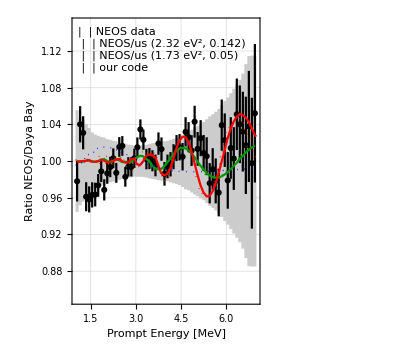

```mathematica
SystTable=Append[NEOSRatioData⟦All,{1,4}⟧,{NEOSRatioData⟦-1,1⟧+0.1,NEOSRatioData⟦-1,4⟧}];
NEOSRatioData=Cases[Import["0-code/reactors/Data_NEOS/ratio_data.dat","Table"],{Repeated[_?NumericQ]}];
NEOSRatio173=Cases[Import["0-code/reactors/Data_NEOS/ratio_173.dat","Table"],{Repeated[_?NumericQ]}];
NEOSRatio232=Cases[Import["0-code/reactors/Data_NEOS/ratio_232.dat","Table"],{Repeated[_?NumericQ]}];
NEOSRatioOurPred173=Cases[Import["results/neos-spectrum-173.dat","Table"],{Repeated[_?NumericQ]}];
NEOSRatioOurPred232=Cases[Import["results/neos-spectrum-232.dat","Table"],{Repeated[_?NumericQ]}];
NEOSRatioOurPredTest=Cases[Import["results/neos-spectrum-test.dat","Table"],{Repeated[_?NumericQ]}];
MyLegend=Framed[Grid[{
{LegendDataPoint[],"","NEOS data"},
{LegendLine[Directive[Red,Thick]],LegendLine[Directive[Red,Dotted,Thick]],"NEOS/us (2.32 eV^2, 0.142)"},
{LegendLine[Directive[RGBColor[0,.6,0],Thick]],LegendLine[Directive[RGBColor[0,.6,0],Dotted,Thick]],"NEOS/us (1.73 eV^2, 0.05)"},
{LegendLine[Directive[Blue,Dotted,Thick]],"","our code"}
},Alignment->{Left,Center},BaseStyle->{FontSize->14},Spacings->{0.2,0.1}],Background->GrayLevel[1,.7]];
Show[
ListPlot[{{#⟦1⟧-0.05,1-#⟦2⟧}&/@SystTable,{#⟦1⟧-0.05,1+#⟦2⟧}&/@SystTable},InterpolationOrder->0,Joined->True,PlotStyle->None,Filling->{1->{{2},GrayLevel[0.8]}}],
ErrorListPlot[{{#⟦1⟧,#⟦2⟧},ErrorBar[0.05,#⟦3⟧]}&/@NEOSRatioData,PlotStyle->Black],
ListPlot[NEOSRatio173,Joined->True,PlotStyle->RGBColor[0,.6,0]],
ListPlot[NEOSRatio232,Joined->True,PlotStyle->Red],
ListPlot[NEOSRatioOurPred173,Joined->True,PlotStyle->Directive[Dotted,RGBColor[0,.6,0],Thick]],
ListPlot[NEOSRatioOurPred232,Joined->True,PlotStyle->Directive[Dotted,Red,Thick]],
ListPlot[NEOSRatioOurPredTest,Joined->True,PlotStyle->Directive[Dotted,Blue,Thick]],
PlotRange->{All,{0.85,1.15}},GridLines->Automatic,
FrameLabel->{"Prompt Energy [MeV]","Ratio NEOS/Daya Bay"},
Epilog->{Inset[MyLegend,Scaled[{0.03,0.97}],{-1,1}]}
]
```

### Results — Exclusion Limits

```mathematica
MyLegend=Framed[Grid[{
{LegendLine[Directive[Red]],"NEOS χ^2"},
{LegendLine[Directive[Red,Dashed]],"NEOS official"},
{LegendLine[Directive[Blue,Thick]],"our χ^2"}
},Alignment->{Left,Center}],Background->GrayLevel[1,.7]];
NEOSExclusion={Log10[#⟦1⟧],Log10[#⟦2⟧]}&/@Sort[Cases[Import["0-code/reactors/Data_NEOS/neos-exclusion-1610.05134.dat","Table"],{Repeated[_?NumericQ]}],Greater[#1⟦2⟧,#2⟦2⟧]&];
NEOSchi2={Log10[#⟦2⟧],#⟦1⟧,#⟦3⟧}&/@Cases[Import["0-code/reactors/Data_NEOS/neos_chi2.dat","Table"],{Repeated[_?NumericQ]}];
NEOSBestFit=MinimalBy[NEOSchi2,#⟦3⟧&]⟦1,{2,1,3}⟧;
NEOSchi2=Split[Sort[NEOSchi2],#1⟦1⟧==#2⟦1⟧&];
NEOSchi2=Flatten[(m=Min[#⟦All,3⟧];({#⟦2⟧,#⟦1⟧,#⟦3⟧-m}&)/@#)&/@NEOSchi2,{1,2}];
NEOSchi2Interpol=Interpolation[Sort[NEOSchi2],InterpolationOrder->1];

i=1;
Data[i]={#⟦2⟧,Sin[2#⟦1⟧]^2,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import[ "results/th14dm41-neos.dat","Table"],{Repeated[_?NumericQ]}];
BestFit[i]=MinimalBy[Data[i],#⟦3⟧&]⟦1,{2,1,3}⟧;
Data[i]=Split[Sort[Data[i]],#1⟦1⟧==#2⟦1⟧&];
Data[i]=Flatten[(m=Min[#⟦All,3⟧];({#⟦2⟧,#⟦1⟧,#⟦3⟧-m}&)/@#)&/@Data[i],{1,2}];
DataInterpol[i]=Interpolation[Sort[Data[i]],InterpolationOrder->1];
```

```mathematica
(*Data[i]={#⟦2⟧,Sin[2#⟦1⟧]^2,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import[ "results/th14dm41-neos.dat","Table"],{Repeated[_?NumericQ]}];
Data[i]=Split[Sort[Data[i]],#1⟦1⟧==#2⟦1⟧&];
(*Data[i]=(m=Min[#⟦All,3⟧];({#⟦1⟧,#⟦2⟧,Exp[-(#⟦3⟧-m)/2]}&)/@#)&/@Data[i]; (* Subtract Subscript[χ, min]^2 for each Δm^2 and convert χ^2 to likelihood *)
Data[i]={#⟦1,1⟧,Interpolation[#⟦All,{2,3}⟧,InterpolationOrder->3]}&/@Data[i];
Data[i]={#⟦1⟧,Function[X,NIntegrate[#⟦2⟧[x]/Sqrt[2π x],{x,0,X}]],
NIntegrate[#⟦2⟧[s22th14]/Sqrt[2π s22th14],{s22th14,0,1}]}&/@Data[i];//Quiet
DataLimit[i]={F[X_?NumericQ]:=Evaluate[#⟦2⟧[X]/#⟦3⟧];
Log10[s22th14]/.FindRoot[F[s22th14]==0.9,{s22th14,0,1}],#⟦1⟧}&/@Data[i];//Quiet*)
Data[i]=(m=Min[#⟦All,3⟧];({#⟦1⟧,#⟦2⟧,Exp[-(#⟦3⟧-m)/2]}&)/@#)&/@Data[i]; (* Subtract Subscript[χ, min]^2 for each Δm^2 and convert χ^2 to likelihood *)
Data[i]={#⟦1,1⟧,Interpolation[#⟦All,{2,3}⟧,InterpolationOrder->3]}&/@Data[i];
Data[i]={#⟦1⟧,Function[X,NIntegrate[#⟦2⟧[s22th14],{s22th14,0,X}]],
NIntegrate[#⟦2⟧[s22th14],{s22th14,0,1}]}&/@Data[i];//Quiet
DataLimit[i]={F[X_?NumericQ]:=Evaluate[#⟦2⟧[X]/#⟦3⟧];
Log10[s22th14]/.FindRoot[F[s22th14]==0.9,{s22th14,0,1}],#⟦1⟧}&/@Data[i];//Quiet*)
```

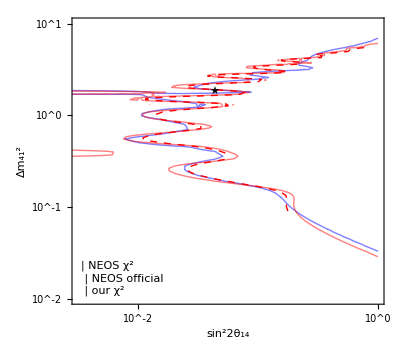

```mathematica
Show[
(*GlbPlot2d["results/th14dm41-neos.dat",P1Function->(Log10[Max[1*^-4,Sin[2#]^2]]&),Contours->{χ2[2,0.05],χ2[2,0.01],χ2[2,0.001],χ2[2,0.0001],χ2[2,0.00001],χ2[2,0.000001]},
ContourStyle->{Directive[Blue,Thick,Dotted]}],*)
ContourPlot[DataInterpol[i][10^logs22th14,logdm41],{logs22th14,-3,0},{logdm41,-2,1},Contours->{χ2[1,0.1]},ContourStyle->Directive[Thick,Blue],ContourShading->False],
ContourPlot[NEOSchi2Interpol[10^logs22th14,logdm41],{logs22th14,-3,0},{logdm41,-2,1},Contours->{χ2[1,0.1]},ContourStyle->Directive[Thick,Red],ContourShading->False],
(*ListPlot[DataLimit[i],Joined->True,PlotStyle->Directive[Blue]],*)
PlotRange->{{-2.5,0},{-2,1}},GridLines->Log10[{MyGrid[1*^-3,1*^0],MyGrid[1*^-2,1*^1]}],
FrameLabel->{"sin^22θ_14","Δm_41^2"},FrameTicks->{{LogTicks[-4,4],LogTicksNoLabel[-4,4]},{LogTicks[-4,4],LogTicksNoLabel[-4,4]}},
Epilog->{Red,Dashed,Line[NEOSExclusion],Black,Dashing[{}],Inset[MyLegend,Scaled[{0.03,0.03}],{-1,-1}],
Text["★",{Log10[BestFit[i]⟦1⟧],BestFit[i]⟦2⟧}]
(*,Text["95% CL, 2 dof",Scaled[{0.03,0.03}],{-1,-1}]*)}]
```

```mathematica
Data[i]={#⟦2⟧,Sin[2#⟦1⟧]^2,Min[#⟦3⟧,#⟦4⟧]}&/@Cases[Import[ "results/th14dm41-neos.dat","Table"],{Repeated[_?NumericQ]}];
Data[i]=Split[Sort[Data[i]],#1⟦1⟧==#2⟦1⟧&];
Data[i]=(m=Min[#⟦All,3⟧];
DataXInterpol=Interpolation[#⟦All,{2,3}⟧];
σ1=x/.FindRoot[DataXInterpol[x]-m==1,{x,1}];
σ2=x/.FindRoot[DataXInterpol[x]-m==1,{x,0}];
σ=If[Abs[σ1-σ2]>0.02,(σ1-σ2)/2,σ1];
({#⟦1⟧,#⟦2⟧,Exp[-(#⟦3⟧-m)/(2σ)]}&)/@#)&/@Data[i]; (* Subtract Subscript[χ, min]^2 for each Δm^2 and convert χ^2 to likelihood *)
Data[i]={#⟦1,1⟧,Interpolation[#⟦All,{2,3}⟧,InterpolationOrder->3]}&/@Data[i];
Data[i]={#⟦1⟧,Function[X,NIntegrate[#⟦2⟧[s22th14],{s22th14,0,X}]],
NIntegrate[#⟦2⟧[s22th14],{s22th14,0,1}]}&/@Data[i];//Quiet
DataLimit[i]={F[X_?NumericQ]:=Evaluate[#⟦2⟧[X]/#⟦3⟧];
Log10[s22th14]/.FindRoot[F[s22th14]==0.9,{s22th14,0,1}],#⟦1⟧}&/@Data[i];//Quiet
```

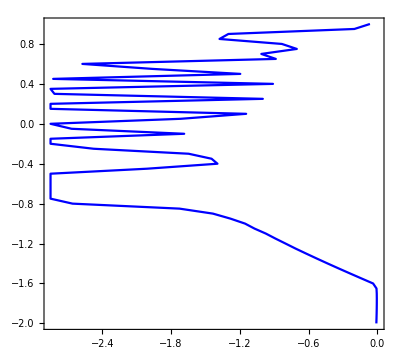

```mathematica
ListPlot[DataLimit[i],Joined->True,PlotStyle->Directive[Blue]]
```

0.127387

{x0→0.694452,σ→0.137229}

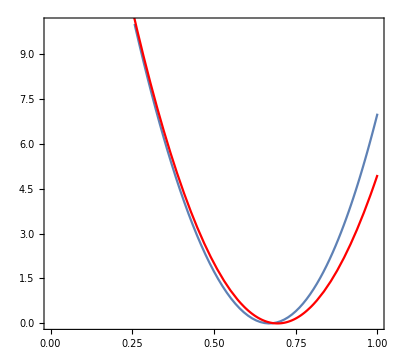

```mathematica
Clear[σ];
DataX=Data[i]⟦10,All,{2,3}⟧;
m=Min[DataX⟦All,2⟧];
DataX={#⟦1⟧,#⟦2⟧-m}&/@DataX;
DataXInterpol=Interpolation[DataX];
σσ=((x/.FindRoot[DataXInterpol[x]==1,{x,1}])-(x/.FindRoot[DataXInterpol[x]==1,{x,0}]))/2
f=(x-x0)^2/σ^2;
FindFit[DataX⟦1;;10⟧,f,{{x0,0.05},{σ,0.02}},x]
ff=f/.%;
Show[
ListPlot[DataX,Joined->True,PlotRange->{{0,1},{0,10}}],
Plot[ff,{x,0,1},PlotStyle->Red]
]
```

```mathematica
ArcSin[Sqrt[0.05]]/2
ArcSin[Sqrt[0.142]]/2
ArcSin[Sqrt[0.084]]/2
ArcSin[Sqrt[0.8]]/2
```

0.112757

0.193185

0.147023

0.553574

### Integrating over the size of the reactor core

(2 b (x1-x2)-Sin[2 b x1]+Sin[2 b x2])/(4 b (x1-x2))

(Erf[(2+a-2 x)/(2 √2 a σ)]+Erf[(-2+a+2 x)/(2 √2 a σ)])/(2 a)

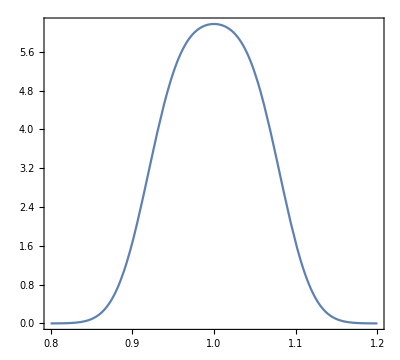

```mathematica
(* Folding the oscillating sine with a simple step function *)
Simplify[Integrate[Sin[b x]^2,{x,x1,x2}]/(x2-x1)]

(* Folding the oscillating sine with a smoothed step function *)
$Assumptions={σ>0,a>0,b>0,x0∈Reals};
ConvKernel=Integrate[Exp[-(x-x0)^2/(2 σ^2)]HeavisidePi[x],{x,-∞,∞}]/.{x0->(x-1)/a};
ConvKernel=Simplify[ConvKernel/Integrate[ConvKernel,{x,-∞,∞}]]
Plot[ConvKernel/.{σ->0.2,a->0.16},{x,0.8,1.2}]
```

```mathematica
(* The actual convolution *)
Simplify[Integrate[Cos[b x]*ConvKernel,x]];
Limit[%,x->∞]-Limit[%,x->-∞];
FullSimplify[(1-%)/2]
```

1/2-(ⅇ^(-1/2 a^2 b^2 σ^2) Cos[b] Sin[(a b)/2])/(a b)

## Sterile Neutrino Decay Rate

following Ivan’s notes Formalism.pdf

```mathematica
Reps1={
xji->mj/mi,
a->(mi^2+mj^2-mA^2)/mi^2,
Us1->Sin[θ14],
Us2->Cos[θ14]Sin[θ24],
Us3->Cos[θ14]Cos[θ24]Sin[θ34],
Us4->Cos[θ14]Cos[θ24]Cos[θ34],
Usi->Us4,
Usj->Us1,
mi->m4,
mj->m1};
Reps2={
m4->3.,
(*m1->0,*)
θ14->0.1,
θ24->0.14,
θ34->0
};
Γ=(g^2 Abs[Usi]^2 Abs[Usj]^2 mi)/(16π)(a+4xji)Sqrt[a^2-4 xji^2]+
(g^2 Abs[Usi]^2 Abs[Usj]^2 mi)/(16π)((mi+mj)/mA)^2((a-2xji)Sqrt[a^2-4 xji^2]+2 xji^2 Log[(a(a+Sqrt[a^2-4 xji^2]))/(2 xji^2)]);
```

```mathematica
Limit[Γ//.Reps1,m1->0]
```

(g^2 √(((m4^2-mA^2)^2)/m4^4) (m4^4-mA^4) Abs[Cos[θ14] Cos[θ24] Cos[θ34]]^2 Abs[Sin[θ14]]^2)/(16 m4 mA^2 π)

```mathematica
%//.Reps2
```

(7.12899×10^-6 g^2 √((9.-mA^2)^2) (81.-mA^4))/mA^2